Save directory for all files

```mathematica
saveDir="/home/nia/2TB/";
```

## Setup

### Physics

#### General Definitions

General spacetime setup, Equation 3.14, along with usual Christoffel symbols definition

```mathematica
crds = {t[λ],r[λ]};
Num=Length[crds];
G = {{-f[r[λ]],0},{0,g[r[λ]]}};
Christof= 1/2 Table[ Sum[ Inverse[G][[a,μ]](D[G[[c,μ]],crds[[b]]]+D[G[[μ,b]],crds[[c]]]-D[G[[b,c]],crds[[μ]]]),{μ,1,Num}],{a,1,Num},{b,1,Num},{c,1,Num}] // FullSimplify;
```

Sub out "xdotsq" with actual expression for (ẋ)^2 using the above metric and coordinates definitions

```mathematica
xdsr = xdotsq -> Sum[G[[μ,ν]] D[crds,λ][[μ]]D[crds,λ][[ν]],{μ,1,Num},{ν,1,Num}];
```

Define the three Lagrangians we are interested in, Equations B.2.1-B.2.3

```mathematica
Lmass = -m Sqrt[- xdotsq] /.xdsr 
Lmass2 = m^2 xdotsq /. xdsr
Lein = 1/2 ( xdotsq /e[λ] - e[λ] m^2) /. xdsr
```

-m √(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)

m^2 (g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2)

1/2 (-m^2 e[λ]+(g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2)/e[λ])

Functions to find canonical momentum and Euler-Lagrange Equations from Lagrangians

```mathematica
(* Note, doesn't find Subscript[Π, e] = ∂/(∂ė)(Subscript[L, einbein]) since is zero in our case*)
PI[L_] := Table[D[L,D[crds[[μ]],λ]],{μ,1,Num}]
findELE[L_]:=Table[ D[L,crds[[μ]]] - D[PI[L][[μ]],λ],{μ,1,Num}]
```

Parallel transport operator D/dλ=(ẋ)^ν∇_ν acting on a vector (top) or co-vector (bottom), based on Carroll 3.40. Defined directly as using covariant derivative doesn’t account for d/dλ=(ẋ)^μ∂_μ

```mathematica
ParlTru[x_]:= Table[D[x[[μ]],λ] + Sum[D[crds[[ν]],λ] Christof[[μ,ν,α]] x[[α]],{ν,1,Num},{α,1,Num}],{μ,1,Num}];
ParlTrl[x_]:= Table[D[x[[μ]],λ] - Sum[D[crds[[ν]],λ] Christof[[α,ν,μ]] x[[α]],{ν,1,Num},{α,1,Num}],{μ,1,Num}];
```

Rule to apply static gauge condition

```mathematica
statGauge=t-> Function[λ,λ];
```

#### Coordinate Specific definitions

Three spacetime classes: flat, conformally flat, and Schwarzschild-like

```mathematica
FlatSpacer = {g-> Function[r,1], f-> Function[r,1]};
ConfSpacer = {g-> Function[r,f[r]]};
SchLSpacer ={g-> Function[r,1/f[r]]};
```

Specific metric factors for the two coordinate systems of AdS_3-Schwarzschild spacetime, Equation 2.24

```mathematica
f Ads[r_] := (r^2-rH^2)/l^2 ; f Tort[rs_] := rH^2/l^2 Csch[rH rs/l^2]^2;
```

Rules to implement specific coordinate systems using above

```mathematica
AdsCrdr = {g-> Function[r,1/f Ads[r]],f-> Function[r,f Ads[r]]};
TortCrdr = {g-> Function[r,f Tort[r]],f-> Function[r,f Tort[r]]};
```

Package them together in convenient association

```mathematica
allCrdRules =AssociationThread[{"Flat","AdS","Tort"}->{ FlatSpacer,AdsCrdr,TortCrdr}];
```

Functions to convert between AdS and tortoise coordinates, Equation 2.20

```mathematica
ToTort[r_] := l^2/rH ArcCoth[-r/rH];
ToAds[rs_]:= -rH Coth[rH rs/l^2];
```

Numeric versions of the above conversion functions

```mathematica
NToTort:=(ToTort[#]/.ValsCom)&;
NToAds:=(ToAds[#]/.ValsCom)&;
```

#### Numeric Values and General Initial Conditions

Going to store all numeric values as replacement rules so we can still print symbols in equations but replace before passing to NDSolve. Can also just have the general form of the IC equations here, which define the names the replacement rules use. Note excludes einbein as not all use it, so would need to add those in for the ones that do.

```mathematica
ICcom = {r[0]==ri,t[0]==ti,r'[0]==rpi,t'[0]==tpi};
```

First  we  have  the  parameters  of  the  spacetime  and  a  common  mass  to  use  for  all  massive  cases

```mathematica
ValsCom={rH->0.3, l->1, mass->1}; (*Using mass rather than m so we can say m->0 for massless and m->mass for massive*)
```

We will also always use (t(λ))_(λ=0) = 0 and t'(λ)_(λ=0)=1 as the initial conditions for the time coordinate,

```mathematica
AppendTo[ValsCom,ti->0]; AppendTo[ValsCom,tpi->1];
```

We now need the IC for r(λ). These IC will depend on some conditions and cases of setup, so lets only do the ones that don’t need more work here and store all the options in an association. Can then add in other cases when we work them out and just pick which to apply when doing numerics.

```mathematica
rIC = Association[];
rpIC= Association[];
```

For the “standard” coordinate systems (Flat spacetime and AdS coordinates, but not tortoise coordinates), we can pick our r(λ)_(λ=0) , and then this also determines it for the tortoise coordinates as the transform of this:

```mathematica
Module[{r0val},
r0val=1; (*This sets the actual value*)
AppendTo[rIC,{"Standard" -> (ri-> r0val),"Tort"-> (ri-> ToTort[r0val])}];
]
```

And for the massive case in any coordinate system, can always pick initially static

```mathematica
AppendTo[rpIC, "Massive"-> (rpi-> 0)];
```

### Helper Functions

Collection of useful helper functions used in computations

#### Interpolating functions

Finds the (n) largest or smallest derivative values of an interpolating function. Very slow

```mathematica
findLargestDeriv[obj_,rule_,n_:1]:=Module[{grid,derivVals},
grid=(obj/. rule)["Grid"];
derivVals=Flatten[Table[obj'[i]/. rule,{i,grid}]];
Return[TakeLargest[derivVals,n]];
];
findSmallestDeriv[obj_,rule_,n_:1]:=Module[{grid,derivVals},
grid=(obj/. rule)["Grid"];
derivVals=Flatten[Table[obj'[i]/. rule,{i,grid}]];
Return[TakeSmallest[derivVals,n]];
];
```

Returns the domain of an interpolating function in the form {x_min,x_max}

```mathematica
getDomain[func_]:= Flatten[func["Domain"]];
```

Takes a list of interpolating functions, returns true only if all of them have a domain that extends further than $MachineEpsilon variable. Used to check for solutions that have essentially no extent

```mathematica
rngAcceptable=AllTrue[Abs[getDomain[#][[1]]-getDomain[#][[2]]]>=$MachineEpsilon&];
```

Returns the (transpose of the) raw data of the interpolating function

```mathematica
getData[func_]:={Flatten[func["Grid"]],Flatten[func["ValuesOnGrid"]]};
```

Restricts an interpolating function to specific values (its domain by default)

```mathematica
Restrict[func_,rng_:{}]:=Module[{xmin,xmax,newFn},
{xmin,xmax}=If[Length[rng]==2,rng,getDomain[func]];
Return[Piecewise[{{func[#],xmin<=#<=xmax}},Indeterminate]&];
];
```

Gets the most extreme (min, max) of the output values of an interpolating function, optionally with corresponding independent variable values preceding the extremal values

```mathematica
getExtremes[fn_,tVals_:False]:=Module[{data,mint,minx,maxt,maxx},
data=Transpose[getData[fn]];
{maxt,maxx}= TakeLargestBy[data,#[[2]]&,1][[1]];
{mint,minx}= TakeSmallestBy[data,#[[2]]&,1][[1]];
If[tVals,Return[{{mint,minx},{maxt,maxx}}],Return[{minx,maxx}]];
]
```

Takes a (raw) interpolating function (which is assumed to be a comparison) and a range of acceptable values, and returns the range(s) of the input variable that result in output variable outside the range, or else True if there are none

```mathematica
inRange[fn_,reqRng_]:=Module[{grid,vals,Res={}(*,fresh=True,last=0*)},
{grid,vals}=getData[fn];
Do[
If[reqRng[[1]]<=i[[2]]<= reqRng[[2]],Continue[]];
AppendTo[Res,i[[1]]];
,{i,Transpose[{grid,vals}]}];
Return[If[Length[Res]==0,True,Res]];
];
```

#### Solving

Have stored our solutions and comparisons in separate contexts, this just adds our contexts to context path so can use them as normal variables

```mathematica
$ContextPath={"FinSols`","Comps`"}~Join~$ContextPath;
```

Runs over all equations in an association,  passes each one to NDSolve, and stores all the results (with some error info) into a returned association with same keys

```mathematica
Options[SolveAllRaw]={"OtherOps"-> {Method->Automatic}};
SolveAllRaw[Eqns_,Einbein_,OptionsPattern[]]:=
Quiet[
Off[General::stop];
Module[{res},res=Association[];
Do[Module[{thisRun,RunStat,Errd,toSlv},
$MessageList={}; (*This generates "Set::wrsym" Error, so if last error is still that afterwards we know no errors happend *);
toSlv=If[Einbein,{t,r,e},{t,r}];
thisRun=Flatten[NDSolve[Eqns[i],toSlv,{λ,0,10},Replace[OptionValue["OtherOps"],List->Sequence,{1},Heads->True]]];
If[Head[thisRun]==NDSolve,thisRun=Hold[thisRun]]; (* Just makes it so if the NDSolve didn't run hold it, so dont get errors every time we use it in future*)
Errd = If[$MessageList[[-1]] == HoldForm[Set::wrsym],False,$MessageList[[-1]] ,$MessageList[[-1]]];
(*If the head of the result isn't a list it obviously failed, but also want to catch if it just gives a function with no range (for any of the solutions)*)
RunStat = If[ListQ[thisRun] && (Length[thisRun]>0),rngAcceptable[toSlv /. thisRun],False];
AppendTo[res,i->{RunStat,Errd,Flatten[thisRun]}];
],{i,Keys[Eqns]}];
Return[res]];
On[General::stop];];
```

Generates more detailed error message from the results of SolveAllRaw . Assumes entry has layout generated by that function

```mathematica
ErrorStatus[entry_,id_,lookup_:{}]:=
{entry[[1]],ToString[id]<>": " <> If[entry[[1]], "Ran successfully with ", "Failed to run with "] <> If[entry[[2]],,"no Errors","the Error: " <>ToString[entry[[2]] //. lookup] ]};
```

Uses the above two functions to generate solutions and error status for association of equations

```mathematica
Options[SolveAll]={"OtherOps"-> {Method->Automatic}};
SolveAll[Eqns_, Einbein_:False,OptionsPattern[]]:=Module[{rawRes,fullRes},
rawRes=SolveAllRaw[Eqns,Einbein,"OtherOps"-> OptionValue["OtherOps"]];
fullRes=Association[];
Do[AppendTo[fullRes, i-> {rawRes[i][[3]],ErrorStatus[rawRes[i],i,Messages[NDSolve]] }],{i,Keys[Eqns]}];
Return[fullRes];
]
```

Prints the error status for all results in an association; assumes association has the layout returned by SolveAll

```mathematica
printStatus[solvRes_] := Do[Print[i[[2,2]]],{i,solvRes}];
```

Applies the specified rule for converting general equation to spacetime/coordinate specific equation to every equation in association; also simplifies the equation after substitution

```mathematica
SpecifyST[eqns_,rules_]:=Module[{ret},
ret=Association[];
Do[AppendTo[ret,i-> FullSimplify[eqns[i] //. rules]]
,{i,Keys[eqns]}];
Return[ret];]
```

Converts a pure function to an interpolating function of the given range and density; useful as lots of other functions assumes an interpollating function

```mathematica
pureToInterp[func_,rng_:{0,10},density_:200]:=Module[{grid, data},
grid=Subdivide[rng/.List->Sequence, density ];
data=func/@ grid;
Return[Interpolation[Transpose[{grid,data}]]];
]
```

The explicit null method already gives us a solution for r[λ], this just translates to same form as all others so it can be added to the list to plot

```mathematica
eNullSolve[eqn_,ric_,otherRules_:{}]:=Module[{tSol=Function[λ,λ],rSol,stat,fin},
(*Applying otherRules twice so that it can be used for both variables already in the equation before solving as well as for variables coming from ric or any other intial conditions*)
rSol=(Solve[((eqn//.otherRules)==0 /. (ICcom /. Equal -> Rule)),r[λ]])//.Flatten[{ric,otherRules}];
stat=FreeQ[rSol,Integrate]; (*Check if rSol still contains an unevaluated Integral, since MMA will try to evaluate if it can*)
fin={Flatten[{t->tSol,rSol/. (Rule[x_[l_],rhs__]-> Rule[x, Function[l,rhs]]) }], {stat,"NuE: Manual explicit null method"}};
(*If it didn't run, just return this form*)
If[!stat, Return[fin]];
(*Else just converting these pure functions to interpollating, can really only use the default ranges as what else makes sense?*)
Return[fin /.(Rule[x_,rhs__]-> Rule[x,pureToInterp[rhs]])];
];
```

The Implicit null method requires some special considerations so can’t just use the above SolveAll function, need this one instead

```mathematica
iNullSolve[eqn_,ric_]:=Module[{eqns,rawS,brchS,tRng,tDenst},
eqns={eqn==0,r[0]==ri} //. Flatten[{ValsCom,ric}];
rawS=NDSolve[eqns,r,{λ,0,10}];
brchS=Select[Flatten[rawS], ((r[1]-r[0])/.#)<0&];
(*This time r sol is already interpollating, just need to change the static gauge. But now have this interp func so might as well use that so they have the same domain and density*)
tRng=getDomain[r/.brchS];
tDenst=Length[getData[r/.brchS][[1]]];
Return[{Flatten[{t-> pureToInterp[Function[λ,λ],tRng,tDenst], brchS}],{True,"NuI: Manual implicit null method"}}]
]
```

Generates all possible equations for a non-einbein system by passing general equations, coordinate system, and mass case

```mathematica
(*crdSys should be one of {"Flat","Tort", "AdS"}, massive should be bool, and select should be some subset of Keys[rawEom]*)
genEqnsNE[rawEom_,crdSys_,massive_,select_]:=Module[{res},
If[!MemberQ[{"Flat","Tort", "AdS"},crdSys],Print["coord system (2nd argument) must be one of \"Flat\",\"Tort\", or \"AdS\"."];Return[]];
res=Association[];
Do[Module[{eom,rules,final},
eom=Thread[(rawEom[i]/. m->If[massive,mass,0])==ConstantArray[0,Length[rawEom[i]]]];
rules = Flatten[{ValsCom, rIC[If[crdSys=="Tort","Tort","Standard"]],rpIC[If[massive,"Massive","Massless"]]}] //. Switch[crdSys,"Flat",FlatSpacer,"Tort",TortCrdr,"AdS",AdsCrdr];
final = Flatten[{eom,ICcom}] //. rules;
AppendTo[res,If[massive,i<>"M",i<> "Ml"]->final];
],{i,select}];
Return[res];
];
```

Generates all possible equations for an einbein system by passing general equations, coordinate system, mass case, and specification of which einbein equations and initial conditions to use

```mathematica
addPos=Map[Function[i,Flatten[{i,FirstPosition[#,i]}]],#]& ;
genEqnsE[rawEom_,crdSys_,massive_,useCons_,useConsD_,useEic_,useEpic_]:=
Module[{eom,rules,ICeqns, EomVariants,mRule,list1,list2,final},
If[!(useCons || useConsD),Print["One of useCons and useConsD (arguments 4 & 5) must be True"]; Return[]];
If[!(useEic || useEpic),Print["One of useEic and useEpic (arguments 6 & 7) must be True"]; Return[]];
mRule=m->If[massive,mass,0];
eom=Thread[(rawEom/. mRule)==ConstantArray[0,Length[rawEom]]];
rules = Flatten[{ValsCom, rIC[If[crdSys=="Tort","Tort","Standard"]],rpIC[If[massive,"Massive","Massless"]], Switch[crdSys,"Flat",FlatSpacer,"Tort",TortCrdr,"AdS",AdsCrdr],mRule}];
ICeqns = Flatten[{ICcom,If[useEic,e[0]==ei,{}],If[useEpic,e'[0]==epi,{}]}]/. rules;
EomVariants=Association[];
list1=Which[useCons && useConsD, {{#[[1,1]]==0,#[[2,1]]==0},"c"<>ToString[#[[1,2]]] <> "d" <> ToString[#[[2,2]]]}& /@ Tuples[{EinConstr//addPos,EinConstrD//addPos}],
useCons , {#[[1]]==0, "c"<>ToString[#[[2]]]<> "d0" }& /@ (EinConstr//addPos),
useConsD , {#[[1]]==0, "c0d"<>ToString[#[[2]]] }& /@ (EinConstrD//addPos)];
Do[
AppendTo[EomVariants,i[[2]] -> Flatten[{eom, i[[1]]}]];
,{i,list1}];
list2=Which[useEic && useEpic, {{#[[1,1]],#[[2,1]]},"e"<>ToString[#[[1,2]]] <> "ep" <> ToString[#[[2,2]]]}& /@ Tuples[{If[massive,potentialMEICs,potentialMlEICs]//addPos,potentialEPICs//addPos}],
useEic , {#[[1]], "e"<>ToString[#[[2]]]<> "ep0" }& /@ (If[massive,potentialMEICs,potentialMlEICs]//addPos),
useEpic , {#[[1]], "e0ep"<>ToString[#[[2]]] }& /@ (potentialEPICs//addPos)];
final=Association[];
Do[
AppendTo[final, ("E"<> i <> j[[2]]<>If[massive,"M","Ml"])  -> Flatten[{EomVariants[i], ICeqns //. (j[[1]]/.rules)}] //. rules];
,{i,Keys[EomVariants]},{j,list2}];
Return[final];
]
```

Generate all possible combinations of coordinate systems and mass cases applied to an equation

```mathematica
genEVariants[eqn_,crdSys_,massive_]:=Module[{pairs1,pairs2,lst},
pairs1=Select[Tuples[{{True,False},{True,False}}],(#[[1]] ⊻ #[[2]])&];
pairs2=Select[Tuples[{{True,False},{True,False}}],(#[[1]] || #[[2]])&];
lst=Flatten[Table[Flatten[{i,j}],{i,pairs1},{j,pairs2}],1];
Return[Join[Replace[Table[genEqnsE[eqn,crdSys,massive,i/. List-> Sequence],{i,lst}],List->Sequence,{1},Heads->True]]];
];
```

Generates a list of assumptions about a given (list of) unknown functions by applying the given condition function to every instance of the unknown functions appearing in the supplied expression

```mathematica
funcAssumps[expr_,funcs_:{f,g},cond_:Function[x,x>0]]:=Module[{intm},
intm = Thread[cond[Cases[expr,#[___]/;!ValueQ[#],Infinity]]]&/@ funcs;
Replace[intm,List-> Sequence,{2},Heads->True] // DeleteDuplicates
]
```

Converts a replacement rule to an implicit equation

```mathematica
getImplEqn[rule_,dVar_,iVar_]:=Module[{sol},
sol=dVar[iVar]/.rule;
Head[sol][[1]][dVar[iVar]]==sol[[1]]
]
```

Converts an explicit replacement rule (r[λ]→ ...) to an implicit one (r → ...)

```mathematica
explToImplRule = (Rule[x_[t_],y__]-> Rule[x,Function[t,y]]);
```

Solves an equation for a function of a given independent variable, and converts result to implicit replacement rule

```mathematica
solveForFuncRule[eqn_,dVar_,iVar_]:= Solve[eqn,dVar[iVar]] /. explToImplRule
```

Converts an expression in terms of an dependent and independent variable into a Function object

```mathematica
rhsToFuncRule [rhs_,depVar_,indepVar_]:= depVar->Function[indepVar,rhs];
```

Gives back the same expression but with all integrals combined appropriately and numeric integrals with correct ordering of bounds . Works with equations too, though it
  rewrites to be == 0. Retains active/inactive state of the integrals

```mathematica
simpInt[expr_]:=Module[{sepEqls=Switch[Head[#1],Equal,{#1 /. Equal[x_,y_]->x-y,True},_,{#1,False}]&,
(*reord = Inactivate[(Integrate[f_,Condition[{x_,a_?NumericQ,b_?NumericQ},a>b]]|Integrate[f_,{x_,a_?(!NumericQ[#]&),b_?NumericQ}]),Integrate]->Inactivate[(-Integrate[f,{x,b,a}]),Integrate]/. x__-> {x//Activate},*)
reorder = {(Integrate[f_,Condition[{x_,a_?NumericQ,b_?NumericQ},a>b]]|Integrate[f_,{x_,a_?(!NumericQ[#]&),b_?NumericQ}]):>-Integrate[f,{x,b,a}],(-Integrate[f_,Condition[{x_,a_?NumericQ,b_?NumericQ},a>b]]|-Integrate[f_,{x_,a_?(!NumericQ[#]&),b_?NumericQ}]):>Integrate[f,{x,b,a}]} /. RuleDelayed[x_,y_]:>Sequence[RuleDelayed[x,y],Inactivate[RuleDelayed[x,y],Integrate]](* Thread[{x,Inactivate[x,Integrate]}:>{y,Inactivate[y,Integrate]}]*) ,
comber = {Integrate[f_,{x_,a_,b_}] + Integrate[f_,{x_,b_,c_}] :> Integrate[f,{x,a,c}],Integrate[f_,{x_,a_,b_}] - Integrate[f_,{x_,c_,b_}] :> Integrate[f,{x,a,c}],
-Integrate[f_,{x_,b_,a_}] + Integrate[f_,{x_,b_,c_}] :> Integrate[f,{x,a,c}]} /. (*Except[_List,x_]->Sequence[x,Activate[x,Integrate]]*)RuleDelayed[x_,y_]:>Sequence[RuleDelayed[x,y],Inactivate[RuleDelayed[x,y],Integrate]],
rawExpr,wasEql, ordInts,combInts},
{rawExpr,wasEql} = sepEqls[expr];
ordInts=(rawExpr/. reorder);
combInts=(ordInts /. comber) // FullSimplify;
Return[Switch[wasEql,True,combInts==0,_,combInts]]
]
```

#### Plotting

Useful Macro to make parametric plots with each subsequent plot having thinner lines, nice for plotting overlaid versions

```mathematica
decThicks[N_,spacing_:0.01]:=Reverse[Table[n*spacing,{n,1,N}]];
```

Takes a symbolic object to plot and an association of solutions (of the form generated by SolveAll) and generates a convenient list for plotting . Assumes detailed error data no longer relevant as used for plotting overlaid version

```mathematica
genPlotable[toPlot_,Sols_,Exclude_:{},Extrapolate_:True]:=Module[{Res},
Res={};
Do[
If[Sols[i][[2,1]] && !MemberQ[Exclude,i],Module[{rawSols, modSols={}},
rawSols=Sols[i][[1]];
If[Extrapolate,modSols=rawSols,
Do[Module[{var,fn},
{var,fn}=j/. Rule->List;
AppendTo[modSols,var->Restrict[fn]];
],{j,rawSols}];
];
 AppendTo[Res, {toPlot/.modSols, i}]
]]
,{i,Keys[Sols]}];
Return[Transpose[Res]];
];
```

Taking the same arguments, uses genPlotable to plot overlay of all (valid) solutions, with decreasing size

```mathematica
Options[plotAll]={"AspectRatio"-> 1,"AxesLabel"->{},"Legend"->{},"LamMax"->10,"PlotRange"->Automatic,"Exclude"->{},"Extrapolate"->True};
plotAll[toPlot_,Sols_,OptionsPattern[]]:=Module[{plts,names,lgnd,axlbl},
{plts,names} = genPlotable[toPlot,Sols,OptionValue["Exclude"],OptionValue["Extrapolate"]];
lgnd=If[Length[OptionValue["Legend"] ]==0,names,OptionValue["Legend"] ];
axlbl=If[Length[OptionValue["AxesLabel"] ]==0,toPlot,OptionValue["AxesLabel"] ];
ParametricPlot[plts,{λ,0,OptionValue["LamMax"]}, PlotLegends->lgnd,PlotStyle->Thickness/@ decThicks[Length[plts]],AspectRatio->OptionValue["AspectRatio"],AxesLabel->axlbl,PlotRange->OptionValue["PlotRange"]]
];
```

#### Analytic Comparison and error tracking

Rules to sub out all objects with prime numbers so taking ratios and factorising we can see by which factors they differ . Excluding prime 2 because overall factor of 2 or 1/2 common already so want to differentiate those, and difference by factor of mass don’t matter if its not zero

```mathematica
compValsM = {m->1, f[r[λ]]->3, g[r[λ]]->5,f'[r[λ]]->7, g'[r[λ]]->11, r[λ]->13,t[λ]->17,e[λ]-> 23,r'[λ]->29,t'[λ]->31,e'[λ]->37,r''[λ]->41,t''[λ]->43};
compValsML = {m->0, f[r[λ]]->3, g[r[λ]]->5,f'[r[λ]]->7, g'[r[λ]]->11, r[λ]->13,t[λ]->17,e[λ]-> 23,r'[λ]->29,t'[λ]->31,e'[λ]->37,r''[λ]->41,t''[λ]->43};
```

Takes factors list in MMA format and prints in a more human readable format

```mathematica
sepFactors[factors_] := Module[{ret=1},
Do[ fac=factors[[i]][[1]]; pow = factors[[i]][[2]]; ret=ret*With[{f=fac,p=pow},HoldForm[f^p]],{i,Length[factors]}];
Return[ret];];
```

```mathematica
sepFactors [{{2,2},{3,1},{5,3}}]
```

2^2 3^1 5^3

Finds prime factorisation of ratio of inputs, and prints what they differ by

```mathematica
Factors[n1_,n2_]:= Module[{rat = n1/n2},
Which[rat==1, Print["Perfect agreement"],
MemberQ[{-1,2,1/2,-2,-1/2},rat],Print["Agrees up to non-zero factor of ", rat],
True,Print["Diagreement by ",If[Denominator[rat]==1,sepFactors[Numerator[rat] // FactorInteger],sepFactors[Numerator[rat] // FactorInteger]/sepFactors[Denominator[rat] // FactorInteger]]];]];
```

Returns LHS of equation when rearranged to LHS == 0

```mathematica
ZeroPart[eq_]:=Module[{parts},
parts=List @@ eq;
Which[parts[[1]]===0,Return[parts[[2]]],
parts[[2]]===0, Return[parts[[1]]],
True, Return[parts[[1]] - parts[[2]]]]
];
```

Quickly change equation to initial conditions

```mathematica
ToIC={ r[λ]-> ri, t[λ]->ti,t'[λ]->tpi,r'[λ] ->rpi,λ->0};
```

Takes association of solutions (assumed to be comparisons), returns list of {name, max absolute value}

```mathematica
checkAllCompsRaw[compFns_,repObj_]:=Module[{Res={}},
Do[Module[{ratio=False,fn,extr},
ratio=Switch[Head[i],Plus,False,Times,True];
fn= repObj /. compFns[i];
extr=getExtremes[fn];
AppendTo[Res,Flatten[{i,TakeLargest[Abs/@ extr,1]}]];
],{i,Keys[compFns]}];
Return[Res];
]
```

```mathematica
Options[checkAllComps]={"CompMethod"->"Diff","repObj"->r,"Threshold"->10^-5,"Print"->True};
checkAllComps[compFns_,OptionsPattern[]]:= Module[{rng,extrms,thr=OptionValue["Threshold"],pass={},fail={}},
rng=Switch[OptionValue["CompMethod"],"Diff",{-thr,thr},"Ratio",{1-thr,1+thr},_,Print["CompMethod option must be one of Diff or Ratio"];Return[];];
extrms= checkAllCompsRaw[compFns,OptionValue["repObj"] ];
If[OptionValue["Print"],Print["Comparing a total of ",Length[compFns]," comparison functions with the ",OptionValue["CompMethod"]," method. Threshold set to ",OptionValue["Threshold"]]];
Do[Module[{inRng,txt},
inRng=rng[[1]]<=i[[2]]<= rng[[2]];
txt=ToString[i[[1]]]<>": ";
If[inRng,AppendTo[pass,i[[1]]];txt=txt<>"Within threshold.";,AppendTo[fail,i[[1]]];txt=txt<>"Outside threshold: Max value of "<>ToString[i[[2]]]];
If[OptionValue["Print"],Print[txt]];
],{i,extrms}];
Return[{pass,fail}];
]
```

```mathematica
Options[analyzeComps]={"CompMethod"->"Diff","repObj"->r,"Threshold"->10^-5,"Print"->True};
analyzeComps[compFns_,OptionsPattern[]]:= Module[{offset,thr,pass={},fail={},totals,best,worst,min1=0,min2=0,max1=0,max2=0 },
offset=Switch[OptionValue["CompMethod"],"Diff",0,"Ratio",1,_,Print["CompMethod option must be one of Diff or Ratio"];Return[];];
Do[Module[{thFn=OptionValue["repObj"]/. compFns[i],extrms ,inThr},
extrms=Thread[getExtremes[thFn]- {offset,offset}];
inThr = AllTrue[extrms,(-thr<= # <= thr)&];
If[inThr, AppendTo[{i,extrms},pass],AppendTo[{i,extrms},fail]];
],{i,Keys[compFns]}];
totals=Length/@ {pass,fail};
Do[Module[{name,x1,x2,extr},
{name,{x1,x2}}=i;
extr=TakeLargest[Abs/@{x1,x2}][[1]];
If[x1<min1,min1=x1];
If[x2>max1,max1=x2];
],{i,pass}];
Do[Module[{name,x1,x2},
{name,{x1,x2}}=i;
If[x1<min2,min2=x1];
If[x2>max2,max2=x2];
],{i,fail}];
If[OptionValue["Print"],Print["Comparing a total of ",Length[compFns]," comparison functions with the ",OptionValue["CompMethod"]," method. Threshold set to ",OptionValue["Threshold"],".\nOf those, ",totals[[1]]," passed while ",totals[[2]], " failed.\n"]];
];
```

#### Numeric Comparisons

Takes a list of associations, returns a list of the same associations where only entries passing the criteria are kept in each object

```mathematica
applyCut[src_,crit_]:=Module[{res,init,resL},
res=Table[Select[i, crit],{i,src}];
init=Length /@ src;
resL=Length /@ res;
Print["Starting with ", init, " entries, cut ", Thread[init-resL], " for a total of ", resL," remaining entries"];
Return[res];
]
```

Takes a list of solutions for t[λ],r[λ] (assumed to be in the form {t->...,r->...}) and returns r[t]=r[t^-1[t]] (also in form r->...)

```mathematica
genRfT[Sol_,Extrap_:True]:= Module[{tFn,rFn,tData,rData,matchData,rtData,rtFunc,finFunc, test=MatchQ[#, {{_,_},{_,_}}]&, trueM, rest},
{tFn,rFn}={t,r}/.Sol;
tData=getData[tFn]//Transpose;
rData=getData[rFn]//Transpose;
matchData=Gather[tData ~Join~ rData,First[#1]==First[#2]&];
trueM=Select[matchData,test];
(*These ones that have a "true match" we can just immediadely condense together like did before:*)
rtData=Table[{i[[1,2]],i[[2,2]]},{i,trueM}];
rest=DeleteElements[matchData,trueM];
(*For all the remaining ones, needs some more care. *)
If[Length[rest]>0,rest=Flatten[rest,{1,2}];
Do[Module[{lamVal, dvVal,otherFn,isT, otherVal},
{lamVal,dvVal}=i;
(*First, lets figure out if the isolated data point we have is coming from t or r*)
{otherFn,isT}=Which[MemberQ[tData,{lamVal,dvVal}], {rFn,True},MemberQ[rData,{lamVal,dvVal}], {tFn,False}  ];
(*In either case, we can get the other value by evaluating the other function at this λ value*)
otherVal=otherFn[lamVal];
(*Now have our data point {tvalue, rvalue} that we can append to RTdata, just need to be careful with order depending on which one dealing with*)
AppendTo[rtData, If[isT, {dvVal,otherVal}, {otherVal,dvVal}]];
],{i, rest}]];
(*Now have collected all r-t data points, so can make it a function and optionally restrict it on return*)
rtFunc=Interpolation[rtData//DeleteDuplicates];
finFunc=If[Extrap, rtFunc,Restrict[rtFunc]];
Return[r->finFunc];
];
```

Takes a pair of solutions (interpolating functions of the form "repObj" -> ..., NOT association or raw interpolating object), and returns the comparison function of these two (either by ratio or by difference as specified) in the same form . DOES NOT check for them being identical

```mathematica
Options[genComp]={"repObj"->r};
genComp[{sol1_,sol2_},compMethod_:"Diff",convFn_:{Identity},extrap_:True,OptionsPattern[]]:=Module[{(*rawConv,*)comp,toConv},
comp=Switch[compMethod,"Diff", (#1-#2)&,"Ratio",((#1/#2)-1)&,"RDiff",((#1-#2)/#1)&,_,Print["compMethod (3rd argument) must be one of Diff, Ratio, or RDiff"];Return[];];
toConv=Switch[Length[convFn],1,Flatten[{convFn,convFn} /. {}->Identity],2,convFn /. {}->Identity,_,Print["convFn (2nd argument) must be a list containing either 1 or 2 elements."];Return[]];
Module[{fn1,fn2,grid1,grid2,newGrid={},newVals={},newFn,rng},
{fn1,fn2}=OptionValue["repObj"]/. {{sol1},{sol2}};
grid1=getData[fn1][[1]];
grid2=getData[fn2][[1]];
(*Need to then restrict to the region that is common between them. That range is going to be from the largest of the start values up to to smallest of the end values *)
rng=Flatten[Transpose[{getDomain[fn1],getDomain[fn2]}]//{TakeLargest[#[[1]],1], TakeSmallest[#[[2]],1]}&];
(*Grid points aren't guaranteed to be the same anymore, so lets combine them together for higher density *)
newGrid=DeleteDuplicates[Union[Flatten[(Select[#,rng[[1]]<=#<= rng[[2]]&]&/@ {grid1,grid2})]]];
(*Ok for some reason union isn't getting rid of duplicates even tho docs say it should, hence explicit delete duplicates*)
(*Now we just iterate though the new grid values and get the new function value at each point*)
newVals= Table[comp[toConv[[1]][fn1[j]],toConv[[2]][fn2[j]]],{j,newGrid}];
(*Finally, return the resulting interpolating function*)
newFn=Interpolation[Transpose[{newGrid,newVals}]];
Return[OptionValue["repObj"]->If[extrap,newFn,Restrict[newFn]]];
]];
```

Similar function to generate comparison between a numeric and analytic solution

```mathematica
Options[genAnaVnumComp]={"repObj"->r};
genAnaVnumComp[ana_,num_,compMethod_:"Diff",convFn_:{Identity},OptionsPattern[]]:=Module[{comp,toConv, numDat=getData[OptionValue["repObj"]/.num],res,finalRes},
comp=Switch[compMethod,"Diff", (#1-#2)&,"Ratio",((#1/#2)-1)&,"RDiff",((#1-#2)/#1)&,_,Print["compMethod (3rd argument) must be one of Diff, Ratio, or RDiff"];Return[];];
toConv=Switch[Length[convFn],1,Flatten[{convFn,convFn} /. {}->Identity],2,convFn /. {}->Identity,_,Print["convFn (2nd argument) must be a list containing either 1 or 2 elements."];Return[]];
res= Table[{i[[1]], comp[i[[2]],OptionValue["repObj"][i[[1]]]/.num]},{i, Transpose[numDat]}];
finalRes=Interpolation[res];
Return[OptionValue["repObj"]->finalRes];
]
```

Generates the RMS of an interpolating function replacement rule, which should be a comparison

```mathematica
Options[getRMS]={"repObj"->r};
getRMS[sol_,OptionsPattern[]]:=Module[{sumSqs, data,rms},
data=(OptionValue["repObj"] /. sol) //getData;
sumSqs = Sum[i^2, {i,data[[2]]}];
rms = Sqrt[sumSqs/Length[data[[1]]]];
Return[rms];
]
```

Similarly generates the max of an interpolating function replacement rule

```mathematica
Options[getMax]={"repObj"->r};
getMax[sol_,OptionsPattern[]]:=Module[{abss, data,max},
data=(OptionValue["repObj"] /. sol) //getData;
abss = Table[Abs[i], {i,data[[2]]}];
max=Max[abss];
Return[max];
]
```

Create a nice, human readable ranking table of the RMS and Max deviation data

```mathematica
rankingTable[assoc_]:=Module[{headings,rawVals,ord,grid},
headings=Keys[assoc];
(*Order is always RMS then Max*)
rawVals=ResourceFunction["MergeByKey"][{#["RMS"],#["Max"]},{}]&/@assoc;
(*Want to order by RMS*)
ord=((SortBy[Normal[#],#[[2,1]]&]&/@ rawVals)/.Rule->List)(*//SortBy[#[[2,1]]&];*);
Module[{T1,T2},
{T1,T2}=Values[ord];
{T1,T2}=Which[Length[T1]==Length[T2],{T1,T2},Length[T1]>Length[T2],{T1,T2~Join~ConstantArray[{"-",{"-","-"}},Length[T1]-Length[T2]]},Length[T1]<Length[T2],{T1~Join~ConstantArray[{"-",{"-","-"}},Length[T2]-Length[T1]],T2}];
(*Cases[Length[T1]-Length[T2],_Positive,AppendTo[T2,ConstantArray[{"-",{"-","-"}},Length[T1]-Length[T2]]],_Negative,AppendTo[T1,ConstantArray[{"-",{"-","-"}},Length[T2]-Length[T1]]]]*)
(*{T1[[1]],T2[[1]]}*)
grid={headings}~Join~Table[{T1[[i]],T2[[i]]},{i,1,Length[T1]}];
];
(*Transpose[Values[ord],3<->4]*)
Grid[grid,Frame->All]
]
```

## Analytics

### Deriving general Equations

In all cases, only calculating the LHS of homogenous form of the equations in question, will set ==0 and simplify separately later.

#### Geodesic Method

For any path  to be valid trajectory, must satisfy the geodesic equation (Parallel transports it’s own tangent vector), Equation 3.8

Notice using lower index, equations just come out nicer this way and lines up with momentum method, so need to lower index with metric

```mathematica
GeodesicResult = ParlTrl[Sum[G[[μ]] D[crds,λ][[μ]],{μ,1,Num}]] // FullSimplify
```

{-f'[r[λ]] r'[λ] t'[λ]-f[r[λ]] t''[λ],1/2 (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])}

#### Euler-Lagrange Equations Method

For a given Lagrangian , we can find the trajectory  as the one that satisfies the Euler-Lagrange Equations (ELE),
(∂L)/(∂x^μ)-d/dλ(∂L)/(∂(ẋ)^μ)=(∂L)/(∂x^μ)-d/dλ Π_μ=0
Can then just do this for each Lagrangian we have:

```mathematica
massiveELE = findELE[Lmass] // FullSimplify
massiveSqELE = findELE[Lmass2]// FullSimplify
einbELE = findELE[Lein]// FullSimplify
```

{-(m r'[λ] (-f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)+2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2)),-(m t'[λ] (f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)-2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2))}

{2 m^2 (f'[r[λ]] r'[λ] t'[λ]+f[r[λ]] t''[λ]),-m^2 (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])}

{((-f[r[λ]] e'[λ]+e[λ] f'[r[λ]] r'[λ]) t'[λ]+e[λ] f[r[λ]] t''[λ])/e[λ]^2,(-e[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)+2 g[r[λ]] (e'[λ] r'[λ]-e[λ] r''[λ]))/(2 e[λ]^2)}

Notice this excludes the einbein as a “coordinate” for , so lets just do that separately

```mathematica
einbConstrELE = D[Lein,e[λ]]- D[D[Lein,e'[λ]],λ]// FullSimplify
```

-(m^2 e[λ]^2+g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2)/(2 e[λ]^2)

#### Momentum Method

Showed analytically that the ELE equations for a given Lagrangian should be equivalent to the parallel transport of the canonical momentum (equation B.2.17), giving

```mathematica
massiveMM = ParlTrl[PI[Lmass]] // FullSimplify
massiveSqMM = ParlTrl[PI[Lmass2]] // FullSimplify
einbMM = ParlTrl[PI[Lein]] // FullSimplify
```

{-(m r'[λ] (f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)-2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2)),(m t'[λ] (f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)-2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2))}

{-2 m^2 (f'[r[λ]] r'[λ] t'[λ]+f[r[λ]] t''[λ]),m^2 (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])}

{((f[r[λ]] e'[λ]-e[λ] f'[r[λ]] r'[λ]) t'[λ]-e[λ] f[r[λ]] t''[λ])/e[λ]^2,(e[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)+g[r[λ]] (-2 e'[λ] r'[λ]+2 e[λ] r''[λ]))/(2 e[λ]^2)}

Again this misses out the einbein since it doesn't have a conjugate momentum, so will have to just use the same constraint equation as above. Will refer to this method as the MM.

#### Null trajectory method

If the particle in question is massless, we know it is constrained to travel a null geodesic, which by definition satisfies :

```mathematica
nullCond = Sum[G[[μ,ν]] D[crds[[μ]],λ]D[crds[[ν]],λ],{μ,1,Num},{ν,1,Num}]
```

g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2

This is only a single equation for two DoF, versus Geodesic equation, ELE, and MM all had an equation per DoF, so not enough info. Can eliminate one DoF by taking static gauge (not proper time, see footnote 5 in Chapter 3) so they match:

```mathematica
nullCondStatic = (nullCond //. statGauge )// FullSimplify
```

-f[r[λ]]+g[r[λ]] r'[λ]^2

This is now 1st order ODE so can solve this for r(λ) numerically. However, can also rearrange into explicit form of r’(λ) and integrate, to get

```mathematica
rpNullSol=Flatten[Solve[nullCondStatic==0,r'[λ]]]
```

{r'[λ]→-(√f[r[λ]])/(√g[r[λ]]),r'[λ]→(√f[r[λ]])/(√g[r[λ]])}

Notice have two branches. Will need to pick one later, but for now lets just say

```mathematica
rNullSol={};
Do[Module[{intd, intgrl},
intd= r'[λ]/. i//FullSimplify;
intgrl = Integrate[(intd /. λ->Λ), {Λ,0,λ}]//FullSimplify;
(*Actual solution result would be r(λ)-r(0)=(∫_0)^λ r'(Λ) dΛ, so since we only want to store LHS of homogenous form, *)
AppendTo[rNullSol,(r[λ]-r[0]-intgrl)//FullSimplify]
],{i,rpNullSol}];
```

```mathematica
rNullSol
```

{-∫_0^λ -(√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ],-∫_0^λ (√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ]}

#### Removing Redundancies, fine details, and branch selection

So we have 8 different results at current: ELE for 3 Lagrangians, MM for 3 Lagrangians, the geodesic equation, and the null geodesic condition. First, lets compare the results of the MM and the ELE:

```mathematica
massiveELE
massiveMM
massiveSqELE
massiveSqMM
einbELE
einbMM
```

{-(m r'[λ] (-f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)+2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2)),-(m t'[λ] (f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)-2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2))}

{-(m r'[λ] (f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)-2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2)),(m t'[λ] (f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)-2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2))}

{2 m^2 (f'[r[λ]] r'[λ] t'[λ]+f[r[λ]] t''[λ]),-m^2 (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])}

{-2 m^2 (f'[r[λ]] r'[λ] t'[λ]+f[r[λ]] t''[λ]),m^2 (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])}

{((-f[r[λ]] e'[λ]+e[λ] f'[r[λ]] r'[λ]) t'[λ]+e[λ] f[r[λ]] t''[λ])/e[λ]^2,(-e[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)+2 g[r[λ]] (e'[λ] r'[λ]-e[λ] r''[λ]))/(2 e[λ]^2)}

{((f[r[λ]] e'[λ]-e[λ] f'[r[λ]] r'[λ]) t'[λ]-e[λ] f[r[λ]] t''[λ])/e[λ]^2,(e[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)+g[r[λ]] (-2 e'[λ] r'[λ]+2 e[λ] r''[λ]))/(2 e[λ]^2)}

Those are looking pretty similar, but lets be sure. Looks like they only differ by overall sign, so

```mathematica
massiveELE+massiveMM // FullSimplify
```

{0,0}

```mathematica
massiveSqELE+massiveSqMM // FullSimplify
```

{0,0}

```mathematica
einbELE+einbMM // FullSimplify
```

{0,0}

Meaning the ELE and MM results are the same for a given Lagrangian.

The geodesic equation and the ELE/MM results for the squared massive Lagrangian, L_2, appear to be the same up to some constant factors:

```mathematica
massiveSqELE
GeodesicResult
```

{2 m^2 (f'[r[λ]] r'[λ] t'[λ]+f[r[λ]] t''[λ]),-m^2 (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])}

{-f'[r[λ]] r'[λ] t'[λ]-f[r[λ]] t''[λ],1/2 (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])}

Comparing them in detail equation by equation we find

```mathematica
Do[Factors[massiveSqELE[[i]]/.compValsM, GeodesicResult[[i]]/. compValsM],{i,1,Num}]
```

Agrees up to non-zero factor of -2

Agrees up to non-zero factor of -2

So these are the same:

```mathematica
(massiveSqELE/. m->1)+2*GeodesicResult // FullSimplify
```

{0,0}

This just in massive case, but massive Lagrangians are invalid otherwise so its fine.

This gives us 4 unique results for the EoM: The geodesic equation, the Massive Lagrangian , the einbein Lagrangian , and the Null trajectory method. Can count this as 5 as for the Null trajectory, we can either numerically solve the original ODE (Implicit method), or use one of the two explicit solutions for r(λ) (Explicit method).
Also, if we look at the Explicit null solutions:

```mathematica
rNullSol
```

{-∫_0^λ -(√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ],-∫_0^λ (√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ]}

And consider which branch we want. If we look at our options for f(r) and g(r), we either have  (Conformal Spacetimes) or (Schwarzschild-like Spacetimes), and so the sign of g is always the same as that of f. For flat space, , and so always positive. In AdS space, let’s plot this object for different values of r and highlight the horizon position:

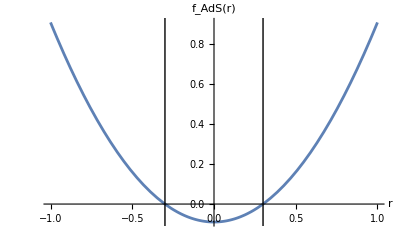

```mathematica
Plot[{f Ads[r] /. ValsCom},{r,-1,1},Epilog->({InfiniteLine[{{rH,0},{rH,1}}],InfiniteLine[{{-rH,0},{-rH,1}}] }/. ValsCom),AxesLabel->{"r","f_AdS(r)"}]
```

And so this is positive when as long as , so positive outside the horizon and negative inside it (Since r has interpretation of radial coordinate, it is non-negative). 
Doing the same for tortoise coordinates, need to run it through the transform functions to correctly plot as function of radial coordinate,

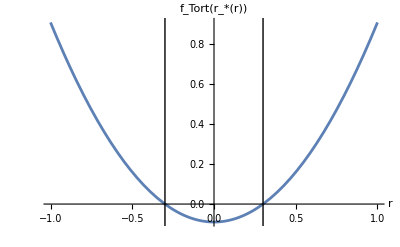

```mathematica
Plot[{f Tort[ToTort[r]] /. ValsCom},{r,-1,1},Epilog->({InfiniteLine[{{rH,0},{rH,1}}],InfiniteLine[{{-rH,0},{-rH,1}}] }/. ValsCom),AxesLabel->{"r","f_Tort(r_*(r))"}]
```

Which is exactly what we’d expect since they are the components of the metric, which should transform into each other. Doing this in the tortoise coordinate system itself,

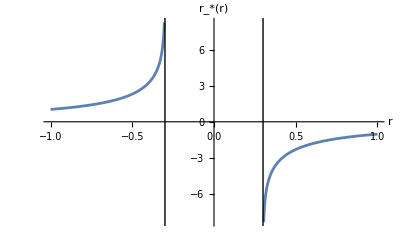

```mathematica
Plot[{ToTort[r] /. ValsCom},{r,-1,1},Epilog->({InfiniteLine[{{rH,0},{rH,1}}],InfiniteLine[{{-rH,0},{-rH,1}}] }/. ValsCom),AxesLabel->{"r","r_*(r)"}]
```

```mathematica
ToTort[rH] /. ValsCom
```

-∞

We see that the tortoise coordinate r_* is strictly negative, with smaller magnitude negative numbers corresponding to further away from the horizon, and the horizon itself existing at . Plotting this,

General::munfl: Csch[73425.8] is too small to represent as a normalized machine number; precision may be lost.

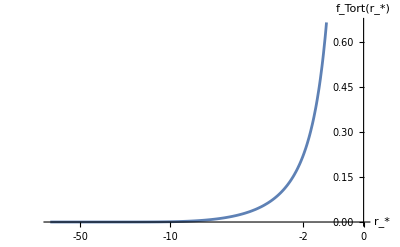

```mathematica
Plot[{f Tort[rs] /. ValsCom},{rs,-∞,0},(*Epilog->({InfiniteLine[{{rH,0},{rH,1}}],InfiniteLine[{{-rH,0},{-rH,1}}] }/. ValsCom),*)AxesLabel->{"r_*","f_Tort(r_*)"}]
```

As expected, f_Tort is still strictly positive. So regardless of our coordinate system, we can always say that the metric factors f,g are always positive, so long as we are outside the horizon. Using this, we can now look at that Explicit null condition:

```mathematica
rNullSol
```

{-∫_0^λ -(√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ],-∫_0^λ (√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ]}

Using these, we can solve to r[λ], take a derivative to obtain r’[λ], and filter to which of them has r’[λ]<0 with the above assumptions for f,g. This select the infalling branch, which is the one we are interested in.

```mathematica
Select[rNullSol,FullSimplify[(r'[λ]/.Flatten[D[Solve[#==0,r[λ]],λ]]) < 0,Assumptions->{f[r[λ]]>0,g[r[λ]]>0}]&]
```

{-∫_0^λ -(√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ]}

We can then just take the equation itself out of this list and store that as the branch we want.

```mathematica
rNullSolInfall =First[Select[rNullSol,FullSimplify[(r'[λ]/.Flatten[D[Solve[#==0,r[λ]],λ]]) < 0,Assumptions->{f[r[λ]]>0,g[r[λ]]>0}]&]]//FullSimplify
```

-∫_0^λ -(√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ]

Finally then, lets store all the equations we have in one place.

```mathematica
GeneralEqns = Association["LMm"->massiveELE,"LEi"->einbELE,"Geo"-> GeodesicResult,"NuE"->rNullSolInfall,"NuI"->nullCondStatic ]
```

<|LMm→{-(m r'[λ] (-f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)+2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2)),-(m t'[λ] (f[r[λ]] t'[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)-2 g[r[λ]] (t'[λ] (f'[r[λ]] r'[λ]^2-f[r[λ]] r''[λ])+f[r[λ]] r'[λ] t''[λ])))/(2 (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)^(3/2))},LEi→{((-f[r[λ]] e'[λ]+e[λ] f'[r[λ]] r'[λ]) t'[λ]+e[λ] f[r[λ]] t''[λ])/e[λ]^2,(-e[λ] (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2)+2 g[r[λ]] (e'[λ] r'[λ]-e[λ] r''[λ]))/(2 e[λ]^2)},Geo→{-f'[r[λ]] r'[λ] t'[λ]-f[r[λ]] t''[λ],1/2 (g'[r[λ]] r'[λ]^2+f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])},NuE→-∫_0^λ -(√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ],NuI→-f[r[λ]]+g[r[λ]] r'[λ]^2|>

NB: Remember that for the first three we have the (t(λ),r(λ))^μ EoM, while the final two are just a single equation for  as they have the static gauge  built in.

#### Einbein Considerations (Constraint Equations)

So we have the einbein constraint equation 3.6 that comes from the ELE method on L_einbein,

```mathematica
einbConstrELE
```

-(m^2 e[λ]^2+g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2)/(2 e[λ]^2)

Didn’t get a 2nd version from the MM, but ELE and MM always agree so that’s fine. We can generate two more versions from this one since we know this=0, can either just take the numerator or let MMA simplify it:

```mathematica
einbConstrNum = Numerator[einbConstrELE]
```

-m^2 e[λ]^2-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2

```mathematica
einbConstrMMAsimp=ZeroPart[einbConstrELE ==0 // FullSimplify]
```

(m^2 e[λ]^2+g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2)/e[λ]

Are these all the same or at least compatible?

```mathematica
ConstrEqns = {einbConstrELE,einbConstrNum,einbConstrMMAsimp};
ConstrEqnsNames= {"Raw","Numerator","MMA Simplify"};
```

```mathematica
Do[Do[If[i!=j,
Print[ConstrEqnsNames[[i]] <> " vs "<> ConstrEqnsNames[[j]] <>":"];
Factors[ConstrEqns[[i]]/.compValsM,ConstrEqns[[j]]/.compValsM]
]
,{j,1,i}],{i,1,3}]
```

Numerator vs Raw:

Diagreement by 2^1 23^2

MMA Simplify vs Raw:

Diagreement by (-1)^1 2^1 23^1

MMA Simplify vs Numerator:

Diagreement by (-1)^1/23^1

So in massive case, just have differences by overall factor of e(λ). In massless,

```mathematica
Do[Do[If[i!=j,
Print[ConstrEqnsNames[[i]] <> " vs "<> ConstrEqnsNames[[j]] <>":"];
Factors[ConstrEqns[[i]]/.compValsML,ConstrEqns[[j]]/.compValsML]
]
,{j,1,i}],{i,1,3}]
```

Numerator vs Raw:

Diagreement by 2^1 23^2

MMA Simplify vs Raw:

Diagreement by (-1)^1 2^1 23^1

MMA Simplify vs Numerator:

Diagreement by (-1)^1/23^1

Same thing. So these are technically slightly different equations, but since we should have e(λ) non-degenerate for all λ, they should all be equivalent. 
We can now take derivatives of each of these,

```mathematica
D[ConstrEqns,λ] // FullSimplify
```

{(-2 f[r[λ]] e'[λ] t'[λ]^2+2 g[r[λ]] r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+e[λ] (-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2+2 f[r[λ]] t'[λ] t''[λ]))/(2 e[λ]^3),-2 m^2 e[λ] e'[λ]-g'[r[λ]] r'[λ]^3+r'[λ] (f'[r[λ]] t'[λ]^2-2 g[r[λ]] r''[λ])+2 f[r[λ]] t'[λ] t''[λ],(e'[λ] (m^2 e[λ]^2-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)+e[λ] (g'[r[λ]] r'[λ]^3+r'[λ] (-f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])-2 f[r[λ]] t'[λ] t''[λ]))/e[λ]^2}

Now, are any of these the same if we let MMA set ==0 and simplify?

```mathematica
ConstrDerEqns = Join[D[ConstrEqns,λ],ZeroPart[#==0 // FullSimplify]& /@ (D[ConstrEqns,λ])]
```

{(e'[λ] (m^2 e[λ]^2+g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2))/e[λ]^3-(2 m^2 e[λ] e'[λ]+g'[r[λ]] r'[λ]^3-f'[r[λ]] r'[λ] t'[λ]^2+2 g[r[λ]] r'[λ] r''[λ]-2 f[r[λ]] t'[λ] t''[λ])/(2 e[λ]^2),-2 m^2 e[λ] e'[λ]-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2-2 g[r[λ]] r'[λ] r''[λ]+2 f[r[λ]] t'[λ] t''[λ],-(e'[λ] (m^2 e[λ]^2+g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2))/e[λ]^2+(2 m^2 e[λ] e'[λ]+g'[r[λ]] r'[λ]^3-f'[r[λ]] r'[λ] t'[λ]^2+2 g[r[λ]] r'[λ] r''[λ]-2 f[r[λ]] t'[λ] t''[λ])/e[λ],(-2 f[r[λ]] e'[λ] t'[λ]^2+2 g[r[λ]] r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+e[λ] (-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2+2 f[r[λ]] t'[λ] t''[λ]))/e[λ],2 m^2 e[λ] e'[λ]+g'[r[λ]] r'[λ]^3+r'[λ] (-f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])-2 f[r[λ]] t'[λ] t''[λ],m^2 e[λ] e'[λ]+g'[r[λ]] r'[λ]^3+(e'[λ] (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2))/e[λ]+r'[λ] (-f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])-2 f[r[λ]] t'[λ] t''[λ]}

```mathematica
ConstrDerEqnsNames = Join[ConstrEqnsNames, Map[#<> "Simp"&,ConstrEqnsNames]]
```

{Raw,Numerator,MMA Simplify,RawSimp,NumeratorSimp,MMA SimplifySimp}

```mathematica
ConstrEqns[[1]]
```

```mathematica
ConstrDerEqns[[1]]
ConstrDerEqns[[4]]
```

(e'[λ] (m^2 e[λ]^2+g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2))/e[λ]^3-(2 m^2 e[λ] e'[λ]+g'[r[λ]] r'[λ]^3-f'[r[λ]] r'[λ] t'[λ]^2+2 g[r[λ]] r'[λ] r''[λ]-2 f[r[λ]] t'[λ] t''[λ])/(2 e[λ]^2)

(-2 f[r[λ]] e'[λ] t'[λ]^2+2 g[r[λ]] r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+e[λ] (-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2+2 f[r[λ]] t'[λ] t''[λ]))/e[λ]

```mathematica
Do[Do[If[i!=j,
Print[ConstrDerEqnsNames[[i]] <> " vs "<> ConstrDerEqnsNames[[j]] <>":"];
Factors[ConstrDerEqns[[i]]/.compValsM,ConstrDerEqns[[j]]/.compValsM]
]
,{j,1,i}],{i,1,6}]
```

Numerator vs Raw:

Diagreement by (5^1 23^3 7879^1)/418799^1

MMA Simplify vs Raw:

Diagreement by ((-1)^1 23^1 29^1 60127^1)/(2^1 418799^1)

MMA Simplify vs Numerator:

Diagreement by ((-1)^1 29^1 60127^1)/(2^1 5^1 23^2 7879^1)

RawSimp vs Raw:

Diagreement by 2^1 23^2

RawSimp vs Numerator:

Diagreement by (2^1 418799^1)/(5^1 23^1 7879^1)

RawSimp vs MMA Simplify:

Diagreement by ((-1)^1 2^2 23^1 418799^1)/(29^1 60127^1)

NumeratorSimp vs Raw:

Diagreement by ((-1)^1 5^1 23^3 7879^1)/418799^1

NumeratorSimp vs Numerator:

Agrees up to non-zero factor of -1

NumeratorSimp vs MMA Simplify:

Diagreement by (2^1 5^1 23^2 7879^1)/(29^1 60127^1)

NumeratorSimp vs RawSimp:

Diagreement by ((-1)^1 5^1 23^1 7879^1)/(2^1 418799^1)

MMA SimplifySimp vs Raw:

Diagreement by ((-1)^1 23^2 29^1 60127^1)/(2^1 418799^1)

MMA SimplifySimp vs Numerator:

Diagreement by ((-1)^1 29^1 60127^1)/(2^1 5^1 23^1 7879^1)

MMA SimplifySimp vs MMA Simplify:

Diagreement by 23^1

MMA SimplifySimp vs RawSimp:

Diagreement by ((-1)^1 29^1 60127^1)/(2^2 418799^1)

MMA SimplifySimp vs NumeratorSimp:

Diagreement by (29^1 60127^1)/(2^1 5^1 23^1 7879^1)

So looks like each one agrees with its own simplified version up to factors of e(λ), but different versions don’t agree at all.

```mathematica
Do[Do[If[i!=j,
Print[ConstrDerEqnsNames[[i]] <> " vs "<> ConstrDerEqnsNames[[j]] <>":"];
Factors[ConstrDerEqns[[i]]/.compValsML,ConstrDerEqns[[j]]/.compValsML]
]
,{j,1,i}],{i,1,6}]
```

Numerator vs Raw:

Diagreement by (2^4 3^1 11^1 23^3 73^1)/418799^1

MMA Simplify vs Raw:

Diagreement by ((-1)^1 5^1 23^1 172411^1)/418799^1

MMA Simplify vs Numerator:

Diagreement by ((-1)^1 5^1 172411^1)/(2^4 3^1 11^1 23^2 73^1)

RawSimp vs Raw:

Diagreement by 2^1 23^2

RawSimp vs Numerator:

Diagreement by 418799^1/(2^3 3^1 11^1 23^1 73^1)

RawSimp vs MMA Simplify:

Diagreement by ((-1)^1 2^1 23^1 418799^1)/(5^1 172411^1)

NumeratorSimp vs Raw:

Diagreement by ((-1)^1 2^4 3^1 11^1 23^3 73^1)/418799^1

NumeratorSimp vs Numerator:

Agrees up to non-zero factor of -1

NumeratorSimp vs MMA Simplify:

Diagreement by (2^4 3^1 11^1 23^2 73^1)/(5^1 172411^1)

NumeratorSimp vs RawSimp:

Diagreement by ((-1)^1 2^3 3^1 11^1 23^1 73^1)/418799^1

MMA SimplifySimp vs Raw:

Diagreement by ((-1)^1 5^1 23^2 172411^1)/418799^1

MMA SimplifySimp vs Numerator:

Diagreement by ((-1)^1 5^1 172411^1)/(2^4 3^1 11^1 23^1 73^1)

MMA SimplifySimp vs MMA Simplify:

Diagreement by 23^1

MMA SimplifySimp vs RawSimp:

Diagreement by ((-1)^1 5^1 172411^1)/(2^1 418799^1)

MMA SimplifySimp vs NumeratorSimp:

Diagreement by (5^1 172411^1)/(2^4 3^1 11^1 23^1 73^1)

Same thing in the massless case. So this leaves us with 3 constraint equations, and 5 constraint derivatives (since Numerator and Numerator simplified are just different by a sign):

```mathematica
EinConstr = {einbConstrELE,einbConstrNum,einbConstrMMAsimp} // FullSimplify
```

{-(m^2 e[λ]^2+g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2)/(2 e[λ]^2),-m^2 e[λ]^2-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2,(m^2 e[λ]^2+g[r[λ]] r'[λ]^2-f[r[λ]] t'[λ]^2)/e[λ]}

```mathematica
EinConstrD =Join[D[ConstrEqns,λ],Map[ZeroPart[#==0 // FullSimplify]& , D[Delete[ConstrEqns,2],λ]]]// FullSimplify
```

{(-2 f[r[λ]] e'[λ] t'[λ]^2+2 g[r[λ]] r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+e[λ] (-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2+2 f[r[λ]] t'[λ] t''[λ]))/(2 e[λ]^3),-2 m^2 e[λ] e'[λ]-g'[r[λ]] r'[λ]^3+r'[λ] (f'[r[λ]] t'[λ]^2-2 g[r[λ]] r''[λ])+2 f[r[λ]] t'[λ] t''[λ],(e'[λ] (m^2 e[λ]^2-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)+e[λ] (g'[r[λ]] r'[λ]^3+r'[λ] (-f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])-2 f[r[λ]] t'[λ] t''[λ]))/e[λ]^2,(-2 f[r[λ]] e'[λ] t'[λ]^2+2 g[r[λ]] r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+e[λ] (-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2+2 f[r[λ]] t'[λ] t''[λ]))/e[λ],m^2 e[λ] e'[λ]+g'[r[λ]] r'[λ]^3+(e'[λ] (-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2))/e[λ]+r'[λ] (-f'[r[λ]] t'[λ]^2+2 g[r[λ]] r''[λ])-2 f[r[λ]] t'[λ] t''[λ]}

```mathematica
Do[Do[If[i!=j,
Print[ToString[i]<> " vs "<> ToString[j] <>":"];
Factors[EinConstrD[[i]]/.compValsML,EinConstrD[[j]]/.compValsML]
]
,{j,1,i}],{i,1,5}]
```

2 vs 1:

Diagreement by (2^4 3^1 11^1 23^3 73^1)/418799^1

3 vs 1:

Diagreement by ((-1)^1 5^1 23^1 172411^1)/418799^1

3 vs 2:

Diagreement by ((-1)^1 5^1 172411^1)/(2^4 3^1 11^1 23^2 73^1)

4 vs 1:

Diagreement by 2^1 23^2

4 vs 2:

Diagreement by 418799^1/(2^3 3^1 11^1 23^1 73^1)

4 vs 3:

Diagreement by ((-1)^1 2^1 23^1 418799^1)/(5^1 172411^1)

5 vs 1:

Diagreement by ((-1)^1 5^1 23^2 172411^1)/418799^1

5 vs 2:

Diagreement by ((-1)^1 5^1 172411^1)/(2^4 3^1 11^1 23^1 73^1)

5 vs 3:

Diagreement by 23^1

5 vs 4:

Diagreement by ((-1)^1 5^1 172411^1)/(2^1 418799^1)

#### Initial Conditions

Still need to sort out initial conditions for the cases where we don’t already have, and also need einbein IC. Currently, have IC for t(λ),t’(λ),r(λ), and r’(λ) only in the massive case. 
In the massless case, our r’(λ=0) is constrained by our choice of t’(λ=0) since we need to be on a null geodesic at λ=0. So

```mathematica
Solve[((nullCond /.ToIC) /. ValsCom) == 0,rpi]
```

{{rpi→-(√f[ri])/(√g[ri])},{rpi→(√f[ri])/(√g[ri])}}

Again have two branches, so we need to pick. Since this initial condition, lets assume we outside the horizon (), which means that , at least for our cases of f,g. Thus, if we want the infalling trajectory, we need the branch with the negative sign.

```mathematica
Flatten[Solve[((nullCond /.ToIC) /. ValsCom) == 0,rpi]][[1]]
```

rpi→-(√f[ri])/(√g[ri])

```mathematica
AppendTo[rpIC,"Massless"->Flatten[Solve[((nullCond /.ToIC) /. ValsCom) == 0,rpi]][[1]]]
```

<|Massive→rpi→0,Massless→rpi→-(√f[ri])/(√g[ri])|>

We now need initial conditions for the einbein e(λ). Lets consider how our equations look at the λ=0 instant

```mathematica
InitialConstr=(Thread[EinConstr==ConstantArray[0,Length[EinConstr]]] /. ToIC) /. ValsCom // FullSimplify
```

{(m^2 e[0]^2-f[ri]+rpi^2 g[ri])/e[0]==0,m^2 e[0]^2+rpi^2 g[ri]==f[ri],(m^2 e[0]^2-f[ri]+rpi^2 g[ri])/e[0]==0}

```mathematica
InitialConstrD=(Thread[EinConstrD==ConstantArray[0,Length[EinConstrD]]] /. ToIC) /. ValsCom // FullSimplify
```

{rpi^3 g'[ri]+2 rpi g[ri] (-(rpi e'[0])/e[0]+r''[0])+f[ri] ((2 e'[0])/e[0]-2 t''[0])==rpi f'[ri],2 m^2 e[0] e'[0]+rpi^3 g'[ri]+2 rpi g[ri] r''[0]==rpi f'[ri]+2 f[ri] t''[0],m^2 e[0] e'[0]+rpi^3 g'[ri]+rpi g[ri] (-(rpi e'[0])/e[0]+2 r''[0])+f[ri] (e'[0]/e[0]-2 t''[0])==rpi f'[ri],rpi^3 g'[ri]+2 rpi g[ri] (-(rpi e'[0])/e[0]+r''[0])+f[ri] ((2 e'[0])/e[0]-2 t''[0])==rpi f'[ri],m^2 e[0] e'[0]+((f[ri]-rpi^2 g[ri]) e'[0])/e[0]+rpi^3 g'[ri]+2 rpi g[ri] r''[0]==rpi f'[ri]+2 f[ri] t''[0]}

```mathematica
{InitialConstr,InitialConstrD} //. Flatten[{m->mass,ValsCom,rpIC["Massive"]}]// FullSimplify
```

{{e[0]==f[ri]/e[0],e[0]^2==f[ri],e[0]==f[ri]/e[0]},{f[ri] (-e'[0]/e[0]+t''[0])==0,e[0] e'[0]==f[ri] t''[0],((e[0]^2+f[ri]) e'[0])/e[0]==2 f[ri] t''[0],f[ri] (-e'[0]/e[0]+t''[0])==0,((e[0]^2+f[ri]) e'[0])/e[0]==2 f[ri] t''[0]}}

```mathematica
{InitialConstr,InitialConstrD} //. Flatten[{m->0,ValsCom,rpIC["Massless"]}]// FullSimplify
```

{{True,True,True},{(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0}}

Notice now we have some conditions we can apply at λ=0. In the massive case, the constraint equation(s) fixes , and so . However, in the massless case the constraint equations are trivially satisfied, so we don’t get any more information. Let’s now take this condition on e(0) in the massive case and see if it says anything about e’(0)?

```mathematica
{InitialConstr,InitialConstrD} //. Flatten[{m->mass,ValsCom,rpIC["Massive"],e[0]->-√f[ri]}]// FullSimplify
```

{{True,True,True},{√f[ri] e'[0]+f[ri] t''[0]==0,√f[ri] e'[0]+f[ri] t''[0]==0,√f[ri] e'[0]+f[ri] t''[0]==0,√f[ri] e'[0]+f[ri] t''[0]==0,√f[ri] e'[0]+f[ri] t''[0]==0}}

Obviously the constraint equations are now satisfied, but notice all the constraint derivatives simplify to the same thing, . So this IC on e that the massive case fixes doesn’t fix e’(0), only its relation to t’’(0).

Also, notice that the initial instant in the massless case has eliminated the einbein completely, so do we even need IC for the einbein in this case? Surely we do since its still present in the actual EoM, maybe this just means any IC are valid here?
The constraint equations useless in massless case, since

```mathematica
InitialConstr /. rpIC["Massless"]// FullSimplify
```

{m e[0]==0,m e[0]==0,m e[0]==0}

They just imply m=0 or e(0)=0, and we know m=0 so nothing useful. Looking at just the constraint derivatives then

```mathematica
InitialConstrD /. rpIC["Massless"]// FullSimplify
```

{(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,2 m^2 e[0] e'[0]+(√f[ri] (-f[ri] g'[ri]+g[ri] (f'[ri]-2 g[ri] r''[0])))/g[ri]^(3/2)==2 f[ri] t''[0],m^2 e[0] e'[0]+(√f[ri] (-f[ri] g'[ri]+g[ri] (f'[ri]-2 g[ri] r''[0])))/g[ri]^(3/2)==2 f[ri] t''[0],(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,m^2 e[0] e'[0]+(√f[ri] (-f[ri] g'[ri]+g[ri] (f'[ri]-2 g[ri] r''[0])))/g[ri]^(3/2)==2 f[ri] t''[0]}

Looks promising, but all the einbeins are next to m’s, so when we do massless properly,

```mathematica
InitialConstrD /. {m->0,rpIC["Massless"]}// FullSimplify
```

{(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0,(√f[ri] (-g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])+2 f[ri] g[ri] t''[0]==0}

Einbein is gone again, so yeah looks like none of these equations constrain e(0) or e’(0) for massless case. Let’s try something else, starting with the raw constraint equation we can solve for the einbein

```mathematica
Solve[EinConstr[[1]] ==0,e[λ]]
```

{{e[λ]→-(√(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2))/m},{e[λ]→(√(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2))/m}}

This now gives us two branches we’d need to pick from. However, lets instead try

```mathematica
Solve[(EinConstr[[1]]  //. e[λ] -> Sqrt[e2])==0,e2]
```

{{e2→(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)/m^2}}

Giving us three equations for the einbein:

```mathematica
einbSolv = {
e[λ] == (e[λ]/.Solve[EinConstr[[1]] ==0,e[λ]][[1]] ),
e[λ] == (e[λ]/.Solve[EinConstr[[1]] ==0,e[λ]][[2]] ),
e[λ]^2 == (e2/.Flatten[Solve[(EinConstr[[1]]  //. e[λ] -> Sqrt[e2])==0,e2] ])
}
```

{e[λ]==-(√(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2))/m,e[λ]==(√(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2))/m,e[λ]^2==(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)/m^2}

Which we can then take a derivative of,

```mathematica
einbSolvD=D[einbSolv,λ]
```

{e'[λ]==-(-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2-2 g[r[λ]] r'[λ] r''[λ]+2 f[r[λ]] t'[λ] t''[λ])/(2 m √(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)),e'[λ]==(-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2-2 g[r[λ]] r'[λ] r''[λ]+2 f[r[λ]] t'[λ] t''[λ])/(2 m √(-g[r[λ]] r'[λ]^2+f[r[λ]] t'[λ]^2)),2 e[λ] e'[λ]==(-g'[r[λ]] r'[λ]^3+f'[r[λ]] r'[λ] t'[λ]^2-2 g[r[λ]] r'[λ] r''[λ]+2 f[r[λ]] t'[λ] t''[λ])/m^2}

We can then convert this to IC in massive and massless cases. If massless though, everything breaks due to the m in denominator. So can only really consider massive case.

```mathematica
einbSolvD//. Flatten[{ToIC, ValsCom,rpIC["Massive"]}]
```

{e'[0]==-(√f[ri] t''[0])/m,e'[0]==(√f[ri] t''[0])/m,2 e[0] e'[0]==(2 f[ri] t''[0])/m^2}

Can see we just getting same relation between e’ and t’’ as before. So we have two possible IC for e(0) in the massive case, and nothing else. Think the IC for e’(0) is less important in massive since have that fixed relation between e’ and t’’, but that might exactly cause the issue.

```mathematica
{EinConstr,EinConstrD} //. Flatten[{m->0,ToIC,rpIC[["Massless"]]}] // FullSimplify
```

{{((-1+tpi^2) f[ri])/(2 e[0]^2),(-1+tpi^2) f[ri],-((-1+tpi^2) f[ri])/e[0]},{(e[0] f[ri]^(3/2) g'[ri]+e[0] √f[ri] g[ri] (-tpi^2 f'[ri]+2 g[ri] r''[0])+2 f[ri] g[ri]^(3/2) (-((-1+tpi^2) e'[0])+tpi e[0] t''[0]))/(2 e[0]^3 g[ri]^(3/2)),(√f[ri] (-tpi^2 g[ri] f'[ri]+f[ri] g'[ri]+2 g[ri]^2 r''[0]))/g[ri]^(3/2)+2 tpi f[ri] t''[0],(-e[0] f[ri]^(3/2) g'[ri]+e[0] √f[ri] g[ri] (tpi^2 f'[ri]-2 g[ri] r''[0])+f[ri] g[ri]^(3/2) ((-1+tpi^2) e'[0]-2 tpi e[0] t''[0]))/(e[0]^2 g[ri]^(3/2)),(f[ri]^(3/2) g'[ri])/g[ri]^(3/2)+(√f[ri] (-tpi^2 f'[ri]+2 g[ri] r''[0]))/(√g[ri])+2 f[ri] (-((-1+tpi^2) e'[0])/e[0]+tpi t''[0]),-(f[ri]^(3/2) g'[ri])/g[ri]^(3/2)+(√f[ri] (tpi^2 f'[ri]-2 g[ri] r''[0]))/(√g[ri])+f[ri] (((-1+tpi^2) e'[0])/e[0]-2 tpi t''[0])}}

```mathematica
% /. tpi ->0
```

{{-f[ri]/(2 e[0]^2),-f[ri],f[ri]/e[0]},{(2 f[ri] g[ri]^(3/2) e'[0]+e[0] f[ri]^(3/2) g'[ri]+2 e[0] √f[ri] g[ri]^2 r''[0])/(2 e[0]^3 g[ri]^(3/2)),(√f[ri] (f[ri] g'[ri]+2 g[ri]^2 r''[0]))/g[ri]^(3/2),(-f[ri] g[ri]^(3/2) e'[0]-e[0] f[ri]^(3/2) g'[ri]-2 e[0] √f[ri] g[ri]^2 r''[0])/(e[0]^2 g[ri]^(3/2)),(2 f[ri] e'[0])/e[0]+(f[ri]^(3/2) g'[ri])/g[ri]^(3/2)+2 √f[ri] √g[ri] r''[0],-(f[ri] e'[0])/e[0]-(f[ri]^(3/2) g'[ri])/g[ri]^(3/2)-2 √f[ri] √g[ri] r''[0]}}

```mathematica
% //(Thread[Flatten[#]==ConstantArray[0,Length[Flatten[#]]]]//FullSimplify)&
```

{f[ri]/e[0]==0,f[ri]==0,f[ri]/e[0]==0,(2 f[ri] g[ri] e'[0])/e[0]+(f[ri]^(3/2) g'[ri])/(√g[ri])+2 √f[ri] g[ri]^(3/2) r''[0]==0,(√f[ri] (f[ri] g'[ri]+2 g[ri]^2 r''[0]))/(√g[ri])==0,(f[ri] g[ri] e'[0])/e[0]+(f[ri]^(3/2) g'[ri])/(√g[ri])+2 √f[ri] g[ri]^(3/2) r''[0]==0,(2 f[ri] e'[0])/e[0]+(f[ri]^(3/2) g'[ri])/g[ri]^(3/2)+2 √f[ri] √g[ri] r''[0]==0,(f[ri] e'[0])/e[0]+(f[ri]^(3/2) g'[ri])/g[ri]^(3/2)+2 √f[ri] √g[ri] r''[0]==0}

So the most we can say is that we have the following options for potential ICs:

```mathematica
potentialEPICs = {epi->0,epi->1,epi->-1};
potentialMEICs = {ei-> Sqrt[f[ri]],ei-> -Sqrt[f[ri]]};
potentialMlEICs = {ei->0,ei->1,ei->-1};
```

### Specific case Equations

Here we will replace the f,g functions to specify the spacetime we are working in, and generate all the different variants of different equations and IC (where applicable). For some reason, can’t just apply replacement rules to the whole association, so need special function defined in the Helper Functions section

#### Flat Spacetime

```mathematica
FlatSpaceRawEqns=SpecifyST[GeneralEqns,FlatSpacer]
```

<|LMm→{-(m r'[λ] (-t'[λ] r''[λ]+r'[λ] t''[λ]))/((-r'[λ]^2+t'[λ]^2)^(3/2)),(m t'[λ] (-t'[λ] r''[λ]+r'[λ] t''[λ]))/((-r'[λ]^2+t'[λ]^2)^(3/2))},LEi→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2},Geo→{-t''[λ],r''[λ]},NuE→λ-r[0]+r[λ],NuI→-1+r'[λ]^2|>

Firstly, the null conditions need some care as they are different to the others. The explicit method just hands us a solution already, while Implicit method still uses NDSolve but just doesn’t need to solve for t[λ], so also needs to be handled separately. Additionally NDSolve will find both branches, so lets also select the infalling one here by taking the one that has a negative change in the r coordinate as λ goes 0 → 1

```mathematica
FlatSpecials=<|"NuE"->eNullSolve[FlatSpaceRawEqns["NuE"],rIC["Standard"]], "NuI"->iNullSolve[FlatSpaceRawEqns["NuI"],rIC["Standard"]]|>
```

<|NuE→{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,NuE: Manual explicit null method}},NuI→{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,NuI: Manual implicit null method}}|>

Note these are both full final solutions which should be plottable, and also are only valid for massless cases.
Next, let us sort out the massive and massless non-einbein equations

```mathematica
(*First massive*)
FlatMnonEeqns=genEqnsNE[FlatSpaceRawEqns,"Flat",True,{"Geo","LMm"}]
```

<|GeoM→{-t''[λ]==0,r''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1},LMmM→{-(r'[λ] (-t'[λ] r''[λ]+r'[λ] t''[λ]))/((-r'[λ]^2+t'[λ]^2)^(3/2))==0,(t'[λ] (-t'[λ] r''[λ]+r'[λ] t''[λ]))/((-r'[λ]^2+t'[λ]^2)^(3/2))==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}|>

```mathematica
(*Then massless*)
FlatMlnonEeqns=genEqnsNE[FlatSpaceRawEqns,"Flat",False,{"Geo"}]
```

<|GeoMl→{-t''[λ]==0,r''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1}|>

Einbein ones are now gonna need more consideration as we need to worry about both which constraint equations (or derivatives of same) to use, as well as what initial conditions to use. Lets use the naming convention
“Ec1d0e2ep0”
for the different arrangements of equations and IC we can use, where number is which one it is in the above lists and 0 denotes that option isn’t being used, as explained in Appendix B.3

```mathematica
(*Massive first*)
FlatMEeqns = genEqnsE[FlatSpaceRawEqns["LEi"],"Flat",True,False,True,True,False]
```

<|Ec0d1e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d1e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1},Ec0d2e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 e[λ] e'[λ]-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d2e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 e[λ] e'[λ]-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1},Ec0d3e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (e[λ]^2-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d3e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (e[λ]^2-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1},Ec0d4e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d4e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1},Ec0d5e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,e[λ] e'[λ]+(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d5e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,e[λ] e'[λ]+(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1}|>

```mathematica
(*And Massless*)
FlatMlEeqns = genEqnsE[FlatSpaceRawEqns["LEi"],"Flat",False,False,True,True,False]
```

<|Ec0d1e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d1e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d1e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1},Ec0d2e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d2e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d2e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1},Ec0d3e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d3e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d3e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1},Ec0d4e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d4e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d4e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1},Ec0d5e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d5e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d5e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1}|>

Finally, we can then store all these different variants together (along with the special cases) so we can solve them later

```mathematica
FlatSpaceEqns=<| "Specials"-> FlatSpecials,"MnE"-> FlatMnonEeqns, "MlnE"->FlatMlnonEeqns,"ME"->FlatMEeqns,"MlE"-> FlatMlEeqns|>
```

<|Specials→<|NuE→{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,NuE: Manual explicit null method}},NuI→{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,NuI: Manual implicit null method}}|>,MnE→<|GeoM→{-t''[λ]==0,r''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1},LMmM→{-(r'[λ] (-t'[λ] r''[λ]+r'[λ] t''[λ]))/((-r'[λ]^2+t'[λ]^2)^(3/2))==0,(t'[λ] (-t'[λ] r''[λ]+r'[λ] t''[λ]))/((-r'[λ]^2+t'[λ]^2)^(3/2))==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}|>,MlnE→<|GeoMl→{-t''[λ]==0,r''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1}|>,ME→<|Ec0d1e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d1e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1},Ec0d2e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 e[λ] e'[λ]-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d2e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 e[λ] e'[λ]-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1},Ec0d3e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (e[λ]^2-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d3e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (e[λ]^2-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1},Ec0d4e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d4e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1},Ec0d5e1ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,e[λ] e'[λ]+(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==1},Ec0d5e2ep0M→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,e[λ] e'[λ]+(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1,e[0]==-1}|>,MlE→<|Ec0d1e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d1e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d1e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/(2 e[λ]^3)==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1},Ec0d2e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d2e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d2e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,-2 r'[λ] r''[λ]+2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1},Ec0d3e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d3e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d3e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2)+e[λ] (2 r'[λ] r''[λ]-2 t'[λ] t''[λ]))/e[λ]^2==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1},Ec0d4e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d4e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d4e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(-2 e'[λ] t'[λ]^2+2 r'[λ] (e'[λ] r'[λ]-e[λ] r''[λ])+2 e[λ] t'[λ] t''[λ])/e[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1},Ec0d5e1ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==0},Ec0d5e2ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==1},Ec0d5e3ep0Ml→{(-e'[λ] t'[λ]+e[λ] t''[λ])/e[λ]^2==0,(e'[λ] r'[λ]-e[λ] r''[λ])/e[λ]^2==0,(e'[λ] (-r'[λ]^2+t'[λ]^2))/e[λ]+2 r'[λ] r''[λ]-2 t'[λ] t''[λ]==0,r[0]==1,t[0]==0,r'[0]==-1,t'[0]==1,e[0]==-1}|>|>

#### AdS Spacetime & coords

```mathematica
AdsRawEqns=SpecifyST[GeneralEqns,AdsCrdr]
```

<|LMm→{(m r'[λ] (t'[λ] (r[λ] (3 l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (rH^2-r[λ]^2) r''[λ])+l^4 (-rH^2+r[λ]^2) r'[λ] t''[λ]))/(l^4 (rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2)),(m t'[λ] (t'[λ] (r[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (-rH^2+r[λ]^2) r''[λ])+l^4 (rH^2-r[λ]^2) r'[λ] t''[λ]))/(l^4 (rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))},LEi→{(((rH^2-r[λ]^2) e'[λ]+2 e[λ] r[λ] r'[λ]) t'[λ]+e[λ] (-rH^2+r[λ]^2) t''[λ])/(l^2 e[λ]^2),(e[λ] r[λ] ((l^4 r'[λ]^2)/((rH^2-r[λ]^2)^2)-t'[λ]^2)+(l^4 (e'[λ] r'[λ]-e[λ] r''[λ]))/(-rH^2+r[λ]^2))/(l^2 e[λ]^2)},Geo→{(-2 r[λ] r'[λ] t'[λ]+(rH^2-r[λ]^2) t''[λ])/l^2,(r[λ] (-(l^4 r'[λ]^2)/((rH^2-r[λ]^2)^2)+t'[λ]^2))/l^2+(l^2 r''[λ])/(-rH^2+r[λ]^2)},NuE→-∫_0^λ -√(l^2/(-rH^2+r[Λ]^2)) ((-rH^2+r[Λ]^2)/l^2)^(3/2)ⅆΛ-r[0]+r[λ],NuI→(rH^2-r[λ]^2+(l^4 r'[λ]^2)/(-rH^2+r[λ]^2))/l^2|>

```mathematica
AdsSpecials=<|"NuE"->eNullSolve[AdsRawEqns["NuE"]// FullSimplify[#,Assumptions->{r[Λ]^2>rH^2,l>0}]&,Append[ValsCom,rIC["Standard"]]], "NuI"->iNullSolve[AdsRawEqns["NuI"],rIC["Standard"]]|>
```

NDSolve::ndsz: At λ == 1.03173, step size is effectively zero; singularity or stiff system suspected.

<|NuE→{{t→Function[λ,λ],r→Function[λ,1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ]},{False,NuE: Manual explicit null method}},NuI→{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,NuI: Manual implicit null method}}|>

Notice the Explicit method fails here, MMA can’t handle that integral equation:

```mathematica
Module[{eqn=r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ},
EchoEvaluation/@{DSolve[eqn,r,λ],
DSolve[eqn,r,{λ,0,10}],
DSolveValue[eqn,r,λ],
DSolveValue[eqn,r,{λ,0,10}],
NDSolve[eqn,r,{λ,0,10}],
NDSolveValue[eqn,r,{λ,0,10}],
DSolve[eqn,r[λ],λ],
DSolve[eqn,r[λ],{λ,0,10}],
DSolveValue[eqn,r[λ],λ],
DSolveValue[eqn,r[λ],{λ,0,10}],
NDSolve[eqn,r[λ],{λ,0,10}],
NDSolveValue[eqn,r[λ],{λ,0,10}],
NSolve[eqn,r[λ]],
NSolve[eqn,r],
FindRoot[eqn,{λ,1}]
}
]
```

NDSolve::derivs: No derivatives of dependent variables were found in the equations. NDSolve is designed to solve differential or differential algebraic equations. Use NSolve or FindRoot to numerically solve algebraic equations.

NDSolveValue::derivs: No derivatives of dependent variables were found in the equations. NDSolveValue is designed to solve differential or differential algebraic equations. Use NSolve or FindRoot to numerically solve algebraic equations.

NDSolve::derivs: No derivatives of dependent variables were found in the equations. NDSolve is designed to solve differential or differential algebraic equations. Use NSolve or FindRoot to numerically solve algebraic equations.

NDSolveValue::derivs: No derivatives of dependent variables were found in the equations. NDSolveValue is designed to solve differential or differential algebraic equations. Use NSolve or FindRoot to numerically solve algebraic equations.

NIntegrate::inumr: The integrand 0.09-r[Λ]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindRoot::nlnum: The function value {-1.-1. NIntegrate[0.09-r[«1»]^2,{Λ,0,1.}]+r[1.]} is not a list of numbers with dimensions {1} at {λ} = {1.}.

DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,λ]

DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,λ]

DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}]

DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}]

DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,λ]

DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,λ]

DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}]

DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}]

NDSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}]

NDSolve::derivs: No derivatives of dependent variables were found in the equations. NDSolve is designed to solve differential or differential algebraic equations. Use NSolve or FindRoot to numerically solve algebraic equations.

General::stop: Further output of NDSolve::derivs will be suppressed during this calculation.

NDSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}]

NDSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}]

NDSolveValue::derivs: No derivatives of dependent variables were found in the equations. NDSolveValue is designed to solve differential or differential algebraic equations. Use NSolve or FindRoot to numerically solve algebraic equations.

General::stop: Further output of NDSolveValue::derivs will be suppressed during this calculation.

NDSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}]

DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],λ]

DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],λ]

DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}]

DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}]

DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],λ]

DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],λ]

DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}]

DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}]

NDSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}]

NDSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}]

NDSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}]

NDSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}]

{{r[λ]→1.+1. ∫_0^λ (0.09-r[Λ]^2)ⅆΛ}}

{{r[λ]→1.+1. ∫_0^λ (0.09-r[Λ]^2)ⅆΛ}}

{}

{}

FindRoot[eqn$1274589,{λ,1}]

FindRoot::nlnum: The function value {-1.-1. NIntegrate[0.09-r[«1»]^2,{Λ,0,1.}]+r[1.]} is not a list of numbers with dimensions {1} at {λ} = {1.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot[eqn$1274589,{λ,1}]

{DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,λ],DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}],DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,λ],DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}],NDSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}],NDSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r,{λ,0,10}],DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],λ],DSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}],DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],λ],DSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}],NDSolve[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}],NDSolveValue[r[λ]==1+∫_0^λ (0.09-r[Λ]^2)ⅆΛ,r[λ],{λ,0,10}],{{r[λ]→1.+1. ∫_0^λ (0.09-r[Λ]^2)ⅆΛ}},{},FindRoot[eqn$1274589,{λ,1}]}

```mathematica
AdsMnonEeqns=genEqnsNE[AdsRawEqns,"AdS",True,{"Geo","LMm"}]
```

<|GeoM→{-2 r[λ] r'[λ] t'[λ]+(0.09-r[λ]^2) t''[λ]==0,r[λ] (-r'[λ]^2/((0.09-r[λ]^2)^2)+t'[λ]^2)+r''[λ]/(-0.09+r[λ]^2)==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1},LMmM→{(r'[λ] (t'[λ] (r[λ] (3 r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)+(0.09-r[λ]^2) r''[λ])+(-0.09+r[λ]^2) r'[λ] t''[λ]))/((0.09-r[λ]^2) ((r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)/(0.09-r[λ]^2))^(3/2))==0,(t'[λ] (t'[λ] (r[λ] (-3 r'[λ]^2+(0.09-r[λ]^2)^2 t'[λ]^2)+(-0.09+r[λ]^2) r''[λ])+(0.09-r[λ]^2) r'[λ] t''[λ]))/((0.09-r[λ]^2) ((r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)/(0.09-r[λ]^2))^(3/2))==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}|>

```mathematica
AdsMlnonEeqns=genEqnsNE[AdsRawEqns,"AdS",False,{"Geo"}]
```

<|GeoMl→{-2 r[λ] r'[λ] t'[λ]+(0.09-r[λ]^2) t''[λ]==0,r[λ] (-r'[λ]^2/((0.09-r[λ]^2)^2)+t'[λ]^2)+r''[λ]/(-0.09+r[λ]^2)==0,r[0]==1,t[0]==0,r'[0]==-0.91,t'[0]==1}|>

For the einbein ones, we want all the different arrangements of einbein constraints and initial conditions. We know we can’t have both constraint and derivative of constraint equations as then the system would be over determined. Technically this means we should only need one IC, but lets run with both as well, maybe it’ll help? Can always filter them out later.

```mathematica
(*Massive first*)
AdsMEeqns = genEVariants[AdsRawEqns["LEi"],"AdS",True]
```

```mathematica
(*And Massless*)
AdsMlEeqns = genEVariants[AdsRawEqns["LEi"],"AdS",False]
```

Finally, we can then store all these different variants together (along with the special cases) so we can solve them later

```mathematica
AdsEqns=<| "Specials"-> AdsSpecials,"MnE"-> AdsMnonEeqns, "MlnE"->AdsMlnonEeqns,"ME"->AdsMEeqns,"MlE"-> AdsMlEeqns|>
```

Sometimes has issues solving these as is, lets fully simplify everything with some assumptions. Storing separately so we can see if it gives anything different.

```mathematica
AdsEqns2=Map[FullSimplify[#,Assumptions->{((f Ads[r[λ]] /. ValsCom)>0), r[λ]>0}]&,AdsEqns,{2}]
```

#### Tort coords

```mathematica
TortRawEqns=SpecifyST[GeneralEqns,TortCrdr]
```

<|LMm→{-(m rH^4 Csch[(rH r[λ])/l^2]^4 r'[λ] (t'[λ] (rH Coth[(rH r[λ])/l^2] (-r'[λ]^2+t'[λ]^2)-l^2 r''[λ])+l^2 r'[λ] t''[λ]))/(l^6 ((rH^2 Csch[(rH r[λ])/l^2]^2 (-r'[λ]^2+t'[λ]^2))/l^2)^(3/2)),(m rH^4 Csch[(rH r[λ])/l^2]^4 t'[λ] (t'[λ] (rH Coth[(rH r[λ])/l^2] (-r'[λ]^2+t'[λ]^2)-l^2 r''[λ])+l^2 r'[λ] t''[λ]))/(l^6 ((rH^2 Csch[(rH r[λ])/l^2]^2 (-r'[λ]^2+t'[λ]^2))/l^2)^(3/2))},LEi→{(rH^2 Csch[(rH r[λ])/l^2]^2 (-((l^2 e'[λ]+2 rH Coth[(rH r[λ])/l^2] e[λ] r'[λ]) t'[λ])+l^2 e[λ] t''[λ]))/(l^4 e[λ]^2),(rH^2 Csch[(rH r[λ])/l^2]^2 (l^2 e'[λ] r'[λ]+e[λ] (rH Coth[(rH r[λ])/l^2] (r'[λ]^2+t'[λ]^2)-l^2 r''[λ])))/(l^4 e[λ]^2)},Geo→{(rH^2 Csch[(rH r[λ])/l^2]^2 (2 rH Coth[(rH r[λ])/l^2] r'[λ] t'[λ]-l^2 t''[λ]))/l^4,-(rH^2 Csch[(rH r[λ])/l^2]^2 (rH Coth[(rH r[λ])/l^2] (r'[λ]^2+t'[λ]^2)-l^2 r''[λ]))/l^4},NuE→λ-r[0]+r[λ],NuI→(rH^2 Csch[(rH r[λ])/l^2]^2 (-1+r'[λ]^2))/l^2|>

```mathematica
TortSpecials=<|"NuE"->eNullSolve[TortRawEqns["NuE"],rIC["Tort"],ValsCom], "NuI"->iNullSolve[TortRawEqns["NuI"],rIC["Tort"]]|>
```

<|NuE→{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,NuE: Manual explicit null method}},NuI→{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,NuI: Manual implicit null method}}|>

```mathematica
(*First non-einbein*)
TortMnonEeqns=genEqnsNE[TortRawEqns,"Tort",True,{"Geo","LMm"}]
TortMlnonEeqns=genEqnsNE[TortRawEqns,"Tort",False,{"Geo"}]
```

<|GeoM→{0.09 Csch[0.3 r[λ]]^2 (0.6 Coth[0.3 r[λ]] r'[λ] t'[λ]-t''[λ])==0,-0.09 Csch[0.3 r[λ]]^2 (0.3 Coth[0.3 r[λ]] (r'[λ]^2+t'[λ]^2)-r''[λ])==0,r[0]==-1.03173,t[0]==0,r'[0]==0,t'[0]==1},LMmM→{-(0.3 Csch[0.3 r[λ]]^4 r'[λ] (t'[λ] (0.3 Coth[0.3 r[λ]] (-r'[λ]^2+t'[λ]^2)-r''[λ])+r'[λ] t''[λ]))/((Csch[0.3 r[λ]]^2 (-r'[λ]^2+t'[λ]^2))^(3/2))==0,(0.3 Csch[0.3 r[λ]]^4 t'[λ] (t'[λ] (0.3 Coth[0.3 r[λ]] (-r'[λ]^2+t'[λ]^2)-r''[λ])+r'[λ] t''[λ]))/((Csch[0.3 r[λ]]^2 (-r'[λ]^2+t'[λ]^2))^(3/2))==0,r[0]==-1.03173,t[0]==0,r'[0]==0,t'[0]==1}|>

<|GeoMl→{0.09 Csch[0.3 r[λ]]^2 (0.6 Coth[0.3 r[λ]] r'[λ] t'[λ]-t''[λ])==0,-0.09 Csch[0.3 r[λ]]^2 (0.3 Coth[0.3 r[λ]] (r'[λ]^2+t'[λ]^2)-r''[λ])==0,r[0]==-1.03173,t[0]==0,r'[0]==-1,t'[0]==1}|>

```mathematica
(*Then einbein*)
(*Massive first*)
TortMEeqns = genEVariants[TortRawEqns["LEi"],"Tort",True]
(*And Massless*)
TortMlEeqns = genEVariants[TortRawEqns["LEi"],"Tort",False]
```

```mathematica
TortEqns=<| "Specials"-> TortSpecials,"MnE"-> TortMnonEeqns, "MlnE"->TortMlnonEeqns,"ME"->TortMEeqns,"MlE"-> TortMlEeqns|>
```

```mathematica
TortEqns2=Map[FullSimplify[#,Assumptions->{((f Tort[r[λ]] /. ValsCom)>0), r[λ]>0}]&,TortEqns,{2}]
```

### Analytic solutions

Lets just always assume we are outside the horizon, including at the start . Also all our IC and variables are real

```mathematica
$Assumps={l>0,rH>0, f[ri]>0,g[ri]>0,f[r[λ]]>0,g[r[λ]]>0,λ>=0,r[λ]∈ Reals,ri ∈ Reals,rpi ∈ Reals,ti>=0,tpi>0,r'[λ]<0}
```

{l>0,rH>0,f[ri]>0,g[ri]>0,f[r[λ]]>0,g[r[λ]]>0,λ≥0,r[λ]∈ℝ,ri∈ℝ,rpi∈ℝ,ti≥0,tpi>0,r'[λ]<0}

These are the general case assumptions, but have some additional ones we can apply in each coordinate case. Let’s add in the general ones to each coordinate specific one so we don’t have to worry about joining every time

```mathematica
$CoordAssumps = (#~Join~$Assumps)&/@
<|"Flat"-> {r[λ]>=0},(*r is radial coordinate, so non-negative*)
 "AdS"-> {ri>r[λ]>rH ,(*Only concerned with region between initial position and horizon*)
 f Ads[r[λ]]>0,f Ads[ri]>0 (*Both current and initial position outside horizon, so metric factor positive*)
},
 "Tort"-> {0>=r[λ]>ri>-∞, (*Only want region between horizon (at -∞) and spacetime boundary (at 0). 
Also is below the initial position (more negative = closer to horizon)*)
f Tort[r[λ]]>0,f Tort[ri]>0(*Both current and initial position outside horizon, so metric factor positive*)
}|> //FullSimplify//DeleteDuplicates;
```

Quick function to sub out general equation into all coordinate systems and then fully simplify using the coordinate specific assumptions, with optional pre and post processing functions applied

```mathematica
subCrdsSimp[funcPre_:Identity,funcPost_:Identity] := AssociationThread[Keys[allCrdRules], Table[funcPost[FullSimplify[funcPre[# /. allCrdRules[i]], Assumptions->$CoordAssumps[i]]], {i,Keys[allCrdRules]}]]&
```

#### Null condition solutions

We have the general null condition (in static gauge) from above, specifically the infalling branch:

```mathematica
GeneralEqns["NuI"] (*==0*)
```

-f[r[λ]]+g[r[λ]] r'[λ]^2

As well as the integral equation solution for it,

```mathematica
GeneralEqns["NuE"](*==0*)
```

-∫_0^λ -(√f[r[Λ]])/(√g[r[Λ]])ⅆΛ-r[0]+r[λ]

Let’s also render the differential equation version in each specific coordinate system:

```mathematica
coordNullStatDEs=FullSimplify[#[[2]]==0,Assumptions->#[[1]]]&/@Inner[List,Values[$CoordAssumps], GeneralEqns["NuI"]/. {FlatSpacer,AdsCrdr,TortCrdr},List] // AssociationThread[{"Flat","AdS","Tort"},#]&
```

<|Flat→1+r'[λ]==0,AdS→rH^2==r[λ]^2+l^2 r'[λ],Tort→1+r'[λ]==0|>

We can now try to solve these differential equations using DSolve:

```mathematica
DSolveSols=Flatten@DSolve[{#}~Join~{r[0]==ri},r,λ]& /@ coordNullStatDEs
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

<|Flat→{r→Function[{λ},ri-λ]},AdS→{r→Function[{λ},rH Tanh[(rH λ+l^2 ArcTanh[ri/rH])/l^2]]},Tort→{r→Function[{λ},ri-λ]}|>

Other option is to explicitly integrate using the integral form. The above integral form isn’t the best for this, so let’s do some manual rearrangement as laid out in Section 3.2.1, but starting with that integral form gives us directly the right branch:

```mathematica
nullStatDE=D[GeneralEqns["NuE"]==0,λ] // Solve[#,r'[λ]]& // Flatten[#/.Rule->Equal]&
```

{r'[λ]==-(√f[r[λ]])/(√g[r[λ]])}

```mathematica
nullStatSep=MultiplySides[(nullStatDE /. r'[λ]-> dr/dλ),(dλ*1/nullStatDE[[1,2]]), Assumptions->{dλ!=0,f[r[λ]]!=0,g[r[λ]]!=0}]
```

{-(dr √g[r[λ]])/(√f[r[λ]])==dλ}

Then integrate both side

```mathematica
nullstatInt=(Integrate[#[[1]]/.{dr->1,r[λ]->R}, {R,ri,r[λ]},Assumptions->{ri>r[λ]>rH>0,l>0}]==Integrate[#[[2]]/.{dλ->1, λ-> L},{L,0,λ}])&/@ nullStatSep // FullSimplify[#,Assumptions->{g[R]!=0,f[R]>0}]&
```

{λ==Integrate[-(√g[R])/(√f[R]),{R,ri,r[λ]},Assumptions→{ri>r[λ]>rH>0,l>0}]}

Render into each coordinate system, then solve for the r[λ] function

```mathematica
nullstatInt /. {FlatSpacer,AdsCrdr,TortCrdr}
```

{{λ==ri-r[λ]},{λ==(l^2 Log[((rH-ri) (rH+r[λ]))/((rH+ri) (rH-r[λ]))])/(2 rH)},{λ==ri-r[λ]}}

Solve these for the r[λ] function:

```mathematica
nullStatRaw=Solve[#,r[λ]]&/@(nullstatInt/. {FlatSpacer,AdsCrdr,TortCrdr}) // Flatten
```

{r[λ]→ri-λ,r[λ]→ConditionalExpression[(rH (-rH+ⅇ^((2 rH λ)/l^2) rH+ri+ⅇ^((2 rH λ)/l^2) ri))/(rH+ⅇ^((2 rH λ)/l^2) rH-ri+ⅇ^((2 rH λ)/l^2) ri), -π<2 Im[(rH λ)/l^2]≤π],r[λ]→ri-λ}

For each of these, want to use our coordinate specific assumptions to simplify

```mathematica
nullStatSimp=FullSimplify[#[[1]],Assumptions->#[[2]]]&/@Inner[List,nullStatRaw,Values[$CoordAssumps],List]
```

{r[λ]→ri-λ,r[λ]→(rH (-rH+ri+ⅇ^((2 rH λ)/l^2) (rH+ri)))/(rH-ri+ⅇ^((2 rH λ)/l^2) (rH+ri)),r[λ]→ri-λ}

And finally, convert to our usual form and pack back into association

```mathematica
ExplNullMethd= (nullStatSimp /. explToImplRule) // AssociationThread[{"Flat","AdS","Tort"},#]&
```

<|Flat→r→Function[λ,ri-λ],AdS→r→Function[λ,(rH (-rH+ri+ⅇ^((2 rH λ)/l^2) (rH+ri)))/(rH-ri+ⅇ^((2 rH λ)/l^2) (rH+ri))],Tort→r→Function[λ,ri-λ]|>

Since it will be useful later, let’s also make a copy of these analytic solutions with all the numeric values substituted in

```mathematica
numericExplNull=Table[(ExplNullMethd[i]//.ValsCom~Join~If[i=="Tort",{rIC["Tort"]},{rIC["Standard"]}])//((r[λ]/.#)//FullSimplify)& //rhsToFuncRule[#,r,λ]&,{i,Keys[ExplNullMethd]}]// AssociationThread[{"Flat","AdS","Tort"},#]&
```

<|Flat→r→Function[λ,1-λ],AdS→r→Function[λ,0.3+1/(-1.66667+3.09524 ⅇ^(0.6 λ))],Tort→r→Function[λ,-1.03173-λ]|>

## Numerics

Here we generate all the numeric solutions, all the plots we want, as well as the appropriate comparisons

### Massive Solutions

#### Flat Spacetime

```mathematica
FlatMSols = SolveAll[FlatSpaceEqns["MnE"]] ~Join~ SolveAll[FlatSpaceEqns["ME"],True];
```

```mathematica
printStatus[FlatMSols]
```

GeoM: Ran successfully with no Errors

LMmM: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d1e1ep0M: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d1e2ep0M: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d2e1ep0M: Ran successfully with no Errors

Ec0d2e2ep0M: Ran successfully with no Errors

Ec0d3e1ep0M: Ran successfully with no Errors

Ec0d3e2ep0M: Ran successfully with no Errors

Ec0d4e1ep0M: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d4e2ep0M: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d5e1ep0M: Ran successfully with no Errors

Ec0d5e2ep0M: Ran successfully with no Errors

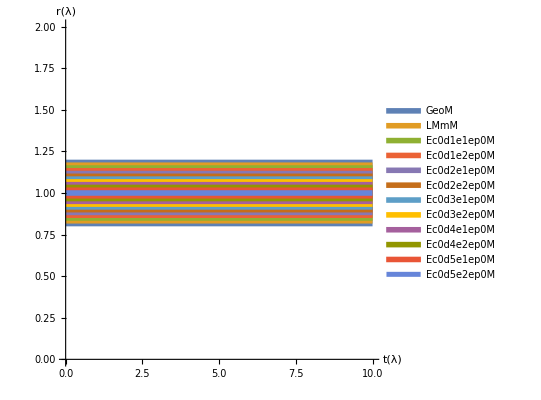

```mathematica
plotAll[crds,FlatMSols]
```

Remove solutions that didn’t run

```mathematica
FinSols`FlatMFinal=First[applyCut[{FlatMSols},#[[2,1]]&]];
```

Starting with {12} entries, cut {0} for a total of {12} remaining entries

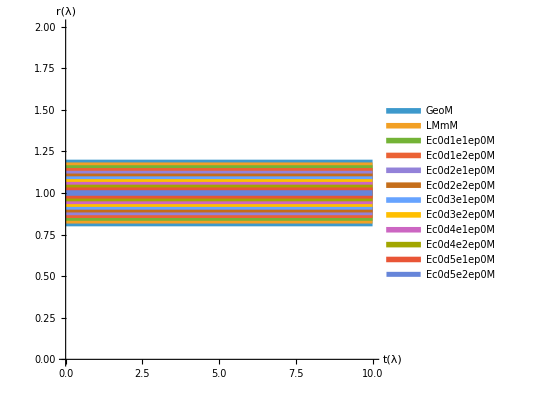

```mathematica
plotAll[crds,FlatMSolsFinal]
```

#### AdS Spacetime & coords

```mathematica
AdsMSols = SolveAll[AdsEqns["MnE"]] ~Join~ SolveAll[AdsEqns["ME"],True];
AdsMSols2 = SolveAll[AdsEqns2["MnE"]] ~Join~ SolveAll[AdsEqns2["ME"],True];
```

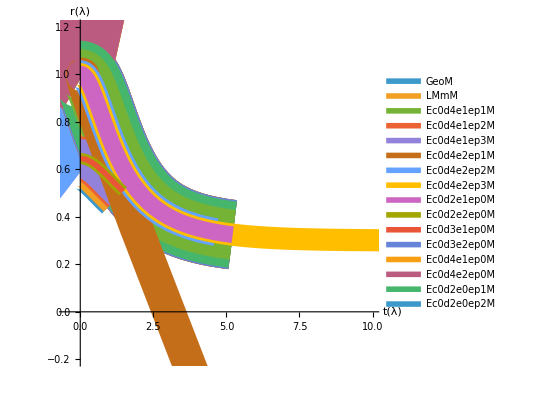

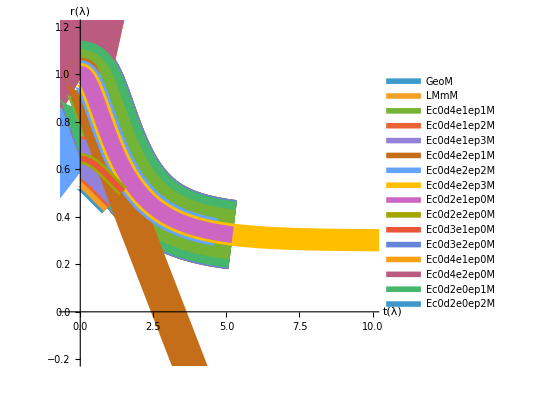

```mathematica
plotAll[crds,AdsMSols,"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
plotAll[crds,AdsMSols2,"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
```

Ok so that’s an absolute mess and we can see lots of them are having issues. First, lets remove the ones that didn’t run so the plot func has less work to do, and then lets discount any that don’t satisfy our initial conditions; can see there’s a whole bunch of them.

```mathematica
AdsMBase={AdsMSols,AdsMSols2};
(*Remove any that didn't run *)
AdsMCut1 = applyCut[AdsMBase,#[[2,1]]&];
```

Starting with {90,90} entries, cut {64,64} for a total of {26,26} remaining entries

```mathematica
(*Remove any that dont satisfy IC*)
(*Need to first account for mismatch due to machine inprecision*)
AdsMIC = {ICcom[[1]]/.rIC["Standard"],ICcom[[2]]/.ValsCom,ICcom[[3]]/.rpIC["Massive"],ICcom[[4]]/.ValsCom}/. (lhs__ == rhs__ -> rhs-$MachineEpsilon<= lhs <= rhs+$MachineEpsilon);
```

```mathematica
AdsMCut2 = applyCut[applyCut[applyCut[applyCut[AdsMCut1,
(*r[0]*) (AdsMIC[[1]]/. #[[1]])&], 
(*t[0]*) (AdsMIC[[2]]/. #[[1]])&] , 
(*r'[0]*)(AdsMIC[[3]]/. #[[1]])&] , 
(*t'[0]*)(AdsMIC[[4]]/. #[[1]])&] ;
```

Starting with {26,26} entries, cut {6,6} for a total of {20,20} remaining entries

Starting with {20,20} entries, cut {0,0} for a total of {20,20} remaining entries

Starting with {20,20} entries, cut {1,1} for a total of {19,19} remaining entries

Starting with {19,19} entries, cut {0,0} for a total of {19,19} remaining entries

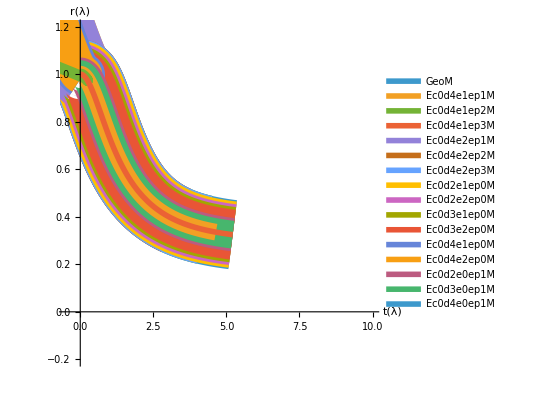

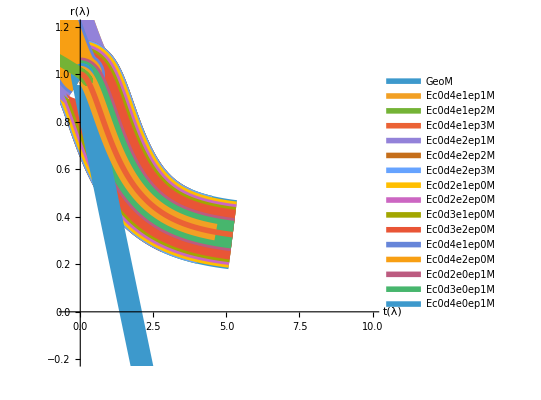

```mathematica
plotAll[crds,AdsMCut2[[1]],"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
plotAll[crds,AdsMCut2[[2]],"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
```

Also now see a lot that just completely head the wrong direction, so lets take out any that are going backwards in time,

```mathematica
AdsMCut3 = applyCut[AdsMCut2,(findSmallestDeriv[t, #[[1]]][[1]]>=0)&];
```

Starting with {19,19} entries, cut {11,9} for a total of {8,10} remaining entries

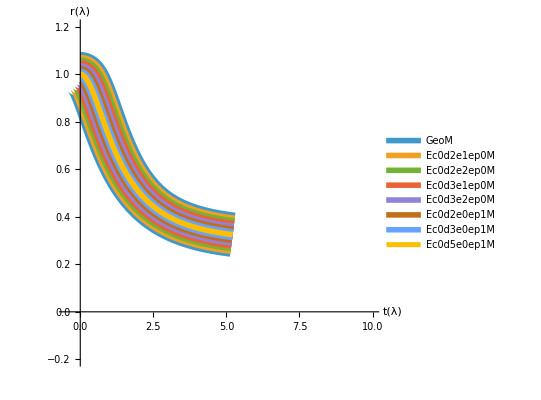

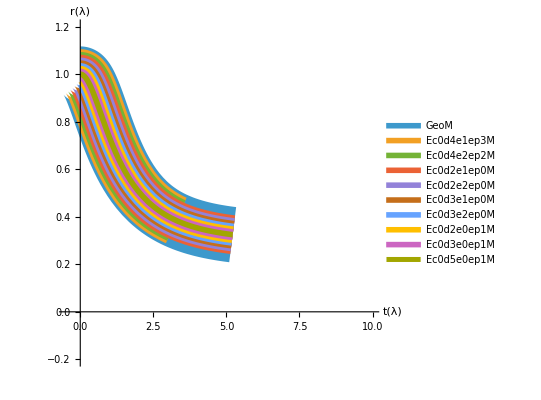

```mathematica
plotAll[crds,AdsMCut3[[1]],"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
plotAll[crds,AdsMCut3[[2]],"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
```

As well as any that aren’t falling inwards, although not sure if there are any

```mathematica
AdsMCut4 = applyCut[AdsMCut3,(findLargestDeriv[r, #[[1]]][[1]]<=0)&];
```

Starting with {8,10} entries, cut {0,0} for a total of {8,10} remaining entries

```mathematica
plotAll[crds,AdsMCut4[[1]],"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
plotAll[crds,AdsMCut4[[2]],"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
```

-Graphics-

-Graphics-

Issue now is just the massive Lagrangian being broken and those ones going straight. Lets try the Lagrangian first,

Debugging Massive Lagrangian

```mathematica
AdsMSols["LMmM"]
AdsMSols2["LMmM"]
```

{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,LMmM: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.}}

{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]},{True,LMmM: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.}}

Ok so seems to be having issues actually solving. Looking at the equations its trying to solve,

```mathematica
AdsEqns["MnE"]["LMmM"]
```

{(r'[λ] (t'[λ] (r[λ] (3 r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)+(0.09-r[λ]^2) r''[λ])+(-0.09+r[λ]^2) r'[λ] t''[λ]))/((0.09-r[λ]^2) ((r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)/(0.09-r[λ]^2))^(3/2))==0,(t'[λ] (t'[λ] (r[λ] (-3 r'[λ]^2+(0.09-r[λ]^2)^2 t'[λ]^2)+(-0.09+r[λ]^2) r''[λ])+(0.09-r[λ]^2) r'[λ] t''[λ]))/((0.09-r[λ]^2) ((r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)/(0.09-r[λ]^2))^(3/2))==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}

```mathematica
AdsEqns2["MnE"]["LMmM"]
```

{-(1. √(-0.09+r[λ]^2) r'[λ] (t'[λ] (r[λ] (3 r'[λ]^2-1. (-0.09+r[λ]^2)^2 t'[λ]^2)-1. (-0.09+r[λ]^2) r''[λ])+(-0.09+r[λ]^2) r'[λ] t''[λ]))/((-1. (r'[λ]^2-1. (-0.09+r[λ]^2)^2 t'[λ]^2))^(3/2))==0,-(1. √(-0.09+r[λ]^2) t'[λ] (t'[λ] (r[λ] (-3 r'[λ]^2+(-0.09+r[λ]^2)^2 t'[λ]^2)+(-0.09+r[λ]^2) r''[λ])-1. (-0.09+r[λ]^2) r'[λ] t''[λ]))/((-1. (r'[λ]^2-1. (-0.09+r[λ]^2)^2 t'[λ]^2))^(3/2))==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}

Those do look pretty gross, so maybe its just struggling to solve? Running these separately,

```mathematica
AdsMLagEqns={AdsEqns["MnE"]["LMmM"],AdsEqns2["MnE"]["LMmM"]}
```

{{(r'[λ] (t'[λ] (r[λ] (3 r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)+(0.09-r[λ]^2) r''[λ])+(-0.09+r[λ]^2) r'[λ] t''[λ]))/((0.09-r[λ]^2) ((r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)/(0.09-r[λ]^2))^(3/2))==0,(t'[λ] (t'[λ] (r[λ] (-3 r'[λ]^2+(0.09-r[λ]^2)^2 t'[λ]^2)+(-0.09+r[λ]^2) r''[λ])+(0.09-r[λ]^2) r'[λ] t''[λ]))/((0.09-r[λ]^2) ((r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)/(0.09-r[λ]^2))^(3/2))==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1},{-(1. √(-0.09+r[λ]^2) r'[λ] (t'[λ] (r[λ] (3 r'[λ]^2-1. (-0.09+r[λ]^2)^2 t'[λ]^2)-1. (-0.09+r[λ]^2) r''[λ])+(-0.09+r[λ]^2) r'[λ] t''[λ]))/((-1. (r'[λ]^2-1. (-0.09+r[λ]^2)^2 t'[λ]^2))^(3/2))==0,-(1. √(-0.09+r[λ]^2) t'[λ] (t'[λ] (r[λ] (-3 r'[λ]^2+(-0.09+r[λ]^2)^2 t'[λ]^2)+(-0.09+r[λ]^2) r''[λ])-1. (-0.09+r[λ]^2) r'[λ] t''[λ]))/((-1. (r'[λ]^2-1. (-0.09+r[λ]^2)^2 t'[λ]^2))^(3/2))==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}}

```mathematica
AdsMLtest1= NDSolve[#,{t,r},{λ,0,10}]& /@ AdsMLagEqns
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

{{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}},{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}}}

Right, obviously, but does applying some different methods fix anything?

```mathematica
AdsMLtest2= NDSolve[#,{t,r},{λ,0,10},Method->"ExplicitRungeKutta"]&/@ AdsMLagEqns
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::nodae: The method NDSolve`ExplicitRungeKutta is not currently implemented to solve differential-algebraic equations. Use Method -> Automatic instead.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::nodae: The method NDSolve`ExplicitRungeKutta is not currently implemented to solve differential-algebraic equations. Use Method -> Automatic instead.

{{},{}}

Ok apparently it being differential-algebraic means the usual ODE methods don’t work here. Probably for the best as any progress gained here won’t apply when we go to PDE case. Those EoM have some pretty gross denominators, so what if we just take the numerator=0 from them?

```mathematica
AdsMLagEqnsNum=(Numerator/@(AdsMLagEqns /. Equal-> List))// Replace[#,List-> Equal,{3},Heads->True]&
```

{{r'[λ] (t'[λ] (r[λ] (3 r'[λ]^2-(0.09-r[λ]^2)^2 t'[λ]^2)+(0.09-r[λ]^2) r''[λ])+(-0.09+r[λ]^2) r'[λ] t''[λ])==0,t'[λ] (t'[λ] (r[λ] (-3 r'[λ]^2+(0.09-r[λ]^2)^2 t'[λ]^2)+(-0.09+r[λ]^2) r''[λ])+(0.09-r[λ]^2) r'[λ] t''[λ])==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1},{-1. √(-0.09+r[λ]^2) r'[λ] (t'[λ] (r[λ] (3 r'[λ]^2-1. (-0.09+r[λ]^2)^2 t'[λ]^2)-1. (-0.09+r[λ]^2) r''[λ])+(-0.09+r[λ]^2) r'[λ] t''[λ])==0,-1. √(-0.09+r[λ]^2) t'[λ] (t'[λ] (r[λ] (-3 r'[λ]^2+(-0.09+r[λ]^2)^2 t'[λ]^2)+(-0.09+r[λ]^2) r''[λ])-1. (-0.09+r[λ]^2) r'[λ] t''[λ])==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}}

```mathematica
AdsMLtest3= NDSolve[#,{t,r},{λ,0,10}]& /@ AdsMLagEqnsNum
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndcf: Repeated convergence test failure at λ == 0.; unable to continue.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndcf: Repeated convergence test failure at λ == 0.; unable to continue.

{{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}},{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}}}

Nope, even doing that it doesn’t seem to work. Is there something wrong with our initial conditions?

```mathematica
AdsMLagEqns //. Flatten[{ToIC,ValsCom,rIC["Standard"],rpIC["Massive"]}]
```

{{True,-1.26589 (0.8281+0.91 r''[0])==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1},{True,-1.26589 (0.8281+0.91 r''[0])==0,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}}

```mathematica
Solve[-1.2658916033352472 (0.8281000000000001+0.91 r''[0])==0,r''[0]]
Solve[-1.265891603335247 (0.8281000000000001+0.91 r''[0])==0,r''[0]]
```

{{r''[0]→-0.91}}

{{r''[0]→-0.91}}

```mathematica
(AdsMLagEqns//. Flatten[{ToIC,ValsCom,rIC["Standard"],rpIC["Massive"]}])/. r''[0]-> -0.91
```

{{True,True,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1},{True,True,r[0]==1,t[0]==0,r'[0]==0,t'[0]==1}}

Ok yeah that all works ok? Maybe just need to give it a seed value for r’’?

```mathematica
AdsMLtest4= NDSolve[#,{t,r},{λ,0,10},InitialSeeding->{r''[0]==-0.91}]& /@ AdsMLagEqns
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

{{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}},{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}}}

```mathematica
AdsMLtest5= NDSolve[#,{t,r},{λ,0,10},InitialSeeding->{r''[0]==-0.91}]& /@ AdsMLagEqnsNum
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

{{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}},{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}}}

Still no luck. Maybe crank up the grid spacing?

```mathematica
AdsMLtest6= NDSolve[#,{t,r},{λ,0,10},MaxStepSize->10^-6]& /@ AdsMLagEqns
AdsMLtest7= NDSolve[#,{t,r},{λ,0,10},MaxStepSize->10^-6]& /@ AdsMLagEqnsNum
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

{{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}},{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}}}

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

{{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}},{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}}}

```mathematica
AdsMLtest8= NDSolve[#,{t,r},{λ,0,10},AccuracyGoal->20]& /@ AdsMLagEqns
AdsMLtest9= NDSolve[#,{t,r},{λ,0,10},AccuracyGoal->20]& /@ AdsMLagEqnsNum
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{{},{}}

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{{},{}}

```mathematica
AdsMLtest10= NDSolve[#,{t,r},{λ,0,10},Method->{"EquationSimplification"->"Residual"}]& /@ AdsMLagEqns
AdsMLtest11= NDSolve[#,{t,r},{λ,0,10},Method->{"EquationSimplification"->"Residual"}]& /@ AdsMLagEqnsNum
```

NDSolve::parpiv: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

{{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}},{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}}}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndcf: Repeated convergence test failure at λ == 0.; unable to continue.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::ndcf: Repeated convergence test failure at λ == 0.; unable to continue.

{{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}},{{t→InterpolatingFunction[…],r→InterpolatingFunction[…]}}}

Doesn’t look like any of these are having any better luck, but for the ones that do run it looks like we’re always getting this can’t solve for explicitly for derivative error. Maybe if we manually solve for it first we’d have more luck?

Lets go back to the equations before we put numeric values in

```mathematica
AdsMLagEqnNoIC ={Thread[AdsRawEqns["LMm"]=={0,0}]};
AppendTo[AdsMLagEqnNoIC,Flatten[FullSimplify[#, Assumptions->{r[λ]>rH>0,l>0,m>=0}]& /@ AdsMLagEqnNoIC]];
AdsMLagEqnNoIC=AdsMLagEqnNoIC~Join~((Numerator/@(AdsMLagEqnNoIC /. Equal-> List))// Replace[#,List-> Equal,{3},Heads->True]&)
```

{{(m r'[λ] (t'[λ] (r[λ] (3 l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (rH^2-r[λ]^2) r''[λ])+l^4 (-rH^2+r[λ]^2) r'[λ] t''[λ]))/(l^4 (rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))==0,(m t'[λ] (t'[λ] (r[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (-rH^2+r[λ]^2) r''[λ])+l^4 (rH^2-r[λ]^2) r'[λ] t''[λ]))/(l^4 (rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))==0},{(m r'[λ] (t'[λ] (r[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (-rH^2+r[λ]^2) r''[λ])+l^4 (rH-r[λ]) (rH+r[λ]) r'[λ] t''[λ]))/(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))==0,(m t'[λ] (t'[λ] (r[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (-rH^2+r[λ]^2) r''[λ])+l^4 (rH^2-r[λ]^2) r'[λ] t''[λ]))/(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))==0},{m r'[λ] (t'[λ] (r[λ] (3 l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (rH^2-r[λ]^2) r''[λ])+l^4 (-rH^2+r[λ]^2) r'[λ] t''[λ])==0,m t'[λ] (t'[λ] (r[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (-rH^2+r[λ]^2) r''[λ])+l^4 (rH^2-r[λ]^2) r'[λ] t''[λ])==0},{m r'[λ] (t'[λ] (r[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (-rH^2+r[λ]^2) r''[λ])+l^4 (rH-r[λ]) (rH+r[λ]) r'[λ] t''[λ])==0,m t'[λ] (t'[λ] (r[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (-rH^2+r[λ]^2) r''[λ])+l^4 (rH^2-r[λ]^2) r'[λ] t''[λ])==0}}

So have 4 pairs of coupled t,r equations. Two options, either solve the two as coupled system, or solve each individually

```mathematica
coupledSolv=Solve[#, r'[λ]]& /@ AdsMLagEqnNoIC
individSolv=(Solve[#, r'[λ]]& /@ #)&/@ AdsMLagEqnNoIC
```

{{{r'[λ]→(rH^2 t''[λ]-r[λ]^2 t''[λ]-(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ])},{r'[λ]→(-((-rH^2+r[λ]^2) t''[λ])+(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ])}},{{r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]-l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}},{{r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}},{{r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}}}

{{{{r'[λ]→0},{r'[λ]→(rH^2 t''[λ]-r[λ]^2 t''[λ]-(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ])},{r'[λ]→(-((-rH^2+r[λ]^2) t''[λ])+(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ])}},{{r'[λ]→(rH^2 t''[λ]-r[λ]^2 t''[λ]-(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ])},{r'[λ]→(-((-rH^2+r[λ]^2) t''[λ])+(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ])}}},{{{r'[λ]→0},{r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]-l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}},{{r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]-l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}}},{{{r'[λ]→0},{r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}},{{r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}}},{{{r'[λ]→0},{r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}},{{r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}}}}

Lots of these look the same, so lets see if it can remove any duplicates. Also want to discount the r’[λ]=0 solution since thats useless to us

```mathematica
rpSols =  DeleteCases[#,r'[λ]->0]& /@(DeleteDuplicates[Flatten[#]]& /@ {coupledSolv,individSolv})
```

{{r'[λ]→(rH^2 t''[λ]-r[λ]^2 t''[λ]-(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ]),r'[λ]→(-((-rH^2+r[λ]^2) t''[λ])+(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ]),r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]-l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])},{r'[λ]→(rH^2 t''[λ]-r[λ]^2 t''[λ]-(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ]),r'[λ]→(-((-rH^2+r[λ]^2) t''[λ])+(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ]),r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]-l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}}

This only deleted duplicates in each of the coupled,individual solutions, so lets flatten those together and delete any duplicates again

```mathematica
rpSols2=DeleteDuplicates[Flatten[rpSols]]
```

{r'[λ]→(rH^2 t''[λ]-r[λ]^2 t''[λ]-(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ]),r'[λ]→(-((-rH^2+r[λ]^2) t''[λ])+(√(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/l^2)/(6 r[λ] t'[λ]),r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]-l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→(-l^4 (-rH^2+r[λ]^2) t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→(l^4 rH^2 t''[λ]-l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ]),r'[λ]→-(-l^4 rH^2 t''[λ]+l^4 r[λ]^2 t''[λ]+l^2 √(-rH^2+r[λ]^2) √(-12 rH^2 r[λ]^2 t'[λ]^4+12 r[λ]^4 t'[λ]^4+12 l^4 r[λ] t'[λ]^2 r''[λ]-l^4 rH^2 t''[λ]^2+l^4 r[λ]^2 t''[λ]^2))/(6 l^4 r[λ] t'[λ])}

Just by visual inspection, looks like we got 3 solutions with 2 branches each, for total of 6 solutions. Lets do the same thing to solve for t’[λ]:

```mathematica
coupledSolvT=Solve[#,t'[λ]]& /@ AdsMLagEqnNoIC
individSolvT=(Solve[#,t'[λ]]& /@ #)&/@ AdsMLagEqnNoIC
```

{{{t'[λ]→(2 2^(1/3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))+((-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(6 2^(1/3) r[λ])},{t'[λ]→-(2^(1/3) (1+ⅈ √3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))-((1-ⅈ √3) (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(12 2^(1/3) r[λ])},{t'[λ]→-(2^(1/3) (1-ⅈ √3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))-((1+ⅈ √3) (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(12 2^(1/3) r[λ])}},{{t'[λ]→-((2^(1/3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)},{t'[λ]→((1+ⅈ √3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)},{t'[λ]→((1-ⅈ √3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)}},{{t'[λ]→-((2^(1/3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)},{t'[λ]→((1+ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)},{t'[λ]→((1-ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)}},{{t'[λ]→-((2^(1/3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)},{t'[λ]→((1+ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)},{t'[λ]→((1-ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)}}}

```mathematica
tpSols =  DeleteCases[#,t'[λ]->0]& /@(DeleteDuplicates[Flatten[#]]& /@ {coupledSolvT,individSolvT})
```

{{t'[λ]→(2 2^(1/3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))+((-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(6 2^(1/3) r[λ]),t'[λ]→-(2^(1/3) (1+ⅈ √3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))-((1-ⅈ √3) (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(12 2^(1/3) r[λ]),t'[λ]→-(2^(1/3) (1-ⅈ √3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))-((1+ⅈ √3) (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(12 2^(1/3) r[λ]),t'[λ]→-((2^(1/3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1+ⅈ √3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1-ⅈ √3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→-((2^(1/3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1+ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1-ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)},{t'[λ]→(2 2^(1/3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))+((-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(6 2^(1/3) r[λ]),t'[λ]→-(2^(1/3) (1+ⅈ √3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))-((1-ⅈ √3) (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(12 2^(1/3) r[λ]),t'[λ]→-(2^(1/3) (1-ⅈ √3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))-((1+ⅈ √3) (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(12 2^(1/3) r[λ]),t'[λ]→-((2^(1/3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1+ⅈ √3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1-ⅈ √3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→-((2^(1/3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1+ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1-ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)}}

```mathematica
tpSols2=DeleteDuplicates[Flatten[tpSols]]
```

{t'[λ]→(2 2^(1/3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))+((-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(6 2^(1/3) r[λ]),t'[λ]→-(2^(1/3) (1+ⅈ √3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))-((1-ⅈ √3) (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(12 2^(1/3) r[λ]),t'[λ]→-(2^(1/3) (1-ⅈ √3) l^4 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ]))/((rH-r[λ])^2 (rH+r[λ])^2 (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))-((1+ⅈ √3) (-(216 l^4 r[λ]^2 r'[λ] t''[λ])/((rH-r[λ]) (rH+r[λ]))+√(-(6912 l^12 r[λ]^3 (3 r[λ] r'[λ]^2+rH^2 r''[λ]-r[λ]^2 r''[λ])^3)/((rH-r[λ])^6 (rH+r[λ])^6)+(46656 l^8 r[λ]^4 r'[λ]^2 t''[λ]^2)/((rH-r[λ])^2 (rH+r[λ])^2)))^(1/3))/(12 2^(1/3) r[λ]),t'[λ]→-((2^(1/3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1+ⅈ √3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1-ⅈ √3) l^4 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) r[λ] (rH^4-2 rH^2 r[λ]^2+r[λ]^4))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 l^12 r[λ]^3 (rH^4-2 rH^2 r[λ]^2+r[λ]^4)^3 (-3 r[λ] r'[λ]^2-rH^2 r''[λ]+r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→-((2^(1/3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))+1/(3 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1+ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1-ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3),t'[λ]→((1-ⅈ √3) (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(2^(2/3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3))-1/(6 2^(1/3) (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5))(1+ⅈ √3) (-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ]+√(108 (rH^4 r[λ]-2 rH^2 r[λ]^3+r[λ]^5)^3 (-3 l^4 r[λ] r'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ])^3+(-27 l^4 rH^10 r[λ]^2 r'[λ] t''[λ]+135 l^4 rH^8 r[λ]^4 r'[λ] t''[λ]-270 l^4 rH^6 r[λ]^6 r'[λ] t''[λ]+270 l^4 rH^4 r[λ]^8 r'[λ] t''[λ]-135 l^4 rH^2 r[λ]^10 r'[λ] t''[λ]+27 l^4 r[λ]^12 r'[λ] t''[λ])^2))^(1/3)}

Ok now those look super gross and we got 9 of them, but suppose all we can do now it to try all the combinations. Kinda worrying that there seems to be an ⅈ in there, but w/e. Gonna use the same IC for everything:

```mathematica
manSolvVar=<||>;
Do[Module[{thisEq},
thisEq=((i /. {Rule-> Equal,m->mass} )~Join~ ICcom) //. Flatten[{ValsCom,rIC["Standard"],rpIC["Massive"]}];
AppendTo[manSolvVar, ToString[Length[manSolvVar]+1]-> thisEq];
],{i,Tuples[{tpSols2,rpSols2}]}]
```

```mathematica
manSolvSols=SolveAll[manSolvVar];
printStatus[manSolvSols]
```

1: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

2: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

3: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

4: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

5: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

6: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

7: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

8: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

9: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

10: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

11: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

12: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

13: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

14: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

15: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

16: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

17: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

18: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

19: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

20: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

21: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

22: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

23: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

24: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

25: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

26: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

27: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

28: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

29: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

30: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

31: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

32: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

33: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

34: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

35: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

36: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

37: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

38: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

39: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

40: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

41: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

42: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

43: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

44: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

45: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

46: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

47: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

48: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

49: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

50: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

51: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

52: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

53: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

54: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

Ok thats not working. Weird that its still complaining about finding the derivative, but maybe that method suggestion will help?

```mathematica
manSolvSols2=SolveAll[manSolvVar,"Method"->{"EquationSimplification"->"Residual"}];
printStatus[manSolvSols2]
```

1: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

2: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

3: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

4: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

5: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

6: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

7: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

8: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

9: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

10: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

11: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

12: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

13: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

14: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

15: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

16: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

17: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

18: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

19: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

20: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

21: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

22: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

23: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

24: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

25: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

26: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

27: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

28: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

29: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

30: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

31: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

32: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

33: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

34: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

35: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

36: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

37: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

38: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

39: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

40: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

41: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

42: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

43: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

44: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

45: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

46: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

47: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

48: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

49: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

50: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

51: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

52: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

53: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

54: Failed to run with the Error: Cannot solve to find an explicit formula for the derivatives. Consider using the option Method->{"EquationSimplification"->"Residual"}.

Nope. Wait shit, is the problem that we solved for the 1st derivative where should’ve for the 2nd? Lets try that quick

```mathematica
coupledSolvRpp=Solve[#, r''[λ]]& /@ AdsMLagEqnNoIC;
individSolvRpp=(Solve[#, r''[λ]]& /@ #)&/@ AdsMLagEqnNoIC;
rppSols =  DeleteCases[#,r''[λ]->0]& /@(DeleteDuplicates[Flatten[#]]& /@ {coupledSolvRpp,individSolvRpp});
rppSols2=DeleteDuplicates[Flatten[rppSols]]
```

{r''[λ]→-(((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2) ((m r[λ] r'[λ] t'[λ] (3 l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2))/(l^4 (rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))+(m (-rH^2+r[λ]^2) r'[λ]^2 t''[λ])/((rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))))/(m r'[λ] t'[λ]),r''[λ]→-(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2) ((m r[λ] t'[λ]^2 (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))/(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))+(l^4 m (rH^2-r[λ]^2) r'[λ] t'[λ] t''[λ])/(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))))/(l^4 m (-rH^2+r[λ]^2) t'[λ]^2),r''[λ]→-(m r[λ] t'[λ]^2 (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 m (rH^2-r[λ]^2) r'[λ] t'[λ] t''[λ])/(l^4 m (-rH^2+r[λ]^2) t'[λ]^2),r''[λ]→(((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2) (-(m r[λ] r'[λ] t'[λ] (3 l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2))/(l^4 (rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))-(m (-rH^2+r[λ]^2) r'[λ]^2 t''[λ])/((rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))))/(m r'[λ] t'[λ]),r''[λ]→((rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2) (-(m r[λ] t'[λ]^2 (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))/(l^4 (rH^2-r[λ]^2) ((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))-(m r'[λ] t'[λ] t''[λ])/(((l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)/(l^2 (rH^2-r[λ]^2)))^(3/2))))/(m (-rH^2+r[λ]^2) t'[λ]^2),r''[λ]→(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2) (-(m r[λ] r'[λ] t'[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))/(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))-(l^4 m (rH-r[λ]) (rH+r[λ]) r'[λ]^2 t''[λ])/(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))))/(l^4 m (-rH^2+r[λ]^2) r'[λ] t'[λ]),r''[λ]→(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2) (-(m r[λ] t'[λ]^2 (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))/(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))-(l^4 m (rH^2-r[λ]^2) r'[λ] t'[λ] t''[λ])/(√(-l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2))))/(l^4 m (-rH^2+r[λ]^2) t'[λ]^2),r''[λ]→(-3 l^4 r[λ] r'[λ]^2 t'[λ]+rH^4 r[λ] t'[λ]^3-2 rH^2 r[λ]^3 t'[λ]^3+r[λ]^5 t'[λ]^3+l^4 rH^2 r'[λ] t''[λ]-l^4 r[λ]^2 r'[λ] t''[λ])/(l^4 (rH^2-r[λ]^2) t'[λ])}

```mathematica
coupledSolvTpp=Solve[#, t''[λ]]& /@ AdsMLagEqnNoIC;
individSolvTpp=(Solve[#, t''[λ]]& /@ #)&/@ AdsMLagEqnNoIC;
tppSols =  DeleteCases[#,t''[λ]->0]& /@(DeleteDuplicates[Flatten[#]]& /@ {coupledSolvTpp,individSolvTpp});
tppSols2=DeleteDuplicates[Flatten[tppSols]]
```

{t''[λ]→-(t'[λ] (r[λ] (-3 l^4 r'[λ]^2+(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (-rH^2+r[λ]^2) r''[λ]))/(l^4 (rH^2-r[λ]^2) r'[λ]),t''[λ]→-(t'[λ] (r[λ] (3 l^4 r'[λ]^2-(rH^2-r[λ]^2)^2 t'[λ]^2)+l^4 (rH^2-r[λ]^2) r''[λ]))/(l^4 (-rH^2+r[λ]^2) r'[λ]),t''[λ]→-(t'[λ] (-3 l^4 r[λ] r'[λ]^2+rH^4 r[λ] t'[λ]^2-2 rH^2 r[λ]^3 t'[λ]^2+r[λ]^5 t'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(l^4 (rH^2-r[λ]^2) r'[λ]),t''[λ]→-(t'[λ] (-3 l^4 r[λ] r'[λ]^2+rH^4 r[λ] t'[λ]^2-2 rH^2 r[λ]^3 t'[λ]^2+r[λ]^5 t'[λ]^2-l^4 rH^2 r''[λ]+l^4 r[λ]^2 r''[λ]))/(l^4 (rH-r[λ]) (rH+r[λ]) r'[λ])}

```mathematica
manSolvVar2=<||>;
Do[Module[{thisEq},
thisEq=((i /. {Rule-> Equal,m->mass} )~Join~ ICcom) //. Flatten[{ValsCom,rIC["Standard"],rpIC["Massive"]}];
AppendTo[manSolvVar2, ToString[Length[manSolvVar2]+1]-> thisEq];
],{i,Tuples[{tppSols2,rppSols2}]}]
```

```mathematica
manSolv2Sols=SolveAll[manSolvVar2];
printStatus[manSolv2Sols]
```

1: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

2: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

3: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

4: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

5: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

6: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

7: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

8: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

9: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

10: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

11: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

12: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

13: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

14: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

15: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

16: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

17: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

18: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

19: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

20: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

21: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

22: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

23: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

24: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

25: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

26: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

27: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

28: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

29: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

30: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

31: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

32: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ok, nope thats still not working... Weird that IC are an issue now, is something wrong with them?

```mathematica
Do[Module[{thisEq},
thisEq=(i /. {Rule-> Equal,m->mass} );
Print[thisEq //. Flatten[{ValsCom,ToIC,rIC["Standard"],rpIC["Massive"]}]]
],{i,Tuples[{tppSols2,rppSols2}]}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

{t''[0]==ComplexInfinity,r''[0]==Indeterminate}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Power::infy: Infinite expression 1/0 encountered.

{t''[0]==ComplexInfinity,r''[0]==-0.91}

Well thats not good...
Ok looking at the equations, see an  issue as all the solutions for t’’ have a r’ in the denominator, and r’[0]=0 is our IC, so thats why that breaks. What if we use the original t eom, but use the r’’ solutions in place of the r eom?

```mathematica
manSolvVar3=<||>;
Do[Module[{thisEq},
thisEq=((i /. {Rule-> Equal,m->mass} )~Join~ ICcom) //. Flatten[{ValsCom,rIC["Standard"],rpIC["Massive"]}];
AppendTo[manSolvVar3, ToString[Length[manSolvVar3]+1]-> thisEq];
],{i,Tuples[{Part[#,1]&/@AdsMLagEqnNoIC,rppSols2}]}]
```

```mathematica
manSolv3Sols=SolveAll[manSolvVar3(*,"Method"->{"EquationSimplification"->"Residual"}*)];
printStatus[manSolv3Sols]
```

1: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

2: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

3: Failed to run with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

4: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

5: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

6: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

7: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

8: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

9: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

10: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

11: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

12: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

13: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

14: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

15: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

16: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

17: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

18: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

19: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

20: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

21: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

22: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

23: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

24: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

25: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

26: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

27: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

28: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

29: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

30: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

31: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

32: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ok hell yeah, some of those actually managed to run. What do they look like tho?

InterpolatingFunction::dmval: Input value {0.000204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

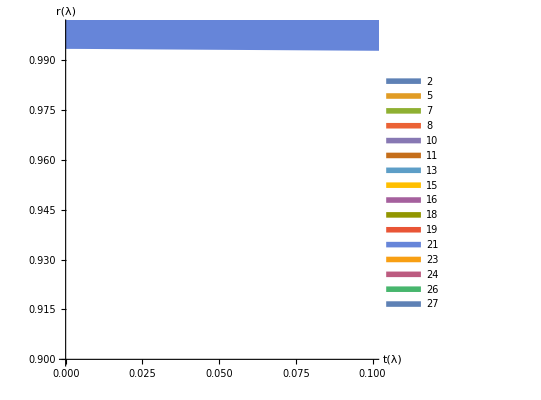

```mathematica
plotAll[crds,manSolv3Sols,"PlotRange"->{{0,0.1},{0.9,1}}]
```

Nope, gonna have to take some cuts.

```mathematica
AdsMmanCut1 = applyCut[{manSolv3Sols},#[[2,1]]&];
```

Starting with {32} entries, cut {13} for a total of {19} remaining entries

```mathematica
AdsMmanCut2= applyCut[AdsMmanCut1,rngAcceptable[{t,r}/.#[[1]]]&];
```

Starting with {19} entries, cut {0} for a total of {19} remaining entries

```mathematica
AdsMmanCut3 = applyCut[AdsMmanCut2,(findSmallestDeriv[t, #[[1]]][[1]]>=0)&];
```

Starting with {19} entries, cut {2} for a total of {17} remaining entries

```mathematica
AdsMmanCut4 = applyCut[AdsMmanCut3,(findLargestDeriv[r, #[[1]]][[1]]<=0)&];
```

Starting with {17} entries, cut {17} for a total of {0} remaining entries

InterpolatingFunction::dmval: Input value {2.04082×10^-7} lies outside the range of data in the interpolating function. Extrapolation will be used.

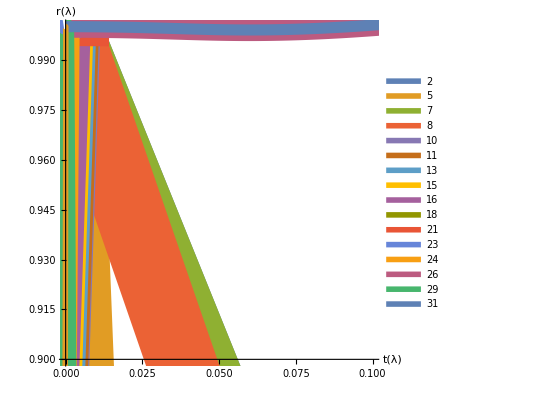

```mathematica
plotAll[crds,AdsMmanCut3[[1]],"LamMax"->0.01,"PlotRange"->{{0,0.1},{0.9,1}}]
```

Ok can’t seem to fix those issues...
Let’s now store all the remaining solutions we haven’t cut out, and combine the two groups (adding in the “Simp” label for the ones that where automatically simplified)

```mathematica
FinSols`AdsMFinal=KeyMap[# <> "Ads"&,AdsMCut4[[1]]~Join~KeyMap[# <> "Simp"&,AdsMCut4[[2]]]];
```

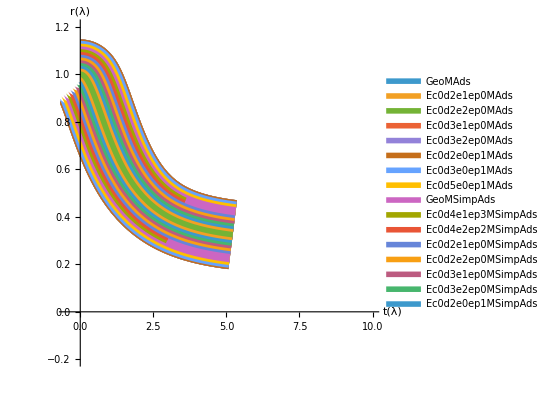

```mathematica
plotAll[crds,AdsMFinal,"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ]
```

#### Tort coords

```mathematica
TortMSols = SolveAll[TortEqns["MnE"]] ~Join~ SolveAll[TortEqns["ME"],True];
TortMSols2 = SolveAll[TortEqns2["MnE"]] ~Join~ SolveAll[TortEqns2["ME"],True];
```

```mathematica
printStatus[TortMSols]
```

GeoM: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

LMmM: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d4e1ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e1ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e1ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d1e1ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep0M: Failed to run with the Error: The function value `3` is not a list of numbers with dimensions `4` at `2` = `1`.

Ec0d2e2ep0M: Failed to run with the Error: The function value `3` is not a list of numbers with dimensions `4` at `2` = `1`.

Ec0d3e1ep0M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e2ep0M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d4e1ep0M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep0M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep0M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d5e2ep0M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d1e0ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e0ep1M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e0ep2M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e0ep3M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e0ep1M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e0ep2M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e0ep3M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d4e0ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e0ep1M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d5e0ep2M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d5e0ep3M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

```mathematica
printStatus[TortMSols2]
```

GeoM: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

LMmM: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep0M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep1M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep2M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep3M: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d4e1ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e1ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e1ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep1M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep2M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep3M: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d1e1ep0M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep0M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep0M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e2ep0M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e1ep0M: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e2ep0M: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d4e1ep0M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep0M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep0M: Ran successfully with no Errors

Ec0d5e2ep0M: Ran successfully with no Errors

Ec0d1e0ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e0ep1M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e0ep2M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e0ep3M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e0ep1M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e0ep2M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e0ep3M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d4e0ep1M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep2M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep3M: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e0ep1M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d5e0ep2M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d5e0ep3M: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

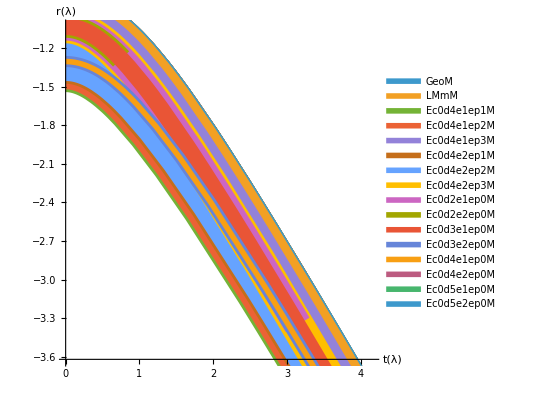

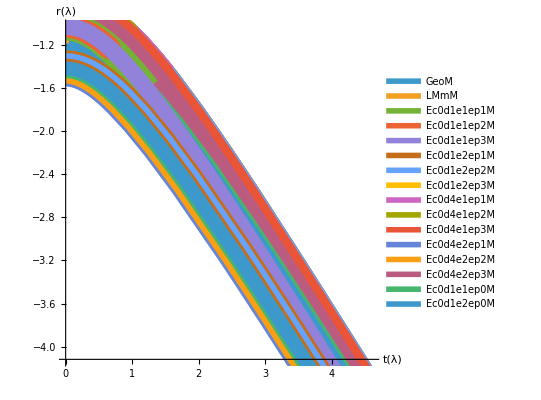

```mathematica
plotAll[crds,TortMSols,"Extrapolate"->False ]
plotAll[crds,TortMSols2,"Extrapolate"->False ]
```

```mathematica
TortMBase={TortMSols,TortMSols2};
(*Remove any that didn't run *)
TortMCut1 = applyCut[TortMBase,#[[2,1]]&];
```

Starting with {90,90} entries, cut {62,53} for a total of {28,37} remaining entries

```mathematica
TortMIC = {ICcom[[1]]//.Flatten[{rIC["Tort"],ValsCom}],ICcom[[2]]/.ValsCom,ICcom[[3]]/.rpIC["Massive"],ICcom[[4]]/.ValsCom}/. (lhs__ == rhs__ -> rhs-$MachineEpsilon<= lhs <= rhs+$MachineEpsilon);
```

Remove any that dont satisfy IC

```mathematica
TortMCut2 = applyCut[applyCut[applyCut[applyCut[TortMCut1,
(*r[0]*)(TortMIC[[1]]/. #[[1]])&], 
(*t[0]*)(TortMIC[[2]]/. #[[1]])&] , 
(*r'[0]*)(TortMIC[[3]]/. #[[1]])&] , 
(*t'[0]*)(TortMIC[[4]]/. #[[1]])&] ;
```

Starting with {28,37} entries, cut {6,10} for a total of {22,27} remaining entries

Starting with {22,27} entries, cut {0,0} for a total of {22,27} remaining entries

Starting with {22,27} entries, cut {0,0} for a total of {22,27} remaining entries

Starting with {22,27} entries, cut {0,0} for a total of {22,27} remaining entries

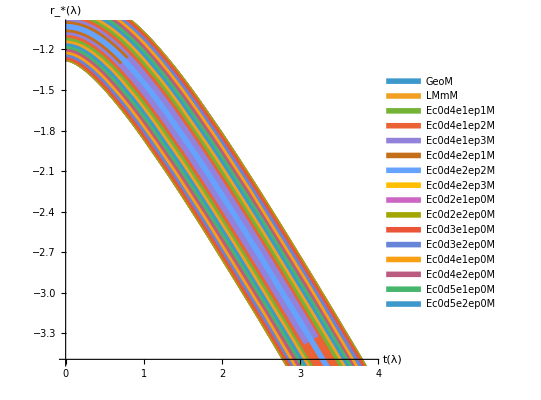

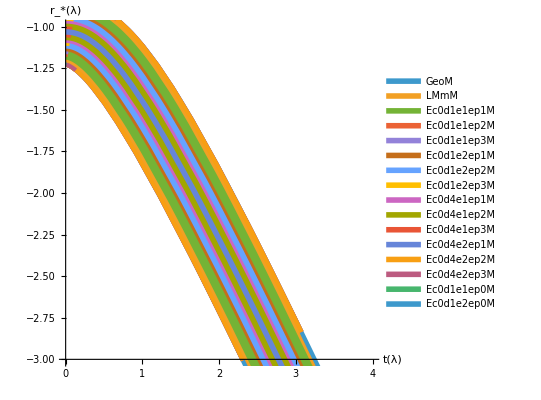

```mathematica
plotAll[crds,TortMCut2[[1]],"Extrapolate"->False,"AxesLabel"->{"t(λ)","r_*(λ)"} ]
plotAll[crds,TortMCut2[[2]],"Extrapolate"->False, "PlotRange"->{{0,4},{-3,-1}},"AxesLabel"->{"t(λ)","r_*(λ)"} ]
```

Ok well it looks like those are all working, out of interest do we actually remove any if we do the same t’ and r’ filtering as we did for cuts 3 and 4 in the AdS case?

```mathematica
(*AdsMCut3 = *)applyCut[TortMCut2,(findSmallestDeriv[t, #[[1]]][[1]]>=0)&];
```

Starting with {22,27} entries, cut {0,0} for a total of {22,27} remaining entries

```mathematica
(*AdsMCut4 =*) applyCut[TortMCut2,(findLargestDeriv[r, #[[1]]][[1]]<=0)&];
```

Starting with {22,27} entries, cut {17,7} for a total of {5,20} remaining entries

Ok yeah the r’ one at least does, but that seems to cut out way to many that don’t even look wrong. Perhaps the issue is only as λ gets very large, so its picking up issues way later than the sections we’re looking at in the plots. Let’s not use these cuts, it’s too restrictive. We’ll keep them cut out in the Ads case since those ones actually looked wrong and also it was the t’ cut that had more of an effect there, which seems much more reasonable to enforce. So let’s store all the remaining ones and again apply the “Simp” label as appropriate

```mathematica
FinSols`TortMFinal=KeyMap[# <> "Tort"&,TortMCut2[[1]]~Join~KeyMap[# <> "Simp"&,TortMCut2[[2]]]];
```

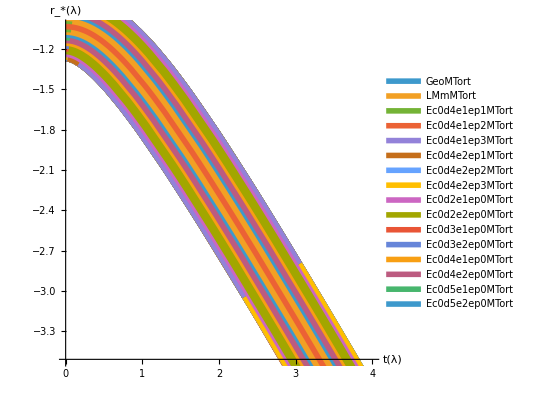

```mathematica
plotAll[crds,TortMFinal,"Extrapolate"->False ,"AxesLabel"->{"t(λ)","r_*(λ)"}]
```

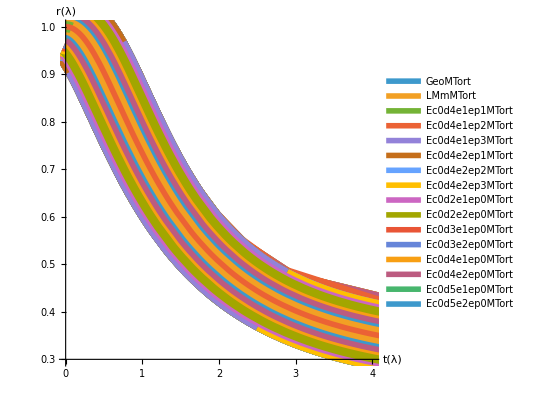

```mathematica
plotAll[{t[λ],NToAds[r[λ]]},TortMFinal,"Extrapolate"->False ,"AxesLabel"->crds]
```

### Massless Solutions

#### Flat Spacetime

```mathematica
FlatMlSols = FlatSpaceEqns["Specials"] ~Join~ SolveAll[FlatSpaceEqns["MlnE"]] ~Join~ SolveAll[FlatSpaceEqns["MlE"],True];
```

```mathematica
printStatus[FlatMlSols]
```

NuE: Manual explicit null method

NuI: Manual implicit null method

GeoMl: Ran successfully with no Errors

Ec0d1e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e2ep0Ml: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d1e3ep0Ml: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d2e1ep0Ml: Ran successfully with no Errors

Ec0d2e2ep0Ml: Ran successfully with no Errors

Ec0d2e3ep0Ml: Ran successfully with no Errors

Ec0d3e1ep0Ml: Ran successfully with no Errors

Ec0d3e2ep0Ml: Ran successfully with no Errors

Ec0d3e3ep0Ml: Ran successfully with no Errors

Ec0d4e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e2ep0Ml: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d4e3ep0Ml: Ran successfully with the Error: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

Ec0d5e1ep0Ml: Ran successfully with no Errors

Ec0d5e2ep0Ml: Ran successfully with no Errors

Ec0d5e3ep0Ml: Ran successfully with no Errors

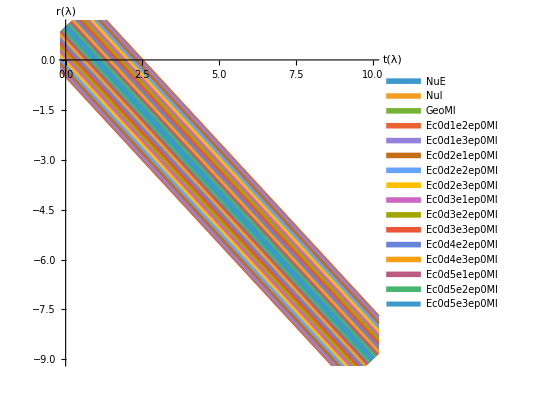

```mathematica
plotAll[crds,FlatMlSols]
```

Remove any that didn't run

```mathematica
FinSols`FlatMlFinal=First[applyCut[{FlatMlSols},#[[2,1]]&]];
```

Starting with {18} entries, cut {2} for a total of {16} remaining entries

#### AdS Spacetime & coords

```mathematica
AdsMlSols = SolveAll[AdsEqns["MlnE"]] ~Join~ SolveAll[AdsEqns["MlE"],True]~Join~ AdsEqns["Specials"];
AdsMlSols2 = SolveAll[AdsEqns2["MlnE"]] ~Join~ SolveAll[AdsEqns2["MlE"],True];
```

```mathematica
printStatus[AdsMlSols]
```

GeoMl: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec1d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e1ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e1ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e2ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e2ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e2ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e3ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e3ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e3ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e1ep2Ml: Ran successfully with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

Ec2d0e1ep3Ml: Ran successfully with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

Ec2d0e2ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e2ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e2ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e3ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e3ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e3ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e1ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e1ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e2ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e2ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e2ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e3ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e3ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e3ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e2ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e3ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e2ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e3ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e2ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e3ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e0ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e0ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e0ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e0ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e0ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e0ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e0ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e0ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e0ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec0d1e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e1ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d4e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e1ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e1ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep1Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep1Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d1e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep0Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e2ep0Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e3ep0Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d4e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e2ep0Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep0Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d5e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d5e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d1e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e0ep1Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e0ep2Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e0ep3Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e0ep1Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d5e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d5e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

NuI: Manual implicit null method

NuE: Manual explicit null method

```mathematica
printStatus[AdsMlSols2]
```

GeoMl: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec1d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e1ep2Ml: Ran successfully with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

Ec1d0e1ep3Ml: Ran successfully with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

Ec1d0e2ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e2ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e2ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e3ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e3ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e3ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e1ep2Ml: Ran successfully with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

Ec2d0e1ep3Ml: Ran successfully with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

Ec2d0e2ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e2ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e2ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e3ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e3ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e3ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e1ep2Ml: Ran successfully with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

Ec3d0e1ep3Ml: Ran successfully with the Error: Repeated convergence test failure at `1` == `2`; unable to continue.

Ec3d0e2ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e2ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e2ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e3ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e3ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e3ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e2ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e3ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e2ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e3ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e2ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e3ep0Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e0ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e0ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec1d0e0ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e0ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e0ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec2d0e0ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e0ep1Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e0ep2Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec3d0e0ep3Ml: Ran successfully with the Error: Error test failure at `1` == `2`; unable to continue.

Ec0d1e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e1ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d4e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e1ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e1ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep1Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep1Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d1e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep0Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e2ep0Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e3ep0Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d4e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e2ep0Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep0Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d5e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d5e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d1e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e0ep1Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e0ep2Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d2e0ep3Ml: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec0d3e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e0ep1Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d5e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d5e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

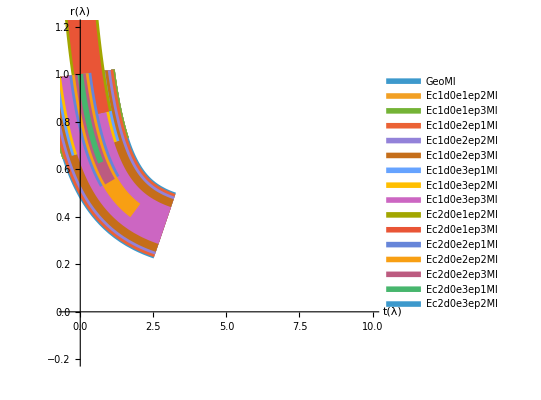

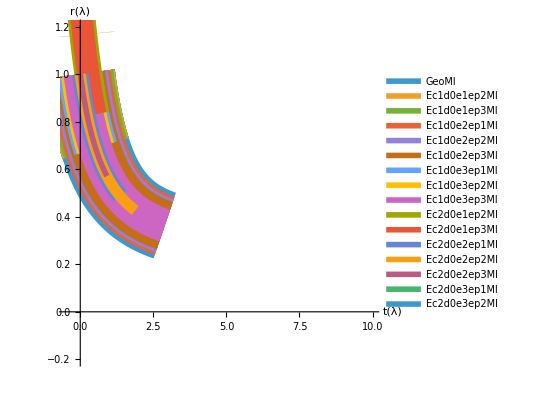

```mathematica
plotAll[crds,AdsMlSols,"PlotRange"-> {{-0.5,10},{-0.2,1.2}},"LamMax"->0.7,"Extrapolate"->False]
plotAll[crds,AdsMlSols2,"PlotRange"-> {{-0.5,10},{-0.2,1.2}},"LamMax"->0.7,"Extrapolate"->False]
```

```mathematica
AdsMlBase={AdsMlSols,AdsMlSols2};
(*Remove any that didn't run *)
AdsMlCut1 = applyCut[AdsMlBase,#[[2,1]]&];
```

Starting with {123,121} entries, cut {63,62} for a total of {60,59} remaining entries

Remove any that don’t satisfy IC

```mathematica
(*Need to first account for mismatch due to machine inprecision*)
AdsMlIC = {ICcom[[1]]/.rIC["Standard"],ICcom[[2]]/.ValsCom,ICcom[[3]]//.ValsCom~Join~{rpIC["Massless"],rIC["Standard"]}~Join~ AdsCrdr,ICcom[[4]]/.ValsCom}/. (lhs__ == rhs__ -> rhs-$MachineEpsilon<= lhs <= rhs+$MachineEpsilon);
```

```mathematica
AdsMlCut2 = applyCut[applyCut[applyCut[applyCut[AdsMlCut1,
(*r[0]*)(AdsMlIC[[1]]/. #[[1]])&], 
(*t[0]*)(AdsMlIC[[2]]/. #[[1]])&] , 
(*r'[0]*)(AdsMlIC[[3]]/. #[[1]])&] , 
(*t'[0]*)(AdsMlIC[[4]]/. #[[1]])&] ;
```

Starting with {60,59} entries, cut {16,16} for a total of {44,43} remaining entries

Starting with {44,43} entries, cut {0,0} for a total of {44,43} remaining entries

Starting with {44,43} entries, cut {0,0} for a total of {44,43} remaining entries

Starting with {44,43} entries, cut {0,0} for a total of {44,43} remaining entries

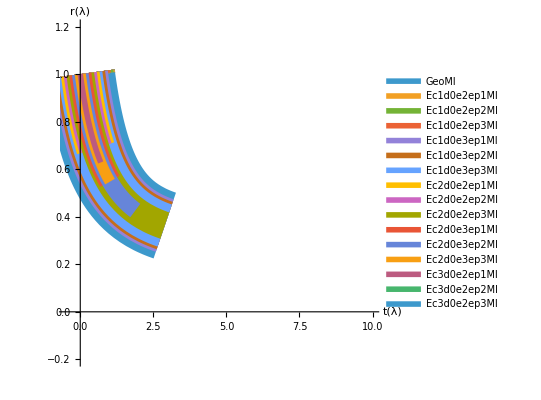

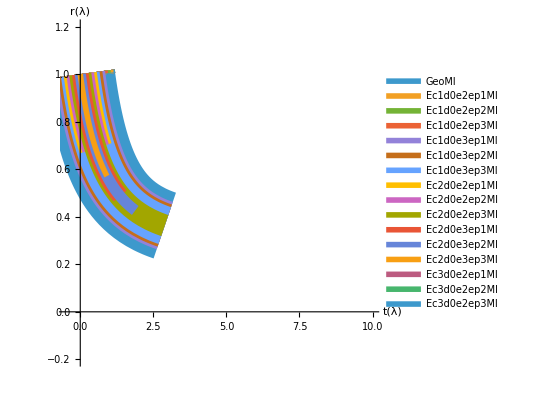

```mathematica
plotAll[crds,AdsMlCut2[[1]],"PlotRange"-> {{-0.5,10},{-0.2,1.2}},"LamMax"->0.7,"Extrapolate"->False]
plotAll[crds,AdsMlCut2[[2]],"PlotRange"-> {{-0.5,10},{-0.2,1.2}},"LamMax"->0.7,"Extrapolate"->False]
```

Remove any going backwards in time

```mathematica
AdsMlCut3 = applyCut[AdsMlCut2,(findSmallestDeriv[t, #[[1]]][[1]]>=0)&];
```

Starting with {44,43} entries, cut {3,4} for a total of {41,39} remaining entries

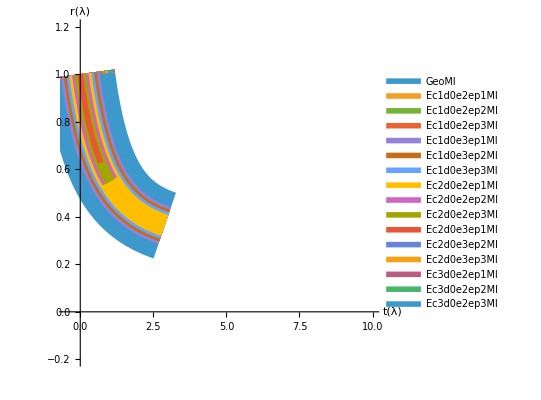

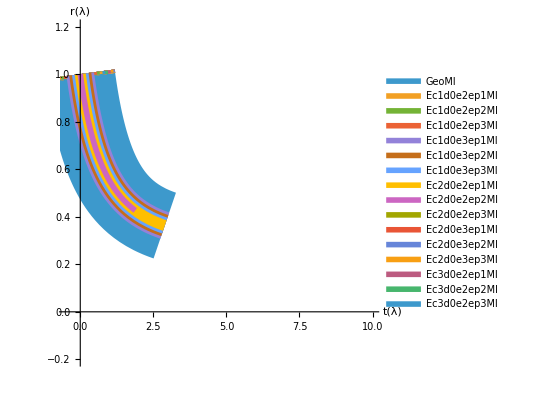

```mathematica
plotAll[crds,AdsMlCut3[[1]],"PlotRange"-> {{-0.5,10},{-0.2,1.2}},"LamMax"->0.7,"Extrapolate"->False]
plotAll[crds,AdsMlCut3[[2]],"PlotRange"-> {{-0.5,10},{-0.2,1.2}},"LamMax"->0.7,"Extrapolate"->False]
```

Remove any that are outgoing

```mathematica
applyCut[AdsMlCut3,(findLargestDeriv[r, #[[1]]][[1]]<=0)&];
```

Starting with {41,39} entries, cut {0,0} for a total of {41,39} remaining entries

Again removing the backwards in time ones seem reasonable and the outgoing cut doesn’t remove any more, so lets just go with the previous

Once again store all remaining and add “Simp” label

```mathematica
FinSols`AdsMlFinal=KeyMap[# <> "Ads"&,AdsMlCut3[[1]]~Join~KeyMap[# <> "Simp"&,AdsMlCut3[[2]]]];
```

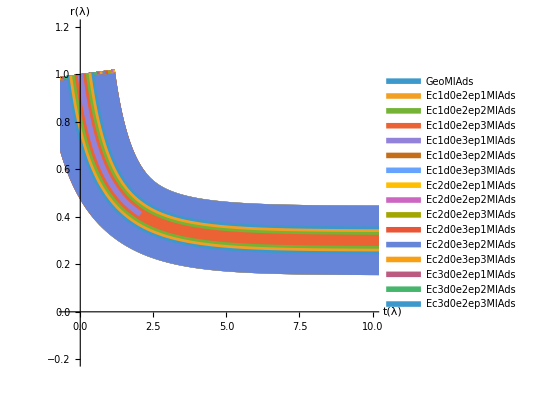

```mathematica
plotAll[crds,AdsMlFinal,"LamMax"->1.3,"PlotRange"-> {{-0.5,10},{-0.2,1.2}} ,"Extrapolate"->False]
```

#### Tort coords

```mathematica
TortMlSols = SolveAll[TortEqns["MlnE"]] ~Join~ SolveAll[TortEqns["MlE"],True]~Join~ TortEqns["Specials"];
TortMlSols2 = SolveAll[TortEqns2["MlnE"]] ~Join~ SolveAll[TortEqns2["MlE"],True];
```

```mathematica
printStatus[TortMlSols]
```

GeoMl: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec1d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e1ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e1ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e1ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e1ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d4e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e1ep2Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e1ep3Ml: Ran successfully with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d1e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d2e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d2e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d4e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d5e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d5e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d1e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d2e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d2e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d5e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d5e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

NuE: Manual explicit null method

NuI: Manual implicit null method

```mathematica
printStatus[TortMlSols2]
```

GeoMl: Ran successfully with the Error: At `1` == `2`, step size is effectively zero; singularity or stiff system suspected.

Ec1d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e1ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e1ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e1ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e1ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e1ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e1ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec1d0e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec2d0e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec3d0e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec1d0e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec2d0e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec3d0e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e1ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e1ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d2e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d3e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d4e1ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e1ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e1ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e2ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e2ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e1ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e2ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep1Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep2Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d5e3ep3Ml: Failed to run with the Error: The number of constraints (`1`) (initial conditions) is not equal to the total differential order of the system plus the number of discrete variables (`2`).

Ec0d1e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d1e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d2e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d2e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d3e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d4e1ep0Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e2ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e3ep0Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e1ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d5e2ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d5e3ep0Ml: Failed to run with the Error: Encountered non-numerical value for a derivative at `1` == `2`.

Ec0d1e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d1e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d2e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d2e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d2e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d3e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d4e0ep1Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep2Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d4e0ep3Ml: Failed to run with the Error: Zero pivot was detected during the numerical factorization or there was a problem in the iterative refinement process. It is possible that the matrix is ill-conditioned or singular.

Ec0d5e0ep1Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d5e0ep2Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Ec0d5e0ep3Ml: Failed to run with the Error: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

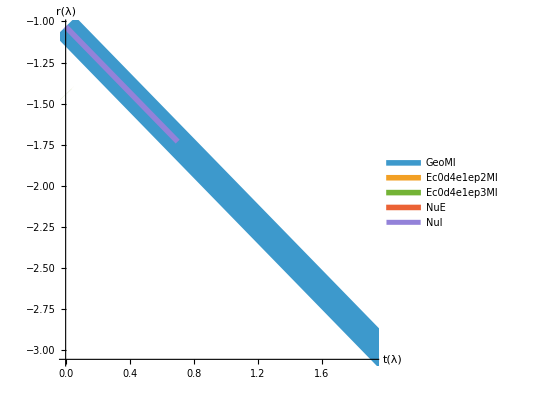

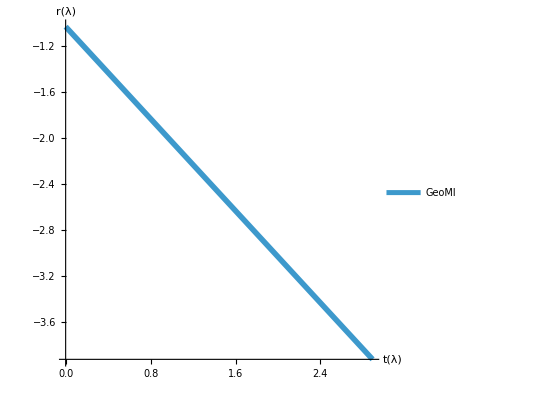

```mathematica
plotAll[crds,TortMlSols,(*"PlotRange"-> {{-0.5,10},{-0.2,1.2}},*)"LamMax"->0.7,"Extrapolate"->False]
plotAll[crds,TortMlSols2,(*"PlotRange"-> {{-0.5,10},{-0.2,1.2}},*)"LamMax"->0.7,"Extrapolate"->False]
```

```mathematica
TortMlBase={TortMlSols,TortMlSols2};
(*Remove any that didn't run *)
TortMlCut1 = applyCut[TortMlBase,#[[2,1]]&];
```

Starting with {123,121} entries, cut {118,120} for a total of {5,1} remaining entries

Ok weirdly it looks like almost all of them fail to run, basically all of them are complaining about singular structure matrix or issue with ICs. Maybe worth going through to sort out at some later point? For now lets just make sure these ones that did run are good

```mathematica
TortMlIC = {ICcom[[1]]//.Flatten[{rIC["Tort"],ValsCom}],ICcom[[2]]/.ValsCom,ICcom[[3]]//.ValsCom~Join~{rpIC["Massless"],rIC["Tort"]}~Join~ TortCrdr,ICcom[[4]]/.ValsCom}/. (lhs__ == rhs__ -> rhs-$MachineEpsilon<= lhs <= rhs+$MachineEpsilon);
```

Remove any that don’t satisfy IC

```mathematica
TortMlCut2 = applyCut[applyCut[applyCut[applyCut[TortMlCut1,
(*r[0]*)(TortMlIC[[1]]/. #[[1]])&], 
(*t[0]*)(TortMlIC[[2]]/. #[[1]])&] , 
(*r'[0]*)(TortMlIC[[3]]/. #[[1]])&] , 
(*t'[0]*)(TortMlIC[[4]]/. #[[1]])&] ;
```

Starting with {5,1} entries, cut {3,0} for a total of {2,1} remaining entries

Starting with {2,1} entries, cut {0,0} for a total of {2,1} remaining entries

Starting with {2,1} entries, cut {0,0} for a total of {2,1} remaining entries

Starting with {2,1} entries, cut {0,0} for a total of {2,1} remaining entries

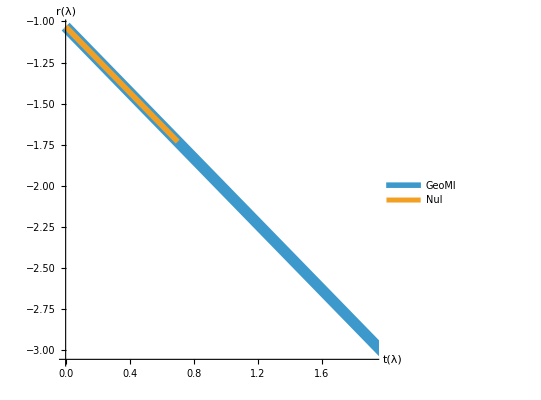

-Graphics-

```mathematica
plotAll[crds,TortMlCut2[[1]],(*"PlotRange"-> {{-0.5,10},{-0.2,1.2}},*)"LamMax"->0.7,"Extrapolate"->False]
plotAll[crds,TortMlCut2[[2]],(*"PlotRange"-> {{-0.5,10},{-0.2,1.2}},*)"LamMax"->0.7,"Extrapolate"->False]
```

Ok yeah thought those looked like wrong starting point. Well it’s not great but I suppose it’s the result we’re getting. Don’t think the backwards in time or outgoing filtering is going to be useful here

```mathematica
applyCut[TortMlCut2,(findSmallestDeriv[t, #[[1]]][[1]]>=0)&];
applyCut[TortMlCut2,(findLargestDeriv[r, #[[1]]][[1]]<=0)&];
```

Starting with {2,1} entries, cut {0,0} for a total of {2,1} remaining entries

Starting with {2,1} entries, cut {0,0} for a total of {2,1} remaining entries

Yeah does nothing, so looks like we just have these 3 sols:

```mathematica
FinSols`TortMlFinal=KeyMap[# <> "Tort"&,TortMlCut2[[1]]~Join~KeyMap[# <> "Simp"&,TortMlCut2[[2]]]];
```

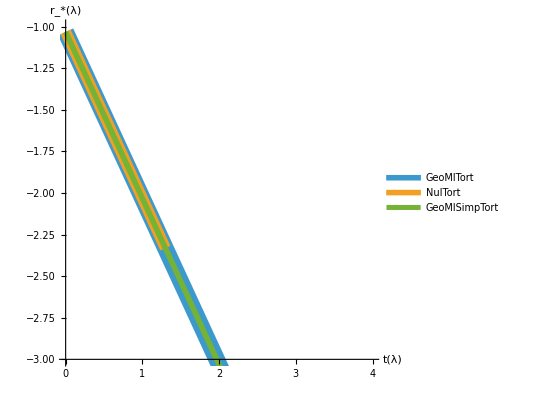

```mathematica
plotAll[crds,(*KeyMap[StringDrop[#,-4]&,*)TortMlFinal(*]*),"LamMax"->1.3, "PlotRange"->{{0,4},{-3,-1}},"AxesLabel"->{"t(λ)","r_*(λ)"},"Extrapolate"->False]
```

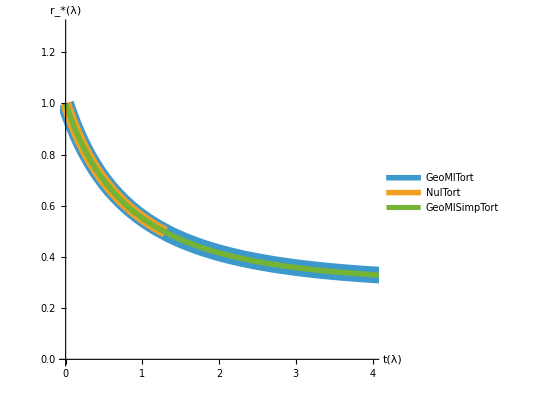

```mathematica
plotAll[{t[λ],NToAds[r[λ]]},TortMlFinal,"LamMax"->1.3, "PlotRange"->{{0,4},{0,1.3}},"AxesLabel"->{"t(λ)","r_*(λ)"},"Extrapolate"->False]
```

### Comparisons

First, need to convert all solutions from pair {r[λ], t[λ]} to a single r[t]:

```mathematica
FinSols`FlatMTraw=genRfT[#[[1]]]&/@FlatMFinal;
FinSols`FlatMlTraw=genRfT[#[[1]]]&/@FlatMlFinal;
```

```mathematica
FinSols`AdsMTraw=genRfT[#[[1]]]&/@AdsMFinal;
FinSols`AdsMlTraw=genRfT[#[[1]]]&/@AdsMlFinal;
```

```mathematica
FinSols`TortMTraw=genRfT[#[[1]]]&/@TortMFinal;
FinSols`TortMlTraw=genRfT[#[[1]]]&/@TortMlFinal;
```

Before doing comps, lets save and/or load all the solutions we care about:

```mathematica
DumpSave[saveDir<>"FinSols.mx","FinSols`"];
```

```mathematica
<< (saveDir<>"FinSols.mx")
```

```mathematica
Names["FinSols`*"] (*List every object in this context*)
```

{AdsMFinal,AdsMlFinal,AdsMlTraw,AdsMTraw,FlatMFinal,FlatMlFinal,FlatMlTraw,FlatMTraw,TortMFinal,TortMlFinal,TortMlTraw,TortMTraw}

As well as all the comparison objects, though of course these will need to be generated in the below sections before they can be saved

```mathematica
DumpSave[saveDir<>"Comps.mx","Comps`"];
```

```mathematica
<< (saveDir<>"Comps.mx")
```

```mathematica
Names["Comps`*"] (*List every object in this context*)
```

{}

#### Generating Massless Comparisons

In order to make comparisons easier, lets make an association of all the massless solutions

```mathematica
mlSols = Association["Flat"->FlatMlTraw, "Ads"->AdsMlTraw,"Tort"->TortMlTraw];
```

Self comparisons:

```mathematica
Comps`MLDif =Module[{anaSol=numericExplNull[#], assoc = mlSols[#]}, 
#->(Table[i->genAnaVnumComp[anaSol,assoc[i],"Diff"],{i,Keys[assoc]}]//Association)
]&/@ Keys[mlSols]// Association;
Comps`MLRat =Module[{anaSol=numericExplNull[#], assoc = mlSols[#]}, 
#->(Table[i->genAnaVnumComp[anaSol,assoc[i],"Ratio"],{i,Keys[assoc]}]//Association)
]&/@ Keys[mlSols]// Association;
Comps`MLRDif =Module[{anaSol=numericExplNull[#], assoc = mlSols[#]}, 
#->(Table[i->genAnaVnumComp[anaSol,assoc[i],"RDiff"],{i,Keys[assoc]}]//Association)
]&/@ Keys[mlSols]// Association;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Cross comparisons:

```mathematica
Comps`MLTortvAds = Module[{refComp = numericExplNull["Ads"], asoc=mlSols["Tort"]},
#->(Table[i-> genAnaVnumComp[refComp,asoc[i],#,{Identity,NToAds}], {i, Keys[asoc]}]//Association)
]&/@ {"Diff","Ratio","RDiff"} // Association;
Comps`MLAdsvTort = Module[{refComp = numericExplNull["Tort"], asoc=mlSols["Ads"]},
#->(Table[i-> genAnaVnumComp[refComp,asoc[i],#,{NToAds,Identity}], {i, Keys[asoc]}]//Association)
]&/@ {"Diff","Ratio","RDiff"} // Association;
```

And now with all of the comparisons computed, we can compute the RMS and Max deviations

```mathematica
Comps`rmsMlSelf= ((getRMS/@ #)&/@ #)&/@ {Comps`MLDif ,Comps`MLRat,Comps`MLRDif };
```

```mathematica
Comps`rmsMlCross = ((getRMS/@ #)&/@ #)&/@{ Comps`MLTortvAds,Comps`MLAdsvTort};
```

```mathematica
Comps`maxMlSelf= ((getMax/@ #)&/@ #)&/@ {Comps`MLDif ,Comps`MLRat,Comps`MLRDif };
```

```mathematica
Comps`maxMCross = ((getMax/@ #)&/@ #)&/@{ Comps`MTortvAds,Comps`MAdsvTort};
```

#### Generating Massive Comparisons

As in the massless case, easiest to first make association of the massive solutions

```mathematica
mSols = Association["Flat"->FlatMTraw, "Ads"->AdsMTraw,"Tort"->TortMTraw];
```

And we always pick the corresponding geodesic solution as the reference solution. First self comparisons:

```mathematica
Comps`MvGeoDif =Module[{compSolName="GeoM"<>Switch[#,"Flat","",_,#], assoc = mSols[#],compSol}, 
compSol=assoc[compSolName];
#->(Table[i->genComp[{compSol,assoc[i]},"Diff",{Identity}],{i,Keys[assoc]}]//Association)
]&/@ Keys[mSols]// Association;
Comps`MvGeoRat =Module[{compSolName="GeoM"<>Switch[#,"Flat","",_,#], assoc = mSols[#],compSol}, 
compSol=assoc[compSolName];
#->(Table[i->genComp[{compSol,assoc[i]},"Ratio",{Identity}],{i,Keys[assoc]}]//Association)
]&/@ Keys[mSols]// Association;
Comps`MvGeoRDif =Module[{compSolName="GeoM"<>Switch[#,"Flat","",_,#], assoc = mSols[#],compSol}, 
compSol=assoc[compSolName];
#->(Table[i->genComp[{compSol,assoc[i]},"RDiff",{Identity}],{i,Keys[assoc]}]//Association)
]&/@ Keys[mSols]// Association;
```

And in the AdS and Tortoise cases, we also have the simplified solutions:

```mathematica
Comps`MvGeoSimpDif =Module[{compSolName="GeoMSimp"<>Switch[#,"Flat","",_,#], assoc = mSols[#],compSol}, 
compSol=assoc[compSolName];
#->(Table[i->genComp[{compSol,assoc[i]},"Diff",{Identity}],{i,Keys[assoc]}]//Association)
]&/@{"Ads","Tort"}// Association;
Comps`MvGeoSimpRat=Module[{compSolName="GeoMSimp"<>Switch[#,"Flat","",_,#], assoc = mSols[#],compSol}, 
compSol=assoc[compSolName];
#->(Table[i->genComp[{compSol,assoc[i]},"Ratio",{Identity}],{i,Keys[assoc]}]//Association)
]&/@{"Ads","Tort"}// Association;
Comps`MvGeoSimpRDif =Module[{compSolName="GeoMSimp"<>Switch[#,"Flat","",_,#], assoc = mSols[#],compSol}, 
compSol=assoc[compSolName];
#->(Table[i->genComp[{compSol,assoc[i]},"RDiff",{Identity}],{i,Keys[assoc]}]//Association)
]&/@{"Ads","Tort"}// Association;
```

And now the cross comparisons:

```mathematica
Comps`MTortvAds = Module[{refComp = mSols["Ads","GeoMAds"], asoc=mSols["Tort"]},
#->(Table[i-> genComp[{refComp,asoc[i]},#,{Identity,NToAds}], {i, Keys[asoc]}]//Association)
]&/@ {"Diff","Ratio","RDiff"} // Association;
Comps`MAdsvTort = Module[{refComp = mSols["Tort","GeoMTort"], asoc=mSols["Ads"]},
#->(Table[i-> genComp[{refComp,asoc[i]},#,{Identity,NToAds}], {i, Keys[asoc]}]//Association)
]&/@ {"Diff","Ratio","RDiff"} // Association;
```

And finally the RMS and Max deviations:

```mathematica
Comps`rmsMSelf= ((getRMS/@ #)&/@ #)&/@ {Comps`MvGeoDif ,Comps`MvGeoRat,Comps`MvGeoRDif,Comps`MvGeoSimpDif ,Comps`MvGeoSimpRat,Comps`MvGeoSimpRDif  };
```

```mathematica
Comps`rmsMCross = ((getRMS/@ #)&/@ #)&/@{ Comps`MTortvAds,Comps`MAdsvTort};
```

```mathematica
Comps`maxMSelf= ((getMax/@ #)&/@ #)&/@ {Comps`MvGeoDif ,Comps`MvGeoRat,Comps`MvGeoRDif,Comps`MvGeoSimpDif ,Comps`MvGeoSimpRat,Comps`MvGeoSimpRDif  };
```

```mathematica
Comps`maxMlCross = ((getMax/@ #)&/@ #)&/@{ Comps`MLTortvAds,Comps`MLAdsvTort};
```

#### Analysis of comparisons & Ranking tables

Now that all the comparisons along with the corresponding RMS and Max deviations have been generated, we now want to compare these and rank them in a readable table. We want 4 tables, each mass case by coordinate system, and massive vs massless across and within coordinate systems, and we also only want to actually look at our AdS and Tortoise coordinate solutions. Let us first organise all our data into a nicer format:

```mathematica
Comps`selfComps=Module[{mAds,,mlAds,mTort,mlTort},
{mAds,mlAds} ={<|"Max"->ResourceFunction["MergeByKey"][(#["Ads"])&/@Comps`maxMSelf,{},Max],"RMS"->ResourceFunction["MergeByKey"][(#["Ads"])&/@Comps`maxMSelf,{},Mean]|>,<|"Max"->ResourceFunction["MergeByKey"][(#["Ads"])&/@Comps`maxMlSelf,{},Max],"RMS"->ResourceFunction["MergeByKey"][(#["Ads"])&/@Comps`maxMlSelf,{},Mean]|>};
{mTort,mlTort} ={<|"Max"->ResourceFunction["MergeByKey"][(#["Tort"])&/@Comps`maxMSelf,{},Max],"RMS"->ResourceFunction["MergeByKey"][(#["Tort"])&/@Comps`maxMSelf,{},Mean]|>,<|"Max"->ResourceFunction["MergeByKey"][(#["Tort"])&/@Comps`maxMlSelf,{},Max],"RMS"->ResourceFunction["MergeByKey"][(#["Tort"])&/@Comps`maxMlSelf,{},Mean]|>};
Association["M"-><|"Ads"->mAds,"Tort"->mTort|>,"Ml"-><|"Ads"->mlAds,"Tort"->mlTort|>]
];
```

```mathematica
Comps`xComps=Module[{maxmAds,maxmTort,maxmlAds,maxmlTort,rmsmAds,rmsmTort,rmsmlAds,rmsmlTort,mass,mless},
{maxmAds,maxmTort}= ResourceFunction["MergeByKey"][{#["RDiff"],#["Ratio"]},{},Max]&/@Comps`maxMCross;
{maxmlAds,maxmlTort}= ResourceFunction["MergeByKey"][{#["RDiff"],#["Ratio"]},{},Max]&/@Comps`maxMlCross;
{rmsmAds,rmsmTort}= ResourceFunction["MergeByKey"][{#["RDiff"],#["Ratio"]},{},Mean]&/@Comps`rmsMCross;
{rmsmlAds,rmsmlTort}= ResourceFunction["MergeByKey"][{#["RDiff"],#["Ratio"]},{},Mean]&/@Comps`rmsMlCross;
mass=AssociationThread[{"Ads","Tort"},{maxmAds,maxmTort}];
Association["M"-><|"Ads"-><|"RMS"->rmsmAds,"Max"->maxmAds|>,"Tort"-><|"RMS"->rmsmTort,"Max"->maxmTort|>|>,
"Ml"-><|"Ads"-><|"RMS"->rmsmlAds,"Max"->maxmlAds|>,"Tort"-><|"RMS"->rmsmlTort,"Max"->maxmlTort|>|>]
];
```

For the massive and massless cases by coordinate system, we can just use as is:

```mathematica
rankingTable[Comps`selfComps["M"]]
```

Ads | Tort
{GeoMAds,{3.70074×10^-17,1.11022×10^-16}} | {GeoMSimpTort,{1.62399×10^-14,9.23706×10^-14}}
{GeoMSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {GeoMTort,{1.62399×10^-14,9.23706×10^-14}}
{Ec0d3e1ep0MSimpAds,{4.47003×10^-7,4.73942×10^-7}} | {Ec0d1e1ep0MSimpTort,{6.88942×10^-8,7.03365×10^-8}}
{Ec0d3e2ep0MSimpAds,{4.47003×10^-7,4.73942×10^-7}} | {Ec0d1e1ep1MSimpTort,{6.88942×10^-8,7.03365×10^-8}}
{Ec0d3e1ep0MAds,{4.52098×10^-7,4.79345×10^-7}} | {Ec0d1e2ep0MSimpTort,{6.88942×10^-8,7.03365×10^-8}}
{Ec0d3e2ep0MAds,{4.52098×10^-7,4.79345×10^-7}} | {Ec0d1e2ep1MSimpTort,{6.88942×10^-8,7.03365×10^-8}}
{Ec0d2e1ep0MAds,{4.73083×10^-7,5.01594×10^-7}} | {Ec0d4e1ep0MSimpTort,{6.88942×10^-8,7.03365×10^-8}}
{Ec0d2e2ep0MAds,{4.73083×10^-7,5.01594×10^-7}} | {Ec0d4e1ep1MSimpTort,{6.88942×10^-8,7.03365×10^-8}}
{Ec0d2e1ep0MSimpAds,{4.73106×10^-7,5.01619×10^-7}} | {Ec0d4e2ep0MSimpTort,{6.88942×10^-8,7.03365×10^-8}}
{Ec0d2e2ep0MSimpAds,{4.73106×10^-7,5.01619×10^-7}} | {Ec0d4e2ep1MSimpTort,{6.88942×10^-8,7.03365×10^-8}}
{Ec0d2e0ep1MAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec0d1e0ep1MSimpTort,{6.89681×10^-8,7.04119×10^-8}}
{Ec0d2e0ep1MSimpAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec0d4e0ep1MSimpTort,{6.89681×10^-8,7.04119×10^-8}}
{Ec0d3e0ep1MAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec0d3e0ep1MSimpTort,{8.1326×10^-8,9.93663×10^-8}}
{Ec0d3e0ep1MSimpAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec0d2e0ep1MSimpTort,{8.1326×10^-8,9.93663×10^-8}}
{Ec0d5e0ep1MAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec0d5e0ep1MSimpTort,{8.1326×10^-8,9.93663×10^-8}}
{Ec0d5e0ep1MSimpAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec0d2e0ep1MTort,{8.1326×10^-8,9.93663×10^-8}}
{Ec0d4e1ep3MSimpAds,{1.82364×10^-6,1.82885×10^-6}} | {Ec0d2e1ep0MTort,{8.1326×10^-8,9.93663×10^-8}}
{Ec0d4e2ep2MSimpAds,{1.82364×10^-6,1.82885×10^-6}} | {Ec0d2e2ep0MTort,{8.1326×10^-8,9.93663×10^-8}}
{-,{-,-}} | {Ec0d3e0ep1MTort,{8.1326×10^-8,9.93663×10^-8}}
{-,{-,-}} | {Ec0d3e1ep0MTort,{8.1326×10^-8,9.93663×10^-8}}
{-,{-,-}} | {Ec0d3e2ep0MTort,{8.1326×10^-8,9.93663×10^-8}}
{-,{-,-}} | {Ec0d5e0ep1MTort,{8.1326×10^-8,9.93663×10^-8}}
{-,{-,-}} | {Ec0d5e1ep0MTort,{8.1326×10^-8,9.93663×10^-8}}
{-,{-,-}} | {Ec0d5e2ep0MTort,{8.1326×10^-8,9.93663×10^-8}}
{-,{-,-}} | {Ec0d4e0ep1MTort,{2.73313×10^-7,4.0025×10^-7}}
{-,{-,-}} | {Ec0d4e1ep0MTort,{2.99573×10^-7,4.38416×10^-7}}
{-,{-,-}} | {Ec0d4e1ep1MTort,{2.99573×10^-7,4.38416×10^-7}}
{-,{-,-}} | {Ec0d4e2ep0MTort,{2.99573×10^-7,4.38416×10^-7}}
{-,{-,-}} | {Ec0d4e2ep1MTort,{2.99573×10^-7,4.38416×10^-7}}
{-,{-,-}} | {LMmMTort,{3.87975×10^-7,3.96113×10^-7}}
{-,{-,-}} | {LMmMSimpTort,{3.97759×10^-7,4.06102×10^-7}}
{-,{-,-}} | {Ec0d2e1ep0MSimpTort,{5.82492×10^-7,5.95692×10^-7}}
{-,{-,-}} | {Ec0d2e2ep0MSimpTort,{5.82492×10^-7,5.95692×10^-7}}
{-,{-,-}} | {Ec0d5e1ep0MSimpTort,{5.82492×10^-7,5.95692×10^-7}}
{-,{-,-}} | {Ec0d5e2ep0MSimpTort,{5.82492×10^-7,5.95692×10^-7}}
{-,{-,-}} | {Ec0d1e1ep3MSimpTort,{1.55444×10^-6,2.06376×10^-6}}
{-,{-,-}} | {Ec0d1e2ep2MSimpTort,{1.55444×10^-6,2.06376×10^-6}}
{-,{-,-}} | {Ec0d4e1ep3MSimpTort,{1.55444×10^-6,2.06376×10^-6}}
{-,{-,-}} | {Ec0d4e2ep2MSimpTort,{1.55444×10^-6,2.06376×10^-6}}
{-,{-,-}} | {Ec0d4e1ep3MTort,{3.83767×10^-6,4.7422×10^-6}}
{-,{-,-}} | {Ec0d4e2ep2MTort,{3.83767×10^-6,4.7422×10^-6}}
{-,{-,-}} | {Ec0d4e0ep3MTort,{6.98297×10^-6,8.02668×10^-6}}
{-,{-,-}} | {Ec0d1e1ep2MSimpTort,{7.09815×10^-6,7.59094×10^-6}}
{-,{-,-}} | {Ec0d1e2ep3MSimpTort,{7.09815×10^-6,7.59094×10^-6}}
{-,{-,-}} | {Ec0d4e1ep2MSimpTort,{7.09815×10^-6,7.59094×10^-6}}
{-,{-,-}} | {Ec0d4e2ep3MSimpTort,{7.09815×10^-6,7.59094×10^-6}}
{-,{-,-}} | {Ec0d4e0ep2MTort,{0.0000239848,0.0000397868}}
{-,{-,-}} | {Ec0d4e1ep2MTort,{0.0000242233,0.0000400747}}
{-,{-,-}} | {Ec0d4e2ep3MTort,{0.0000242233,0.0000400747}}

```mathematica
rankingTable[Comps`selfComps["Ml"]]
```

Ads | Tort
{Ec0d2e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {GeoMlSimpTort,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e0ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {GeoMlTort,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e1ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {NuETort,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e1ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {NuITort,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e2ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec0d2e2ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec0d2e3ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec0d2e3ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec0d4e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec0d4e0ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec0d4e0ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e0ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e0ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e0ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e0ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e0ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e2ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e2ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e2ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e2ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e2ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e2ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e2ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e2ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e3ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e3ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e3ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e3ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e3ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e3ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e3ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec1d0e3ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e0ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e0ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e0ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e0ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e0ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e2ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e2ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e2ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e2ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e2ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e2ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e2ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e2ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e3ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e3ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e3ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e3ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e3ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e3ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e3ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec2d0e3ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e0ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e0ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e0ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e0ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e0ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e2ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e2ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e2ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e2ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e2ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e2ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e2ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e2ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e3ep0MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e3ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e3ep1MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e3ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e3ep2MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e3ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e3ep3MlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{Ec3d0e3ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{GeoMlAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{GeoMlSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}
{NuIAds,{3.70074×10^-17,1.11022×10^-16}} | {-,{-,-}}

For the other two tables, need to do some more merging, so let’s create a quick macro

```mathematica
quickMerge= ResourceFunction["MergeByKey"][{},Join[#] /. List->Join &]
```

[{},Join[#1]/.List→Join&]

And merge our solutions from above as appropriate

```mathematica
Comps`MvMlwithin = <|"M"->quickMerge[{Comps`selfComps["M","Ads"],Comps`selfComps["M","Tort"]}] ,"Ml"->quickMerge[{Comps`selfComps["Ml","Ads"],Comps`selfComps["Ml","Tort"]}] |>;
Comps`MvMlacross = <|"M"->quickMerge[{Comps`xComps["M","Ads"],Comps`xComps["M","Tort"]}] ,"Ml"->quickMerge[{Comps`xComps["Ml","Ads"],Comps`xComps["Ml","Tort"]}] |>;
```

Before finally generating those last two table:

```mathematica
rankingTable[Comps`MvMlwithin]
```

M | Ml
{GeoMAds,{3.70074×10^-17,1.11022×10^-16}} | {Ec0d2e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{GeoMSimpAds,{3.70074×10^-17,1.11022×10^-16}} | {Ec0d2e0ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{GeoMSimpTort,{1.62399×10^-14,9.23706×10^-14}} | {Ec0d2e1ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{GeoMTort,{1.62399×10^-14,9.23706×10^-14}} | {Ec0d2e1ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e1ep0MSimpTort,{6.88942×10^-8,7.03365×10^-8}} | {Ec0d2e2ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e1ep1MSimpTort,{6.88942×10^-8,7.03365×10^-8}} | {Ec0d2e2ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e2ep0MSimpTort,{6.88942×10^-8,7.03365×10^-8}} | {Ec0d2e3ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e2ep1MSimpTort,{6.88942×10^-8,7.03365×10^-8}} | {Ec0d2e3ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep0MSimpTort,{6.88942×10^-8,7.03365×10^-8}} | {Ec0d4e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep1MSimpTort,{6.88942×10^-8,7.03365×10^-8}} | {Ec0d4e0ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep0MSimpTort,{6.88942×10^-8,7.03365×10^-8}} | {Ec0d4e0ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep1MSimpTort,{6.88942×10^-8,7.03365×10^-8}} | {Ec1d0e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e0ep1MSimpTort,{6.89681×10^-8,7.04119×10^-8}} | {Ec1d0e0ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e0ep1MSimpTort,{6.89681×10^-8,7.04119×10^-8}} | {Ec1d0e0ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e0ep1MSimpTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e0ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e0ep1MSimpTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e0ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d5e0ep1MSimpTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e0ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e0ep1MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e2ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e1ep0MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e2ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e2ep0MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e2ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e0ep1MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e2ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e1ep0MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e2ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e2ep0MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e2ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d5e0ep1MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e2ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d5e1ep0MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e2ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d5e2ep0MTort,{8.1326×10^-8,9.93663×10^-8}} | {Ec1d0e3ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e0ep1MTort,{2.73313×10^-7,4.0025×10^-7}} | {Ec1d0e3ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep0MTort,{2.99573×10^-7,4.38416×10^-7}} | {Ec1d0e3ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep1MTort,{2.99573×10^-7,4.38416×10^-7}} | {Ec1d0e3ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep0MTort,{2.99573×10^-7,4.38416×10^-7}} | {Ec1d0e3ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep1MTort,{2.99573×10^-7,4.38416×10^-7}} | {Ec1d0e3ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{LMmMTort,{3.87975×10^-7,3.96113×10^-7}} | {Ec1d0e3ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{LMmMSimpTort,{3.97759×10^-7,4.06102×10^-7}} | {Ec1d0e3ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e1ep0MSimpAds,{4.47003×10^-7,4.73942×10^-7}} | {Ec2d0e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e2ep0MSimpAds,{4.47003×10^-7,4.73942×10^-7}} | {Ec2d0e0ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e1ep0MAds,{4.52098×10^-7,4.79345×10^-7}} | {Ec2d0e0ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e2ep0MAds,{4.52098×10^-7,4.79345×10^-7}} | {Ec2d0e0ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e1ep0MAds,{4.73083×10^-7,5.01594×10^-7}} | {Ec2d0e0ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e2ep0MAds,{4.73083×10^-7,5.01594×10^-7}} | {Ec2d0e0ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e1ep0MSimpAds,{4.73106×10^-7,5.01619×10^-7}} | {Ec2d0e2ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e2ep0MSimpAds,{4.73106×10^-7,5.01619×10^-7}} | {Ec2d0e2ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e0ep1MAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec2d0e2ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e0ep1MSimpAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec2d0e2ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e0ep1MAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec2d0e2ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d3e0ep1MSimpAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec2d0e2ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d5e0ep1MAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec2d0e2ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d5e0ep1MSimpAds,{4.73109×10^-7,5.01622×10^-7}} | {Ec2d0e2ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e1ep0MSimpTort,{5.82492×10^-7,5.95692×10^-7}} | {Ec2d0e3ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d2e2ep0MSimpTort,{5.82492×10^-7,5.95692×10^-7}} | {Ec2d0e3ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d5e1ep0MSimpTort,{5.82492×10^-7,5.95692×10^-7}} | {Ec2d0e3ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d5e2ep0MSimpTort,{5.82492×10^-7,5.95692×10^-7}} | {Ec2d0e3ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e1ep3MSimpTort,{1.55444×10^-6,2.06376×10^-6}} | {Ec2d0e3ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e2ep2MSimpTort,{1.55444×10^-6,2.06376×10^-6}} | {Ec2d0e3ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep3MSimpTort,{1.55444×10^-6,2.06376×10^-6}} | {Ec2d0e3ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep2MSimpTort,{1.55444×10^-6,2.06376×10^-6}} | {Ec2d0e3ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep3MSimpAds,{1.82364×10^-6,1.82885×10^-6}} | {Ec3d0e0ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep2MSimpAds,{1.82364×10^-6,1.82885×10^-6}} | {Ec3d0e0ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep3MTort,{3.83767×10^-6,4.7422×10^-6}} | {Ec3d0e0ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep2MTort,{3.83767×10^-6,4.7422×10^-6}} | {Ec3d0e0ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e0ep3MTort,{6.98297×10^-6,8.02668×10^-6}} | {Ec3d0e0ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e1ep2MSimpTort,{7.09815×10^-6,7.59094×10^-6}} | {Ec3d0e0ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d1e2ep3MSimpTort,{7.09815×10^-6,7.59094×10^-6}} | {Ec3d0e2ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep2MSimpTort,{7.09815×10^-6,7.59094×10^-6}} | {Ec3d0e2ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep3MSimpTort,{7.09815×10^-6,7.59094×10^-6}} | {Ec3d0e2ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e0ep2MTort,{0.0000239848,0.0000397868}} | {Ec3d0e2ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e1ep2MTort,{0.0000242233,0.0000400747}} | {Ec3d0e2ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{Ec0d4e2ep3MTort,{0.0000242233,0.0000400747}} | {Ec3d0e2ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e2ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e2ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e3ep0MlAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e3ep0MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e3ep1MlAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e3ep1MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e3ep2MlAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e3ep2MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e3ep3MlAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {Ec3d0e3ep3MlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {GeoMlAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {GeoMlSimpAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {GeoMlSimpTort,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {GeoMlTort,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {NuETort,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {NuIAds,{3.70074×10^-17,1.11022×10^-16}}
{-,{-,-}} | {NuITort,{3.70074×10^-17,1.11022×10^-16}}

```mathematica
rankingTable[Comps`MvMlacross]
```

Join::normal: Nonatomic expression expected at position 1 in Join[1211].

Join::normal: Nonatomic expression expected at position 1 in Join[4].

Join::normal: Nonatomic expression expected at position 1 in Join[Automatic].

General::stop: Further output of Join::normal will be suppressed during this calculation.